## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

G:\My Drive\bubble_bec\mathematica_packages

G:\My Drive\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
```

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

These values taken from SM3 “predictions”

```mathematica
(** Current to field magnitude conversion factors for Bias **)
BxCalib=40.625;(*[G/A]*)
ByCalib=14.286;(*[G/A]*)
BzCalib=-10.368;(*[G/A]*)

(** Max current values **)
(* Chip *)
IlbMax=3.5; (* [A] *)
IzbMax=-3.5;(* [A] *)
IhMax=5.;(* [A] *)

(* Bias coils *)
IbxMax=8.;(*[A]*)
IbyMax=3.02;(*[A]*)
IbzMax=3.;(*[A]*)

(** Table values **)
(* These were taken from CAL3A_chiptrap_v1.pdf *)
(* Initial trap *)
tableZLHb={
(* Chip *)
AZ1=0.243,(* % *)
AZ2=-0.686,(* % *)
H1pH2=0.46,(* % *) 

(* Bias coils *)
T1=0.0275,(*%*)
T2=T1,
Y=0.85,(*%*)
Z=-0.05(*%*)
};

fdec=0.2;
tableZLHbDecomp={
(* Chip *)
tableZLHb⟦1⟧, (* AZ1 [%] *)
tableZLHb⟦2⟧,(* AZ2 [%] *)
tableZLHb⟦3⟧,(* H1pH2 [%] *)

(* Bias coils *)
fdec*tableZLHb⟦4⟧,(* T1 [%] *)
fdec*tableZLHb⟦5⟧,(* T2 [%] *)
fdec*tableZLHb⟦6⟧,(* Y [%] *)
fdec*tableZLHb⟦7⟧(* Z [%] *)
};

tableZHb={
(* Chip *)
0., (* AZ1 [%] *)
-0.743, (* AZ2 [%] *)
0.46, (* H1pH2 [%] *)

(* Bias coils *)
-0.018, (* T1 [%] *)
-0.018, (* T2 [%] *)
0.63,(* Y [%] *)
-0.0001 (* Z [%] *)
};

tableZHbC={
(* Chip *)
0., (* AZ1 [%] *)
0.914, (* AZ2 [%] *)
0.26, (* H1pH2 [%] *)

(* Bias coils *)
-0.006125,(* T1 [%] *)
-0.006125,(* T2 [%] *)
0.0677, (* Y [%] *)
-0.11367 (* Z [%] *)
};

(* Trap CurrL, CurrZ, CurrH, Bx1, By1, Bz1 *)
defineTableFromTrap[trap_]:=Module[
{CurrL=trap⟦1⟧,
CurrZ=trap⟦2⟧,
CurrH=trap⟦3⟧,
Bx1=trap⟦4⟧,
By1=trap⟦5⟧,
Bz1=trap⟦6⟧,
table},

table={
CurrL/IlbMax, (*AZ1 [%]*)
CurrZ/IzbMax, (*AZ2 [%]*)
CurrH/IhMax, (*H1pH2 [%]*)

Bx1/(-1.*IbxMax*BxCalib), (*T1*)
Bx1/(-1.*IbxMax*BxCalib), (*T2*)
By1/(IbyMax*ByCalib), (*Y*)
Bz1/(IbzMax*BzCalib) (*Z*)
};
Return[table];
];

defineTrapFromTable[table_]:=Module[
{AZ1=table⟦1⟧,
AZ2=table⟦2⟧,
H1pH2=table⟦3⟧,
T1=table⟦4⟧,
T2=table⟦5⟧, (* Currently T2=T1, and so doesn't play role yet *)
Y=table⟦6⟧,
Z=table⟦7⟧,
trap},

trap={
(* Chip *)
AZ1*IlbMax,(*Ilb0 [A]*)
AZ2*IzbMax,(*Izb0 [A]*)
H1pH2*IhMax,(*Ih0 [A]*)

(* Bias coils *)
(-1.)*T1*IbxMax*BxCalib,(*Bx [G]*)
Y*IbyMax*ByCalib,(*By [G]*)
Z*IbzMax *BzCalib(*Bz [G]*)
};
Return[trap];
]

(* Package for resale: *)
(* Compare these values to those in SM3 "predictions", although Bzfinal, for us, should be multiplied by 0.2 *)
trapzero=defineTrapFromTable[tableZLHb]
trapone=defineTrapFromTable[tableZLHbDecomp]
(*trapone=defineTrapFromTable@defineTableFromTrap@{CurrL,CurrZ,CurrH,Bx1,By1,Bz1}*)
```

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0.8505,2.401,2.3,-1.7875,7.33443,0.31104}

### Define target ramp analytic function

```mathematica
cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
```

### Define ramp ansatz

#### Trap 1 Short

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

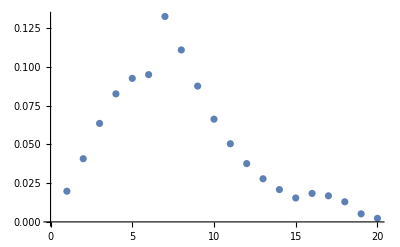

```mathematica
ListPlot[rampin1sguess⟦2⟧]
```

```mathematica
(*rampin1sguess⟦1,9;;13⟧
rampin1sguess⟦1⟧=Join[rampin1sguess⟦1,1;;9⟧,{0.01,0.01,0.01,0.01,0.01},rampin1sguess⟦1,10;;⟧]
rampin1sguess⟦1,9;;18⟧
rampin1sguess⟦1,9;;18⟧={0.02,0.02,0.02,0.01,0.01,0.01,0.01,0.01,0.02,0.02}*)
```

```mathematica
(*rampin1sguess⟦2,9;;13⟧
rampin1sguess⟦2⟧=Join[rampin1sguess⟦2,1;;9⟧,ConstantArray[0.,5],rampin1sguess⟦2,10;;⟧]*)
```

```mathematica
(*rampin1sguess*)
```

```mathematica
Total[rampin1sguess⟦1⟧]
```

1.

```mathematica
Total[rampin1sguess⟦2⟧]
```

1.

## Calculate ramp

```mathematica
nramps1short=Length@rampin1sguess⟦1⟧
```

20

The following took 8 1/2 minutes to complete. (1 1/4 hr on the Dell)

```mathematica
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,nramps1short,-3.5,-5])//Timing
```

Completed point 1 of 19 in 0. s (Total time: 0. min).

Completed point 2 of 19 in 0.015625 s (Total time: 0.000260417 min).

Completed point 3 of 19 in 0. s (Total time: 0.000260417 min).

Completed point 4 of 19 in 0.015625 s (Total time: 0.000520833 min).

Completed point 5 of 19 in 0.015625 s (Total time: 0.00078125 min).

Completed point 6 of 19 in 0. s (Total time: 0.00078125 min).

Completed point 7 of 19 in 0.015625 s (Total time: 0.00104167 min).

Completed point 8 of 19 in 0. s (Total time: 0.00104167 min).

Completed point 9 of 19 in 0. s (Total time: 0.00104167 min).

Completed point 10 of 19 in 0.015625 s (Total time: 0.00130208 min).

Completed point 11 of 19 in 0. s (Total time: 0.00130208 min).

Completed point 12 of 19 in 0.015625 s (Total time: 0.0015625 min).

Completed point 13 of 19 in 0. s (Total time: 0.0015625 min).

Completed point 14 of 19 in 0.03125 s (Total time: 0.00208333 min).

Completed point 15 of 19 in 0. s (Total time: 0.00208333 min).

Completed point 16 of 19 in 0. s (Total time: 0.00208333 min).

Completed point 17 of 19 in 0. s (Total time: 0.00208333 min).

Completed point 18 of 19 in 0. s (Total time: 0.00208333 min).

Completed point 19 of 19 in 0.015625 s (Total time: 0.00234375 min).

{0.140625,{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}}

```mathematica
rampin1s⟦2⟧-rampin1sguess⟦2⟧
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

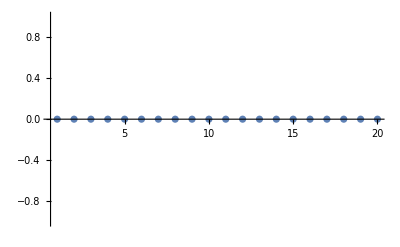

```mathematica
ListPlot[%,PlotRange->All]
```

The following took ~4 1/2 minutes to run. (~ 1 hr 12 min on Dell)

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,nramps1short];)//Timing
```

Part::partd: Part specification z0[0.8505,2.401,2.3,-8.9375,36.6722,1.5552]⟦All,2⟧ is longer than depth of object.

{0.015625,Null}

### Plot calculated ramp’s parameters

Part::partd: Part specification {«1»}⟦All,2,3⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,«51»},{{«1»},{«1»},{«1»},«46»,{«1»},«51»}⟦All,2,3⟧} cannot be transposed.

Part::partd: Part specification {«1»}⟦All,2,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},{«1»}⟦All,2,3⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},{«1»}⟦«1»⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[«1»].

GridLines→{{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.},{}}

{{1.0202,1.04081,1.06184,1.08329,1.10517,1.1275,1.16183,1.19722,1.23368,1.27125,1.30996,1.34986,1.39097,1.43333,1.47698,1.55271,1.68203,1.93479,2.2705,2.71828},{}}

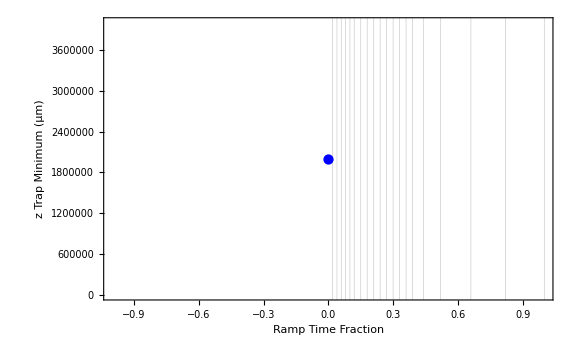
-Graphics-Show[ListLogPlot[Transpose[{{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,1/2,51/100,13/25,53/100,27/50,11/20,14/25,57/100,29/50,59/100,3/5,61/100,31/50,63/100,16/25,13/20,33/50,67/100,17/25,69/100,7/10,71/100,18/25,73/100,37/50,3/4,19/25,77/100,39/50,79/100,4/5,81/100,41/50,83/100,21/25,17/20,43/50,87/100,22/25,89/100,9/10,91/100,23/25,93/100,47/50,19/20,24/25,97/100,49/50,99/100,1},{{z0[0.8505,2.401,2.3,-8.9375,36.6722,1.5552]⟦All,2⟧,-8.9375,ChipTrapField[z0[0.8505,2.401,2.3,-8.9375,36.6722,1.5552],All,2,0.8505,2.401,2.3,-8.9375,36.6722,1.5552]},{z0[-0.00991 (0.8505-1. CurrL),-0.00991 (2.401-1. CurrZ),-0.00991 (2.3-1. CurrH),-0.00991 (-8.9375-1. Bx1),-0.00991 (36.6722-1. By1),-0.00991 (1.5552-1. Bz1)],-8.9375-0.00991 (-8.9375-1. Bx1),ChipTrapField[-0.00991 (0.8505-1. CurrL),-0.00991 (2.401-1. CurrZ),-0.00991 (2.3-1. CurrH),0.8505-0.00991 (0.8505-1. CurrL),2.401-0.00991 (2.401-1. CurrZ),2.3-0.00991 (2.3-1. CurrH),-8.9375-0.00991 (-8.9375-1. Bx1),36.6722-0.00991 (36.6722-1. By1),1.5552-0.00991 (1.5552-1. Bz1)]},{z0[-0.01982 (0.8505-1. CurrL),-0.01982 (2.401-1. CurrZ),-0.01982 (2.3-1. CurrH),-0.01982 (-8.9375-1. Bx1),-0.01982 (36.6722-1. By1),-0.01982 (1.5552-1. Bz1)],-8.9375-0.01982 (-8.9375-1. Bx1),ChipTrapField[-0.01982 (0.8505-1. CurrL),-0.01982 (2.401-1. CurrZ),-0.01982 (2.3-1. CurrH),0.8505-0.01982 (0.8505-1. CurrL),2.401-0.01982 (2.401-1. CurrZ),2.3-0.01982 (2.3-1. CurrH),-8.9375-0.01982 (-8.9375-1. Bx1),36.6722-0.01982 (36.6722-1. By1),1.5552-0.01982 (1.5552-1. Bz1)]},{z0[-0.04021 (0.8505-1. CurrL),-0.04021 (2.401-1. CurrZ),-0.04021 (2.3-1. CurrH),-0.04021 (-8.9375-1. Bx1),-0.04021 (36.6722-1. By1),-0.04021 (1.5552-1. Bz1)],-8.9375-0.04021 (-8.9375-1. Bx1),ChipTrapField[-0.04021 (0.8505-1. CurrL),-0.04021 (2.401-1. CurrZ),-0.04021 (2.3-1. CurrH),0.8505-0.04021 (0.8505-1. CurrL),2.401-0.04021 (2.401-1. CurrZ),2.3-0.04021 (2.3-1. CurrH),-8.9375-0.04021 (-8.9375-1. Bx1),36.6722-0.04021 (36.6722-1. By1),1.5552-0.04021 (1.5552-1. Bz1)]},{z0[-0.0606 (0.8505-1. CurrL),-0.0606 (2.401-1. CurrZ),-0.0606 (2.3-1. CurrH),-0.0606 (-8.9375-1. Bx1),-0.0606 (36.6722-1. By1),-0.0606 (1.5552-1. Bz1)],-8.9375-0.0606 (-8.9375-1. Bx1),ChipTrapField[-0.0606 (0.8505-1. CurrL),-0.0606 (2.401-1. CurrZ),-0.0606 (2.3-1. CurrH),0.8505-0.0606 (0.8505-1. CurrL),2.401-0.0606 (2.401-1. CurrZ),2.3-0.0606 (2.3-1. CurrH),-8.9375-0.0606 (-8.9375-1. Bx1),36.6722-0.0606 (36.6722-1. By1),1.5552-0.0606 (1.5552-1. Bz1)]},{z0[-0.092385 (0.8505-1. CurrL),-0.092385 (2.401-1. CurrZ),-0.092385 (2.3-1. CurrH),-0.092385 (-8.9375-1. Bx1),-0.092385 (36.6722-1. By1),-0.092385 (1.5552-1. Bz1)],-8.9375-0.092385 (-8.9375-1. Bx1),ChipTrapField[-0.092385 (0.8505-1. CurrL),-0.092385 (2.401-1. CurrZ),-0.092385 (2.3-1. CurrH),0.8505-0.092385 (0.8505-1. CurrL),2.401-0.092385 (2.401-1. CurrZ),2.3-0.092385 (2.3-1. CurrH),-8.9375-0.092385 (-8.9375-1. Bx1),36.6722-0.092385 (36.6722-1. By1),1.5552-0.092385 (1.5552-1. Bz1)]},{z0[-0.12417 (0.8505-1. CurrL),-0.12417 (2.401-1. CurrZ),-0.12417 (2.3-1. CurrH),-0.12417 (-8.9375-1. Bx1),-0.12417 (36.6722-1. By1),-0.12417 (1.5552-1. Bz1)],-8.9375-0.12417 (-8.9375-1. Bx1),ChipTrapField[-0.12417 (0.8505-1. CurrL),-0.12417 (2.401-1. CurrZ),-0.12417 (2.3-1. CurrH),0.8505-0.12417 (0.8505-1. CurrL),2.401-0.12417 (2.401-1. CurrZ),2.3-0.12417 (2.3-1. CurrH),-8.9375-0.12417 (-8.9375-1. Bx1),36.6722-0.12417 (36.6722-1. By1),1.5552-0.12417 (1.5552-1. Bz1)]},{z0[-0.165495 (0.8505-1. CurrL),-0.165495 (2.401-1. CurrZ),-0.165495 (2.3-1. CurrH),-0.165495 (-8.9375-1. Bx1),-0.165495 (36.6722-1. By1),-0.165495 (1.5552-1. Bz1)],-8.9375-0.165495 (-8.9375-1. Bx1),ChipTrapField[-0.165495 (0.8505-1. CurrL),-0.165495 (2.401-1. CurrZ),-0.165495 (2.3-1. CurrH),0.8505-0.165495 (0.8505-1. CurrL),2.401-0.165495 (2.401-1. CurrZ),2.3-0.165495 (2.3-1. CurrH),-8.9375-0.165495 (-8.9375-1. Bx1),36.6722-0.165495 (36.6722-1. By1),1.5552-0.165495 (1.5552-1. Bz1)]},{z0[-0.20682 (0.8505-1. CurrL),-0.20682 (2.401-1. CurrZ),-0.20682 (2.3-1. CurrH),-0.20682 (-8.9375-1. Bx1),-0.20682 (36.6722-1. By1),-0.20682 (1.5552-1. Bz1)],-8.9375-0.20682 (-8.9375-1. Bx1),ChipTrapField[-0.20682 (0.8505-1. CurrL),-0.20682 (2.401-1. CurrZ),-0.20682 (2.3-1. CurrH),0.8505-0.20682 (0.8505-1. CurrL),2.401-0.20682 (2.401-1. CurrZ),2.3-0.20682 (2.3-1. CurrH),-8.9375-0.20682 (-8.9375-1. Bx1),36.6722-0.20682 (36.6722-1. By1),1.5552-0.20682 (1.5552-1. Bz1)]},{z0[-0.25314 (0.8505-1. CurrL),-0.25314 (2.401-1. CurrZ),-0.25314 (2.3-1. CurrH),-0.25314 (-8.9375-1. Bx1),-0.25314 (36.6722-1. By1),-0.25314 (1.5552-1. Bz1)],-8.9375-0.25314 (-8.9375-1. Bx1),ChipTrapField[-0.25314 (0.8505-1. CurrL),-0.25314 (2.401-1. CurrZ),-0.25314 (2.3-1. CurrH),0.8505-0.25314 (0.8505-1. CurrL),2.401-0.25314 (2.401-1. CurrZ),2.3-0.25314 (2.3-1. CurrH),-8.9375-0.25314 (-8.9375-1. Bx1),36.6722-0.25314 (36.6722-1. By1),1.5552-0.25314 (1.5552-1. Bz1)]},{z0[-0.29946 (0.8505-1. CurrL),-0.29946 (2.401-1. CurrZ),-0.29946 (2.3-1. CurrH),-0.29946 (-8.9375-1. Bx1),-0.29946 (36.6722-1. By1),-0.29946 (1.5552-1. Bz1)],-8.9375-0.29946 (-8.9375-1. Bx1),ChipTrapField[-0.29946 (0.8505-1. CurrL),-0.29946 (2.401-1. CurrZ),-0.29946 (2.3-1. CurrH),0.8505-0.29946 (0.8505-1. CurrL),2.401-0.29946 (2.401-1. CurrZ),2.3-0.29946 (2.3-1. CurrH),-8.9375-0.29946 (-8.9375-1. Bx1),36.6722-0.29946 (36.6722-1. By1),1.5552-0.29946 (1.5552-1. Bz1)]},{z0[-0.34699 (0.8505-1. CurrL),-0.34699 (2.401-1. CurrZ),-0.34699 (2.3-1. CurrH),-0.34699 (-8.9375-1. Bx1),-0.34699 (36.6722-1. By1),-0.34699 (1.5552-1. Bz1)],-8.9375-0.34699 (-8.9375-1. Bx1),ChipTrapField[-0.34699 (0.8505-1. CurrL),-0.34699 (2.401-1. CurrZ),-0.34699 (2.3-1. CurrH),0.8505-0.34699 (0.8505-1. CurrL),2.401-0.34699 (2.401-1. CurrZ),2.3-0.34699 (2.3-1. CurrH),-8.9375-0.34699 (-8.9375-1. Bx1),36.6722-0.34699 (36.6722-1. By1),1.5552-0.34699 (1.5552-1. Bz1)]},{z0[-0.39452 (0.8505-1. CurrL),-0.39452 (2.401-1. CurrZ),-0.39452 (2.3-1. CurrH),-0.39452 (-8.9375-1. Bx1),-0.39452 (36.6722-1. By1),-0.39452 (1.5552-1. Bz1)],-8.9375-0.39452 (-8.9375-1. Bx1),ChipTrapField[-0.39452 (0.8505-1. CurrL),-0.39452 (2.401-1. CurrZ),-0.39452 (2.3-1. CurrH),0.8505-0.39452 (0.8505-1. CurrL),2.401-0.39452 (2.401-1. CurrZ),2.3-0.39452 (2.3-1. CurrH),-8.9375-0.39452 (-8.9375-1. Bx1),36.6722-0.39452 (36.6722-1. By1),1.5552-0.39452 (1.5552-1. Bz1)]},{z0[-0.438723 (0.8505-1. CurrL),-0.438723 (2.401-1. CurrZ),-0.438723 (2.3-1. CurrH),-0.438723 (-8.9375-1. Bx1),-0.438723 (36.6722-1. By1),-0.438723 (1.5552-1. Bz1)],-8.9375-0.438723 (-8.9375-1. Bx1),ChipTrapField[-0.438723 (0.8505-1. CurrL),-0.438723 (2.401-1. CurrZ),-0.438723 (2.3-1. CurrH),0.8505-0.438723 (0.8505-1. CurrL),2.401-0.438723 (2.401-1. CurrZ),2.3-0.438723 (2.3-1. CurrH),-8.9375-0.438723 (-8.9375-1. Bx1),36.6722-0.438723 (36.6722-1. By1),1.5552-0.438723 (1.5552-1. Bz1)]},{z0[-0.482927 (0.8505-1. CurrL),-0.482927 (2.401-1. CurrZ),-0.482927 (2.3-1. CurrH),-0.482927 (-8.9375-1. Bx1),-0.482927 (36.6722-1. By1),-0.482927 (1.5552-1. Bz1)],-8.9375-0.482927 (-8.9375-1. Bx1),ChipTrapField[-0.482927 (0.8505-1. CurrL),-0.482927 (2.401-1. CurrZ),-0.482927 (2.3-1. CurrH),0.8505-0.482927 (0.8505-1. CurrL),2.401-0.482927 (2.401-1. CurrZ),2.3-0.482927 (2.3-1. CurrH),-8.9375-0.482927 (-8.9375-1. Bx1),36.6722-0.482927 (36.6722-1. By1),1.5552-0.482927 (1.5552-1. Bz1)]},{z0[-0.52713 (0.8505-1. CurrL),-0.52713 (2.401-1. CurrZ),-0.52713 (2.3-1. CurrH),-0.52713 (-8.9375-1. Bx1),-0.52713 (36.6722-1. By1),-0.52713 (1.5552-1. Bz1)],-8.9375-0.52713 (-8.9375-1. Bx1),ChipTrapField[-0.52713 (0.8505-1. CurrL),-0.52713 (2.401-1. CurrZ),-0.52713 (2.3-1. CurrH),0.8505-0.52713 (0.8505-1. CurrL),2.401-0.52713 (2.401-1. CurrZ),2.3-0.52713 (2.3-1. CurrH),-8.9375-0.52713 (-8.9375-1. Bx1),36.6722-0.52713 (36.6722-1. By1),1.5552-0.52713 (1.5552-1. Bz1)]},{z0[-0.56413 (0.8505-1. CurrL),-0.56413 (2.401-1. CurrZ),-0.56413 (2.3-1. CurrH),-0.56413 (-8.9375-1. Bx1),-0.56413 (36.6722-1. By1),-0.56413 (1.5552-1. Bz1)],-8.9375-0.56413 (-8.9375-1. Bx1),ChipTrapField[-0.56413 (0.8505-1. CurrL),-0.56413 (2.401-1. CurrZ),-0.56413 (2.3-1. CurrH),0.8505-0.56413 (0.8505-1. CurrL),2.401-0.56413 (2.401-1. CurrZ),2.3-0.56413 (2.3-1. CurrH),-8.9375-0.56413 (-8.9375-1. Bx1),36.6722-0.56413 (36.6722-1. By1),1.5552-0.56413 (1.5552-1. Bz1)]},{z0[-0.60113 (0.8505-1. CurrL),-0.60113 (2.401-1. CurrZ),-0.60113 (2.3-1. CurrH),-0.60113 (-8.9375-1. Bx1),-0.60113 (36.6722-1. By1),-0.60113 (1.5552-1. Bz1)],-8.9375-0.60113 (-8.9375-1. Bx1),ChipTrapField[-0.60113 (0.8505-1. CurrL),-0.60113 (2.401-1. CurrZ),-0.60113 (2.3-1. CurrH),0.8505-0.60113 (0.8505-1. CurrL),2.401-0.60113 (2.401-1. CurrZ),2.3-0.60113 (2.3-1. CurrH),-8.9375-0.60113 (-8.9375-1. Bx1),36.6722-0.60113 (36.6722-1. By1),1.5552-0.60113 (1.5552-1. Bz1)]},{z0[-0.63813 (0.8505-1. CurrL),-0.63813 (2.401-1. CurrZ),-0.63813 (2.3-1. CurrH),-0.63813 (-8.9375-1. Bx1),-0.63813 (36.6722-1. By1),-0.63813 (1.5552-1. Bz1)],-8.9375-0.63813 (-8.9375-1. Bx1),ChipTrapField[-0.63813 (0.8505-1. CurrL),-0.63813 (2.401-1. CurrZ),-0.63813 (2.3-1. CurrH),0.8505-0.63813 (0.8505-1. CurrL),2.401-0.63813 (2.401-1. CurrZ),2.3-0.63813 (2.3-1. CurrH),-8.9375-0.63813 (-8.9375-1. Bx1),36.6722-0.63813 (36.6722-1. By1),1.5552-0.63813 (1.5552-1. Bz1)]},{z0[-0.66735 (0.8505-1. CurrL),-0.66735 (2.401-1. CurrZ),-0.66735 (2.3-1. CurrH),-0.66735 (-8.9375-1. Bx1),-0.66735 (36.6722-1. By1),-0.66735 (1.5552-1. Bz1)],-8.9375-0.66735 (-8.9375-1. Bx1),ChipTrapField[-0.66735 (0.8505-1. CurrL),-0.66735 (2.401-1. CurrZ),-0.66735 (2.3-1. CurrH),0.8505-0.66735 (0.8505-1. CurrL),2.401-0.66735 (2.401-1. CurrZ),2.3-0.66735 (2.3-1. CurrH),-8.9375-0.66735 (-8.9375-1. Bx1),36.6722-0.66735 (36.6722-1. By1),1.5552-0.66735 (1.5552-1. Bz1)]},{z0[-0.69657 (0.8505-1. CurrL),-0.69657 (2.401-1. CurrZ),-0.69657 (2.3-1. CurrH),-0.69657 (-8.9375-1. Bx1),-0.69657 (36.6722-1. By1),-0.69657 (1.5552-1. Bz1)],-8.9375-0.69657 (-8.9375-1. Bx1),ChipTrapField[-0.69657 (0.8505-1. CurrL),-0.69657 (2.401-1. CurrZ),-0.69657 (2.3-1. CurrH),0.8505-0.69657 (0.8505-1. CurrL),2.401-0.69657 (2.401-1. CurrZ),2.3-0.69657 (2.3-1. CurrH),-8.9375-0.69657 (-8.9375-1. Bx1),36.6722-0.69657 (36.6722-1. By1),1.5552-0.69657 (1.5552-1. Bz1)]},{z0[-0.72579 (0.8505-1. CurrL),-0.72579 (2.401-1. CurrZ),-0.72579 (2.3-1. CurrH),-0.72579 (-8.9375-1. Bx1),-0.72579 (36.6722-1. By1),-0.72579 (1.5552-1. Bz1)],-8.9375-0.72579 (-8.9375-1. Bx1),ChipTrapField[-0.72579 (0.8505-1. CurrL),-0.72579 (2.401-1. CurrZ),-0.72579 (2.3-1. CurrH),0.8505-0.72579 (0.8505-1. CurrL),2.401-0.72579 (2.401-1. CurrZ),2.3-0.72579 (2.3-1. CurrH),-8.9375-0.72579 (-8.9375-1. Bx1),36.6722-0.72579 (36.6722-1. By1),1.5552-0.72579 (1.5552-1. Bz1)]},{z0[-0.747893 (0.8505-1. CurrL),-0.747893 (2.401-1. CurrZ),-0.747893 (2.3-1. CurrH),-0.747893 (-8.9375-1. Bx1),-0.747893 (36.6722-1. By1),-0.747893 (1.5552-1. Bz1)],-8.9375-0.747893 (-8.9375-1. Bx1),ChipTrapField[-0.747893 (0.8505-1. CurrL),-0.747893 (2.401-1. CurrZ),-0.747893 (2.3-1. CurrH),0.8505-0.747893 (0.8505-1. CurrL),2.401-0.747893 (2.401-1. CurrZ),2.3-0.747893 (2.3-1. CurrH),-8.9375-0.747893 (-8.9375-1. Bx1),36.6722-0.747893 (36.6722-1. By1),1.5552-0.747893 (1.5552-1. Bz1)]},{z0[-0.769997 (0.8505-1. CurrL),-0.769997 (2.401-1. CurrZ),-0.769997 (2.3-1. CurrH),-0.769997 (-8.9375-1. Bx1),-0.769997 (36.6722-1. By1),-0.769997 (1.5552-1. Bz1)],-8.9375-0.769997 (-8.9375-1. Bx1),ChipTrapField[-0.769997 (0.8505-1. CurrL),-0.769997 (2.401-1. CurrZ),-0.769997 (2.3-1. CurrH),0.8505-0.769997 (0.8505-1. CurrL),2.401-0.769997 (2.401-1. CurrZ),2.3-0.769997 (2.3-1. CurrH),-8.9375-0.769997 (-8.9375-1. Bx1),36.6722-0.769997 (36.6722-1. By1),1.5552-0.769997 (1.5552-1. Bz1)]},{z0[-0.7921 (0.8505-1. CurrL),-0.7921 (2.401-1. CurrZ),-0.7921 (2.3-1. CurrH),-0.7921 (-8.9375-1. Bx1),-0.7921 (36.6722-1. By1),-0.7921 (1.5552-1. Bz1)],-8.9375-0.7921 (-8.9375-1. Bx1),ChipTrapField[-0.7921 (0.8505-1. CurrL),-0.7921 (2.401-1. CurrZ),-0.7921 (2.3-1. CurrH),0.8505-0.7921 (0.8505-1. CurrL),2.401-0.7921 (2.401-1. CurrZ),2.3-0.7921 (2.3-1. CurrH),-8.9375-0.7921 (-8.9375-1. Bx1),36.6722-0.7921 (36.6722-1. By1),1.5552-0.7921 (1.5552-1. Bz1)]},{z0[-0.80891 (0.8505-1. CurrL),-0.80891 (2.401-1. CurrZ),-0.80891 (2.3-1. CurrH),-0.80891 (-8.9375-1. Bx1),-0.80891 (36.6722-1. By1),-0.80891 (1.5552-1. Bz1)],-8.9375-0.80891 (-8.9375-1. Bx1),ChipTrapField[-0.80891 (0.8505-1. CurrL),-0.80891 (2.401-1. CurrZ),-0.80891 (2.3-1. CurrH),0.8505-0.80891 (0.8505-1. CurrL),2.401-0.80891 (2.401-1. CurrZ),2.3-0.80891 (2.3-1. CurrH),-8.9375-0.80891 (-8.9375-1. Bx1),36.6722-0.80891 (36.6722-1. By1),1.5552-0.80891 (1.5552-1. Bz1)]},{z0[-0.82572 (0.8505-1. CurrL),-0.82572 (2.401-1. CurrZ),-0.82572 (2.3-1. CurrH),-0.82572 (-8.9375-1. Bx1),-0.82572 (36.6722-1. By1),-0.82572 (1.5552-1. Bz1)],-8.9375-0.82572 (-8.9375-1. Bx1),ChipTrapField[-0.82572 (0.8505-1. CurrL),-0.82572 (2.401-1. CurrZ),-0.82572 (2.3-1. CurrH),0.8505-0.82572 (0.8505-1. CurrL),2.401-0.82572 (2.401-1. CurrZ),2.3-0.82572 (2.3-1. CurrH),-8.9375-0.82572 (-8.9375-1. Bx1),36.6722-0.82572 (36.6722-1. By1),1.5552-0.82572 (1.5552-1. Bz1)]},{z0[-0.84253 (0.8505-1. CurrL),-0.84253 (2.401-1. CurrZ),-0.84253 (2.3-1. CurrH),-0.84253 (-8.9375-1. Bx1),-0.84253 (36.6722-1. By1),-0.84253 (1.5552-1. Bz1)],-8.9375-0.84253 (-8.9375-1. Bx1),ChipTrapField[-0.84253 (0.8505-1. CurrL),-0.84253 (2.401-1. CurrZ),-0.84253 (2.3-1. CurrH),0.8505-0.84253 (0.8505-1. CurrL),2.401-0.84253 (2.401-1. CurrZ),2.3-0.84253 (2.3-1. CurrH),-8.9375-0.84253 (-8.9375-1. Bx1),36.6722-0.84253 (36.6722-1. By1),1.5552-0.84253 (1.5552-1. Bz1)]},{z0[-0.855073 (0.8505-1. CurrL),-0.855073 (2.401-1. CurrZ),-0.855073 (2.3-1. CurrH),-0.855073 (-8.9375-1. Bx1),-0.855073 (36.6722-1. By1),-0.855073 (1.5552-1. Bz1)],-8.9375-0.855073 (-8.9375-1. Bx1),ChipTrapField[-0.855073 (0.8505-1. CurrL),-0.855073 (2.401-1. CurrZ),-0.855073 (2.3-1. CurrH),0.8505-0.855073 (0.8505-1. CurrL),2.401-0.855073 (2.401-1. CurrZ),2.3-0.855073 (2.3-1. CurrH),-8.9375-0.855073 (-8.9375-1. Bx1),36.6722-0.855073 (36.6722-1. By1),1.5552-0.855073 (1.5552-1. Bz1)]},{z0[-0.867617 (0.8505-1. CurrL),-0.867617 (2.401-1. CurrZ),-0.867617 (2.3-1. CurrH),-0.867617 (-8.9375-1. Bx1),-0.867617 (36.6722-1. By1),-0.867617 (1.5552-1. Bz1)],-8.9375-0.867617 (-8.9375-1. Bx1),ChipTrapField[-0.867617 (0.8505-1. CurrL),-0.867617 (2.401-1. CurrZ),-0.867617 (2.3-1. CurrH),0.8505-0.867617 (0.8505-1. CurrL),2.401-0.867617 (2.401-1. CurrZ),2.3-0.867617 (2.3-1. CurrH),-8.9375-0.867617 (-8.9375-1. Bx1),36.6722-0.867617 (36.6722-1. By1),1.5552-0.867617 (1.5552-1. Bz1)]},{z0[-0.88016 (0.8505-1. CurrL),-0.88016 (2.401-1. CurrZ),-0.88016 (2.3-1. CurrH),-0.88016 (-8.9375-1. Bx1),-0.88016 (36.6722-1. By1),-0.88016 (1.5552-1. Bz1)],-8.9375-0.88016 (-8.9375-1. Bx1),ChipTrapField[-0.88016 (0.8505-1. CurrL),-0.88016 (2.401-1. CurrZ),-0.88016 (2.3-1. CurrH),0.8505-0.88016 (0.8505-1. CurrL),2.401-0.88016 (2.401-1. CurrZ),2.3-0.88016 (2.3-1. CurrH),-8.9375-0.88016 (-8.9375-1. Bx1),36.6722-0.88016 (36.6722-1. By1),1.5552-0.88016 (1.5552-1. Bz1)]},{z0[-0.88944 (0.8505-1. CurrL),-0.88944 (2.401-1. CurrZ),-0.88944 (2.3-1. CurrH),-0.88944 (-8.9375-1. Bx1),-0.88944 (36.6722-1. By1),-0.88944 (1.5552-1. Bz1)],-8.9375-0.88944 (-8.9375-1. Bx1),ChipTrapField[-0.88944 (0.8505-1. CurrL),-0.88944 (2.401-1. CurrZ),-0.88944 (2.3-1. CurrH),0.8505-0.88944 (0.8505-1. CurrL),2.401-0.88944 (2.401-1. CurrZ),2.3-0.88944 (2.3-1. CurrH),-8.9375-0.88944 (-8.9375-1. Bx1),36.6722-0.88944 (36.6722-1. By1),1.5552-0.88944 (1.5552-1. Bz1)]},{z0[-0.89872 (0.8505-1. CurrL),-0.89872 (2.401-1. CurrZ),-0.89872 (2.3-1. CurrH),-0.89872 (-8.9375-1. Bx1),-0.89872 (36.6722-1. By1),-0.89872 (1.5552-1. Bz1)],-8.9375-0.89872 (-8.9375-1. Bx1),ChipTrapField[-0.89872 (0.8505-1. CurrL),-0.89872 (2.401-1. CurrZ),-0.89872 (2.3-1. CurrH),0.8505-0.89872 (0.8505-1. CurrL),2.401-0.89872 (2.401-1. CurrZ),2.3-0.89872 (2.3-1. CurrH),-8.9375-0.89872 (-8.9375-1. Bx1),36.6722-0.89872 (36.6722-1. By1),1.5552-0.89872 (1.5552-1. Bz1)]},{z0[-0.908 (0.8505-1. CurrL),-0.908 (2.401-1. CurrZ),-0.908 (2.3-1. CurrH),-0.908 (-8.9375-1. Bx1),-0.908 (36.6722-1. By1),-0.908 (1.5552-1. Bz1)],-8.9375-0.908 (-8.9375-1. Bx1),ChipTrapField[-0.908 (0.8505-1. CurrL),-0.908 (2.401-1. CurrZ),-0.908 (2.3-1. CurrH),0.8505-0.908 (0.8505-1. CurrL),2.401-0.908 (2.401-1. CurrZ),2.3-0.908 (2.3-1. CurrH),-8.9375-0.908 (-8.9375-1. Bx1),36.6722-0.908 (36.6722-1. By1),1.5552-0.908 (1.5552-1. Bz1)]},{z0[-0.914953 (0.8505-1. CurrL),-0.914953 (2.401-1. CurrZ),-0.914953 (2.3-1. CurrH),-0.914953 (-8.9375-1. Bx1),-0.914953 (36.6722-1. By1),-0.914953 (1.5552-1. Bz1)],-8.9375-0.914953 (-8.9375-1. Bx1),ChipTrapField[-0.914953 (0.8505-1. CurrL),-0.914953 (2.401-1. CurrZ),-0.914953 (2.3-1. CurrH),0.8505-0.914953 (0.8505-1. CurrL),2.401-0.914953 (2.401-1. CurrZ),2.3-0.914953 (2.3-1. CurrH),-8.9375-0.914953 (-8.9375-1. Bx1),36.6722-0.914953 (36.6722-1. By1),1.5552-0.914953 (1.5552-1. Bz1)]},{z0[-0.921907 (0.8505-1. CurrL),-0.921907 (2.401-1. CurrZ),-0.921907 (2.3-1. CurrH),-0.921907 (-8.9375-1. Bx1),-0.921907 (36.6722-1. By1),-0.921907 (1.5552-1. Bz1)],-8.9375-0.921907 (-8.9375-1. Bx1),ChipTrapField[-0.921907 (0.8505-1. CurrL),-0.921907 (2.401-1. CurrZ),-0.921907 (2.3-1. CurrH),0.8505-0.921907 (0.8505-1. CurrL),2.401-0.921907 (2.401-1. CurrZ),2.3-0.921907 (2.3-1. CurrH),-8.9375-0.921907 (-8.9375-1. Bx1),36.6722-0.921907 (36.6722-1. By1),1.5552-0.921907 (1.5552-1. Bz1)]},{z0[-0.92886 (0.8505-1. CurrL),-0.92886 (2.401-1. CurrZ),-0.92886 (2.3-1. CurrH),-0.92886 (-8.9375-1. Bx1),-0.92886 (36.6722-1. By1),-0.92886 (1.5552-1. Bz1)],-8.9375-0.92886 (-8.9375-1. Bx1),ChipTrapField[-0.92886 (0.8505-1. CurrL),-0.92886 (2.401-1. CurrZ),-0.92886 (2.3-1. CurrH),0.8505-0.92886 (0.8505-1. CurrL),2.401-0.92886 (2.401-1. CurrZ),2.3-0.92886 (2.3-1. CurrH),-8.9375-0.92886 (-8.9375-1. Bx1),36.6722-0.92886 (36.6722-1. By1),1.5552-0.92886 (1.5552-1. Bz1)]},{z0[-0.934007 (0.8505-1. CurrL),-0.934007 (2.401-1. CurrZ),-0.934007 (2.3-1. CurrH),-0.934007 (-8.9375-1. Bx1),-0.934007 (36.6722-1. By1),-0.934007 (1.5552-1. Bz1)],-8.9375-0.934007 (-8.9375-1. Bx1),ChipTrapField[-0.934007 (0.8505-1. CurrL),-0.934007 (2.401-1. CurrZ),-0.934007 (2.3-1. CurrH),0.8505-0.934007 (0.8505-1. CurrL),2.401-0.934007 (2.401-1. CurrZ),2.3-0.934007 (2.3-1. CurrH),-8.9375-0.934007 (-8.9375-1. Bx1),36.6722-0.934007 (36.6722-1. By1),1.5552-0.934007 (1.5552-1. Bz1)]},{z0[-0.939153 (0.8505-1. CurrL),-0.939153 (2.401-1. CurrZ),-0.939153 (2.3-1. CurrH),-0.939153 (-8.9375-1. Bx1),-0.939153 (36.6722-1. By1),-0.939153 (1.5552-1. Bz1)],-8.9375-0.939153 (-8.9375-1. Bx1),ChipTrapField[-0.939153 (0.8505-1. CurrL),-0.939153 (2.401-1. CurrZ),-0.939153 (2.3-1. CurrH),0.8505-0.939153 (0.8505-1. CurrL),2.401-0.939153 (2.401-1. CurrZ),2.3-0.939153 (2.3-1. CurrH),-8.9375-0.939153 (-8.9375-1. Bx1),36.6722-0.939153 (36.6722-1. By1),1.5552-0.939153 (1.5552-1. Bz1)]},{z0[-0.9443 (0.8505-1. CurrL),-0.9443 (2.401-1. CurrZ),-0.9443 (2.3-1. CurrH),-0.9443 (-8.9375-1. Bx1),-0.9443 (36.6722-1. By1),-0.9443 (1.5552-1. Bz1)],-8.9375-0.9443 (-8.9375-1. Bx1),ChipTrapField[-0.9443 (0.8505-1. CurrL),-0.9443 (2.401-1. CurrZ),-0.9443 (2.3-1. CurrH),0.8505-0.9443 (0.8505-1. CurrL),2.401-0.9443 (2.401-1. CurrZ),2.3-0.9443 (2.3-1. CurrH),-8.9375-0.9443 (-8.9375-1. Bx1),36.6722-0.9443 (36.6722-1. By1),1.5552-0.9443 (1.5552-1. Bz1)]},{z0[-0.947978 (0.8505-1. CurrL),-0.947978 (2.401-1. CurrZ),-0.947978 (2.3-1. CurrH),-0.947978 (-8.9375-1. Bx1),-0.947978 (36.6722-1. By1),-0.947978 (1.5552-1. Bz1)],-8.9375-0.947978 (-8.9375-1. Bx1),ChipTrapField[-0.947978 (0.8505-1. CurrL),-0.947978 (2.401-1. CurrZ),-0.947978 (2.3-1. CurrH),0.8505-0.947978 (0.8505-1. CurrL),2.401-0.947978 (2.401-1. CurrZ),2.3-0.947978 (2.3-1. CurrH),-8.9375-0.947978 (-8.9375-1. Bx1),36.6722-0.947978 (36.6722-1. By1),1.5552-0.947978 (1.5552-1. Bz1)]},{z0[-0.951656 (0.8505-1. CurrL),-0.951656 (2.401-1. CurrZ),-0.951656 (2.3-1. CurrH),-0.951656 (-8.9375-1. Bx1),-0.951656 (36.6722-1. By1),-0.951656 (1.5552-1. Bz1)],-8.9375-0.951656 (-8.9375-1. Bx1),ChipTrapField[-0.951656 (0.8505-1. CurrL),-0.951656 (2.401-1. CurrZ),-0.951656 (2.3-1. CurrH),0.8505-0.951656 (0.8505-1. CurrL),2.401-0.951656 (2.401-1. CurrZ),2.3-0.951656 (2.3-1. CurrH),-8.9375-0.951656 (-8.9375-1. Bx1),36.6722-0.951656 (36.6722-1. By1),1.5552-0.951656 (1.5552-1. Bz1)]},{z0[-0.955334 (0.8505-1. CurrL),-0.955334 (2.401-1. CurrZ),-0.955334 (2.3-1. CurrH),-0.955334 (-8.9375-1. Bx1),-0.955334 (36.6722-1. By1),-0.955334 (1.5552-1. Bz1)],-8.9375-0.955334 (-8.9375-1. Bx1),ChipTrapField[-0.955334 (0.8505-1. CurrL),-0.955334 (2.401-1. CurrZ),-0.955334 (2.3-1. CurrH),0.8505-0.955334 (0.8505-1. CurrL),2.401-0.955334 (2.401-1. CurrZ),2.3-0.955334 (2.3-1. CurrH),-8.9375-0.955334 (-8.9375-1. Bx1),36.6722-0.955334 (36.6722-1. By1),1.5552-0.955334 (1.5552-1. Bz1)]},{z0[-0.959012 (0.8505-1. CurrL),-0.959012 (2.401-1. CurrZ),-0.959012 (2.3-1. CurrH),-0.959012 (-8.9375-1. Bx1),-0.959012 (36.6722-1. By1),-0.959012 (1.5552-1. Bz1)],-8.9375-0.959012 (-8.9375-1. Bx1),ChipTrapField[-0.959012 (0.8505-1. CurrL),-0.959012 (2.401-1. CurrZ),-0.959012 (2.3-1. CurrH),0.8505-0.959012 (0.8505-1. CurrL),2.401-0.959012 (2.401-1. CurrZ),2.3-0.959012 (2.3-1. CurrH),-8.9375-0.959012 (-8.9375-1. Bx1),36.6722-0.959012 (36.6722-1. By1),1.5552-0.959012 (1.5552-1. Bz1)]},{z0[-0.96269 (0.8505-1. CurrL),-0.96269 (2.401-1. CurrZ),-0.96269 (2.3-1. CurrH),-0.96269 (-8.9375-1. Bx1),-0.96269 (36.6722-1. By1),-0.96269 (1.5552-1. Bz1)],-8.9375-0.96269 (-8.9375-1. Bx1),ChipTrapField[-0.96269 (0.8505-1. CurrL),-0.96269 (2.401-1. CurrZ),-0.96269 (2.3-1. CurrH),0.8505-0.96269 (0.8505-1. CurrL),2.401-0.96269 (2.401-1. CurrZ),2.3-0.96269 (2.3-1. CurrH),-8.9375-0.96269 (-8.9375-1. Bx1),36.6722-0.96269 (36.6722-1. By1),1.5552-0.96269 (1.5552-1. Bz1)]},{z0[-0.964795 (0.8505-1. CurrL),-0.964795 (2.401-1. CurrZ),-0.964795 (2.3-1. CurrH),-0.964795 (-8.9375-1. Bx1),-0.964795 (36.6722-1. By1),-0.964795 (1.5552-1. Bz1)],-8.9375-0.964795 (-8.9375-1. Bx1),ChipTrapField[-0.964795 (0.8505-1. CurrL),-0.964795 (2.401-1. CurrZ),-0.964795 (2.3-1. CurrH),0.8505-0.964795 (0.8505-1. CurrL),2.401-0.964795 (2.401-1. CurrZ),2.3-0.964795 (2.3-1. CurrH),-8.9375-0.964795 (-8.9375-1. Bx1),36.6722-0.964795 (36.6722-1. By1),1.5552-0.964795 (1.5552-1. Bz1)]},{z0[-0.9669 (0.8505-1. CurrL),-0.9669 (2.401-1. CurrZ),-0.9669 (2.3-1. CurrH),-0.9669 (-8.9375-1. Bx1),-0.9669 (36.6722-1. By1),-0.9669 (1.5552-1. Bz1)],-8.9375-0.9669 (-8.9375-1. Bx1),ChipTrapField[-0.9669 (0.8505-1. CurrL),-0.9669 (2.401-1. CurrZ),-0.9669 (2.3-1. CurrH),0.8505-0.9669 (0.8505-1. CurrL),2.401-0.9669 (2.401-1. CurrZ),2.3-0.9669 (2.3-1. CurrH),-8.9375-0.9669 (-8.9375-1. Bx1),36.6722-0.9669 (36.6722-1. By1),1.5552-0.9669 (1.5552-1. Bz1)]},{z0[-0.969005 (0.8505-1. CurrL),-0.969005 (2.401-1. CurrZ),-0.969005 (2.3-1. CurrH),-0.969005 (-8.9375-1. Bx1),-0.969005 (36.6722-1. By1),-0.969005 (1.5552-1. Bz1)],-8.9375-0.969005 (-8.9375-1. Bx1),ChipTrapField[-0.969005 (0.8505-1. CurrL),-0.969005 (2.401-1. CurrZ),-0.969005 (2.3-1. CurrH),0.8505-0.969005 (0.8505-1. CurrL),2.401-0.969005 (2.401-1. CurrZ),2.3-0.969005 (2.3-1. CurrH),-8.9375-0.969005 (-8.9375-1. Bx1),36.6722-0.969005 (36.6722-1. By1),1.5552-0.969005 (1.5552-1. Bz1)]},{z0[-0.97111 (0.8505-1. CurrL),-0.97111 (2.401-1. CurrZ),-0.97111 (2.3-1. CurrH),-0.97111 (-8.9375-1. Bx1),-0.97111 (36.6722-1. By1),-0.97111 (1.5552-1. Bz1)],-8.9375-0.97111 (-8.9375-1. Bx1),ChipTrapField[-0.97111 (0.8505-1. CurrL),-0.97111 (2.401-1. CurrZ),-0.97111 (2.3-1. CurrH),0.8505-0.97111 (0.8505-1. CurrL),2.401-0.97111 (2.401-1. CurrZ),2.3-0.97111 (2.3-1. CurrH),-8.9375-0.97111 (-8.9375-1. Bx1),36.6722-0.97111 (36.6722-1. By1),1.5552-0.97111 (1.5552-1. Bz1)]},{z0[-0.973215 (0.8505-1. CurrL),-0.973215 (2.401-1. CurrZ),-0.973215 (2.3-1. CurrH),-0.973215 (-8.9375-1. Bx1),-0.973215 (36.6722-1. By1),-0.973215 (1.5552-1. Bz1)],-8.9375-0.973215 (-8.9375-1. Bx1),ChipTrapField[-0.973215 (0.8505-1. CurrL),-0.973215 (2.401-1. CurrZ),-0.973215 (2.3-1. CurrH),0.8505-0.973215 (0.8505-1. CurrL),2.401-0.973215 (2.401-1. CurrZ),2.3-0.973215 (2.3-1. CurrH),-8.9375-0.973215 (-8.9375-1. Bx1),36.6722-0.973215 (36.6722-1. By1),1.5552-0.973215 (1.5552-1. Bz1)]},{z0[-0.97532 (0.8505-1. CurrL),-0.97532 (2.401-1. CurrZ),-0.97532 (2.3-1. CurrH),-0.97532 (-8.9375-1. Bx1),-0.97532 (36.6722-1. By1),-0.97532 (1.5552-1. Bz1)],-8.9375-0.97532 (-8.9375-1. Bx1),ChipTrapField[-0.97532 (0.8505-1. CurrL),-0.97532 (2.401-1. CurrZ),-0.97532 (2.3-1. CurrH),0.8505-0.97532 (0.8505-1. CurrL),2.401-0.97532 (2.401-1. CurrZ),2.3-0.97532 (2.3-1. CurrH),-8.9375-0.97532 (-8.9375-1. Bx1),36.6722-0.97532 (36.6722-1. By1),1.5552-0.97532 (1.5552-1. Bz1)]},{z0[-0.977425 (0.8505-1. CurrL),-0.977425 (2.401-1. CurrZ),-0.977425 (2.3-1. CurrH),-0.977425 (-8.9375-1. Bx1),-0.977425 (36.6722-1. By1),-0.977425 (1.5552-1. Bz1)],-8.9375-0.977425 (-8.9375-1. Bx1),ChipTrapField[-0.977425 (0.8505-1. CurrL),-0.977425 (2.401-1. CurrZ),-0.977425 (2.3-1. CurrH),0.8505-0.977425 (0.8505-1. CurrL),2.401-0.977425 (2.401-1. CurrZ),2.3-0.977425 (2.3-1. CurrH),-8.9375-0.977425 (-8.9375-1. Bx1),36.6722-0.977425 (36.6722-1. By1),1.5552-0.977425 (1.5552-1. Bz1)]},{z0[-0.97953 (0.8505-1. CurrL),-0.97953 (2.401-1. CurrZ),-0.97953 (2.3-1. CurrH),-0.97953 (-8.9375-1. Bx1),-0.97953 (36.6722-1. By1),-0.97953 (1.5552-1. Bz1)],-8.9375-0.97953 (-8.9375-1. Bx1),ChipTrapField[-0.97953 (0.8505-1. CurrL),-0.97953 (2.401-1. CurrZ),-0.97953 (2.3-1. CurrH),0.8505-0.97953 (0.8505-1. CurrL),2.401-0.97953 (2.401-1. CurrZ),2.3-0.97953 (2.3-1. CurrH),-8.9375-0.97953 (-8.9375-1. Bx1),36.6722-0.97953 (36.6722-1. By1),1.5552-0.97953 (1.5552-1. Bz1)]},{z0[-0.980457 (0.8505-1. CurrL),-0.980457 (2.401-1. CurrZ),-0.980457 (2.3-1. CurrH),-0.980457 (-8.9375-1. Bx1),-0.980457 (36.6722-1. By1),-0.980457 (1.5552-1. Bz1)],-8.9375-0.980457 (-8.9375-1. Bx1),ChipTrapField[-0.980457 (0.8505-1. CurrL),-0.980457 (2.401-1. CurrZ),-0.980457 (2.3-1. CurrH),0.8505-0.980457 (0.8505-1. CurrL),2.401-0.980457 (2.401-1. CurrZ),2.3-0.980457 (2.3-1. CurrH),-8.9375-0.980457 (-8.9375-1. Bx1),36.6722-0.980457 (36.6722-1. By1),1.5552-0.980457 (1.5552-1. Bz1)]},{z0[-0.981384 (0.8505-1. CurrL),-0.981384 (2.401-1. CurrZ),-0.981384 (2.3-1. CurrH),-0.981384 (-8.9375-1. Bx1),-0.981384 (36.6722-1. By1),-0.981384 (1.5552-1. Bz1)],-8.9375-0.981384 (-8.9375-1. Bx1),ChipTrapField[-0.981384 (0.8505-1. CurrL),-0.981384 (2.401-1. CurrZ),-0.981384 (2.3-1. CurrH),0.8505-0.981384 (0.8505-1. CurrL),2.401-0.981384 (2.401-1. CurrZ),2.3-0.981384 (2.3-1. CurrH),-8.9375-0.981384 (-8.9375-1. Bx1),36.6722-0.981384 (36.6722-1. By1),1.5552-0.981384 (1.5552-1. Bz1)]},{z0[-0.982311 (0.8505-1. CurrL),-0.982311 (2.401-1. CurrZ),-0.982311 (2.3-1. CurrH),-0.982311 (-8.9375-1. Bx1),-0.982311 (36.6722-1. By1),-0.982311 (1.5552-1. Bz1)],-8.9375-0.982311 (-8.9375-1. Bx1),ChipTrapField[-0.982311 (0.8505-1. CurrL),-0.982311 (2.401-1. CurrZ),-0.982311 (2.3-1. CurrH),0.8505-0.982311 (0.8505-1. CurrL),2.401-0.982311 (2.401-1. CurrZ),2.3-0.982311 (2.3-1. CurrH),-8.9375-0.982311 (-8.9375-1. Bx1),36.6722-0.982311 (36.6722-1. By1),1.5552-0.982311 (1.5552-1. Bz1)]},{z0[-0.983239 (0.8505-1. CurrL),-0.983239 (2.401-1. CurrZ),-0.983239 (2.3-1. CurrH),-0.983239 (-8.9375-1. Bx1),-0.983239 (36.6722-1. By1),-0.983239 (1.5552-1. Bz1)],-8.9375-0.983239 (-8.9375-1. Bx1),ChipTrapField[-0.983239 (0.8505-1. CurrL),-0.983239 (2.401-1. CurrZ),-0.983239 (2.3-1. CurrH),0.8505-0.983239 (0.8505-1. CurrL),2.401-0.983239 (2.401-1. CurrZ),2.3-0.983239 (2.3-1. CurrH),-8.9375-0.983239 (-8.9375-1. Bx1),36.6722-0.983239 (36.6722-1. By1),1.5552-0.983239 (1.5552-1. Bz1)]},{z0[-0.984166 (0.8505-1. CurrL),-0.984166 (2.401-1. CurrZ),-0.984166 (2.3-1. CurrH),-0.984166 (-8.9375-1. Bx1),-0.984166 (36.6722-1. By1),-0.984166 (1.5552-1. Bz1)],-8.9375-0.984166 (-8.9375-1. Bx1),ChipTrapField[-0.984166 (0.8505-1. CurrL),-0.984166 (2.401-1. CurrZ),-0.984166 (2.3-1. CurrH),0.8505-0.984166 (0.8505-1. CurrL),2.401-0.984166 (2.401-1. CurrZ),2.3-0.984166 (2.3-1. CurrH),-8.9375-0.984166 (-8.9375-1. Bx1),36.6722-0.984166 (36.6722-1. By1),1.5552-0.984166 (1.5552-1. Bz1)]},{z0[-0.985093 (0.8505-1. CurrL),-0.985093 (2.401-1. CurrZ),-0.985093 (2.3-1. CurrH),-0.985093 (-8.9375-1. Bx1),-0.985093 (36.6722-1. By1),-0.985093 (1.5552-1. Bz1)],-8.9375-0.985093 (-8.9375-1. Bx1),ChipTrapField[-0.985093 (0.8505-1. CurrL),-0.985093 (2.401-1. CurrZ),-0.985093 (2.3-1. CurrH),0.8505-0.985093 (0.8505-1. CurrL),2.401-0.985093 (2.401-1. CurrZ),2.3-0.985093 (2.3-1. CurrH),-8.9375-0.985093 (-8.9375-1. Bx1),36.6722-0.985093 (36.6722-1. By1),1.5552-0.985093 (1.5552-1. Bz1)]},{z0[-0.98602 (0.8505-1. CurrL),-0.98602 (2.401-1. CurrZ),-0.98602 (2.3-1. CurrH),-0.98602 (-8.9375-1. Bx1),-0.98602 (36.6722-1. By1),-0.98602 (1.5552-1. Bz1)],-8.9375-0.98602 (-8.9375-1. Bx1),ChipTrapField[-0.98602 (0.8505-1. CurrL),-0.98602 (2.401-1. CurrZ),-0.98602 (2.3-1. CurrH),0.8505-0.98602 (0.8505-1. CurrL),2.401-0.98602 (2.401-1. CurrZ),2.3-0.98602 (2.3-1. CurrH),-8.9375-0.98602 (-8.9375-1. Bx1),36.6722-0.98602 (36.6722-1. By1),1.5552-0.98602 (1.5552-1. Bz1)]},{z0[-0.986947 (0.8505-1. CurrL),-0.986947 (2.401-1. CurrZ),-0.986947 (2.3-1. CurrH),-0.986947 (-8.9375-1. Bx1),-0.986947 (36.6722-1. By1),-0.986947 (1.5552-1. Bz1)],-8.9375-0.986947 (-8.9375-1. Bx1),ChipTrapField[-0.986947 (0.8505-1. CurrL),-0.986947 (2.401-1. CurrZ),-0.986947 (2.3-1. CurrH),0.8505-0.986947 (0.8505-1. CurrL),2.401-0.986947 (2.401-1. CurrZ),2.3-0.986947 (2.3-1. CurrH),-8.9375-0.986947 (-8.9375-1. Bx1),36.6722-0.986947 (36.6722-1. By1),1.5552-0.986947 (1.5552-1. Bz1)]},{z0[-0.987874 (0.8505-1. CurrL),-0.987874 (2.401-1. CurrZ),-0.987874 (2.3-1. CurrH),-0.987874 (-8.9375-1. Bx1),-0.987874 (36.6722-1. By1),-0.987874 (1.5552-1. Bz1)],-8.9375-0.987874 (-8.9375-1. Bx1),ChipTrapField[-0.987874 (0.8505-1. CurrL),-0.987874 (2.401-1. CurrZ),-0.987874 (2.3-1. CurrH),0.8505-0.987874 (0.8505-1. CurrL),2.401-0.987874 (2.401-1. CurrZ),2.3-0.987874 (2.3-1. CurrH),-8.9375-0.987874 (-8.9375-1. Bx1),36.6722-0.987874 (36.6722-1. By1),1.5552-0.987874 (1.5552-1. Bz1)]},{z0[-0.988801 (0.8505-1. CurrL),-0.988801 (2.401-1. CurrZ),-0.988801 (2.3-1. CurrH),-0.988801 (-8.9375-1. Bx1),-0.988801 (36.6722-1. By1),-0.988801 (1.5552-1. Bz1)],-8.9375-0.988801 (-8.9375-1. Bx1),ChipTrapField[-0.988801 (0.8505-1. CurrL),-0.988801 (2.401-1. CurrZ),-0.988801 (2.3-1. CurrH),0.8505-0.988801 (0.8505-1. CurrL),2.401-0.988801 (2.401-1. CurrZ),2.3-0.988801 (2.3-1. CurrH),-8.9375-0.988801 (-8.9375-1. Bx1),36.6722-0.988801 (36.6722-1. By1),1.5552-0.988801 (1.5552-1. Bz1)]},{z0[-0.989729 (0.8505-1. CurrL),-0.989729 (2.401-1. CurrZ),-0.989729 (2.3-1. CurrH),-0.989729 (-8.9375-1. Bx1),-0.989729 (36.6722-1. By1),-0.989729 (1.5552-1. Bz1)],-8.9375-0.989729 (-8.9375-1. Bx1),ChipTrapField[-0.989729 (0.8505-1. CurrL),-0.989729 (2.401-1. CurrZ),-0.989729 (2.3-1. CurrH),0.8505-0.989729 (0.8505-1. CurrL),2.401-0.989729 (2.401-1. CurrZ),2.3-0.989729 (2.3-1. CurrH),-8.9375-0.989729 (-8.9375-1. Bx1),36.6722-0.989729 (36.6722-1. By1),1.5552-0.989729 (1.5552-1. Bz1)]},{z0[-0.990656 (0.8505-1. CurrL),-0.990656 (2.401-1. CurrZ),-0.990656 (2.3-1. CurrH),-0.990656 (-8.9375-1. Bx1),-0.990656 (36.6722-1. By1),-0.990656 (1.5552-1. Bz1)],-8.9375-0.990656 (-8.9375-1. Bx1),ChipTrapField[-0.990656 (0.8505-1. CurrL),-0.990656 (2.401-1. CurrZ),-0.990656 (2.3-1. CurrH),0.8505-0.990656 (0.8505-1. CurrL),2.401-0.990656 (2.401-1. CurrZ),2.3-0.990656 (2.3-1. CurrH),-8.9375-0.990656 (-8.9375-1. Bx1),36.6722-0.990656 (36.6722-1. By1),1.5552-0.990656 (1.5552-1. Bz1)]},{z0[-0.991583 (0.8505-1. CurrL),-0.991583 (2.401-1. CurrZ),-0.991583 (2.3-1. CurrH),-0.991583 (-8.9375-1. Bx1),-0.991583 (36.6722-1. By1),-0.991583 (1.5552-1. Bz1)],-8.9375-0.991583 (-8.9375-1. Bx1),ChipTrapField[-0.991583 (0.8505-1. CurrL),-0.991583 (2.401-1. CurrZ),-0.991583 (2.3-1. CurrH),0.8505-0.991583 (0.8505-1. CurrL),2.401-0.991583 (2.401-1. CurrZ),2.3-0.991583 (2.3-1. CurrH),-8.9375-0.991583 (-8.9375-1. Bx1),36.6722-0.991583 (36.6722-1. By1),1.5552-0.991583 (1.5552-1. Bz1)]},{z0[-0.99251 (0.8505-1. CurrL),-0.99251 (2.401-1. CurrZ),-0.99251 (2.3-1. CurrH),-0.99251 (-8.9375-1. Bx1),-0.99251 (36.6722-1. By1),-0.99251 (1.5552-1. Bz1)],-8.9375-0.99251 (-8.9375-1. Bx1),ChipTrapField[-0.99251 (0.8505-1. CurrL),-0.99251 (2.401-1. CurrZ),-0.99251 (2.3-1. CurrH),0.8505-0.99251 (0.8505-1. CurrL),2.401-0.99251 (2.401-1. CurrZ),2.3-0.99251 (2.3-1. CurrH),-8.9375-0.99251 (-8.9375-1. Bx1),36.6722-0.99251 (36.6722-1. By1),1.5552-0.99251 (1.5552-1. Bz1)]},{z0[-0.992835 (0.8505-1. CurrL),-0.992835 (2.401-1. CurrZ),-0.992835 (2.3-1. CurrH),-0.992835 (-8.9375-1. Bx1),-0.992835 (36.6722-1. By1),-0.992835 (1.5552-1. Bz1)],-8.9375-0.992835 (-8.9375-1. Bx1),ChipTrapField[-0.992835 (0.8505-1. CurrL),-0.992835 (2.401-1. CurrZ),-0.992835 (2.3-1. CurrH),0.8505-0.992835 (0.8505-1. CurrL),2.401-0.992835 (2.401-1. CurrZ),2.3-0.992835 (2.3-1. CurrH),-8.9375-0.992835 (-8.9375-1. Bx1),36.6722-0.992835 (36.6722-1. By1),1.5552-0.992835 (1.5552-1. Bz1)]},{z0[-0.99316 (0.8505-1. CurrL),-0.99316 (2.401-1. CurrZ),-0.99316 (2.3-1. CurrH),-0.99316 (-8.9375-1. Bx1),-0.99316 (36.6722-1. By1),-0.99316 (1.5552-1. Bz1)],-8.9375-0.99316 (-8.9375-1. Bx1),ChipTrapField[-0.99316 (0.8505-1. CurrL),-0.99316 (2.401-1. CurrZ),-0.99316 (2.3-1. CurrH),0.8505-0.99316 (0.8505-1. CurrL),2.401-0.99316 (2.401-1. CurrZ),2.3-0.99316 (2.3-1. CurrH),-8.9375-0.99316 (-8.9375-1. Bx1),36.6722-0.99316 (36.6722-1. By1),1.5552-0.99316 (1.5552-1. Bz1)]},{z0[-0.993485 (0.8505-1. CurrL),-0.993485 (2.401-1. CurrZ),-0.993485 (2.3-1. CurrH),-0.993485 (-8.9375-1. Bx1),-0.993485 (36.6722-1. By1),-0.993485 (1.5552-1. Bz1)],-8.9375-0.993485 (-8.9375-1. Bx1),ChipTrapField[-0.993485 (0.8505-1. CurrL),-0.993485 (2.401-1. CurrZ),-0.993485 (2.3-1. CurrH),0.8505-0.993485 (0.8505-1. CurrL),2.401-0.993485 (2.401-1. CurrZ),2.3-0.993485 (2.3-1. CurrH),-8.9375-0.993485 (-8.9375-1. Bx1),36.6722-0.993485 (36.6722-1. By1),1.5552-0.993485 (1.5552-1. Bz1)]},{z0[-0.99381 (0.8505-1. CurrL),-0.99381 (2.401-1. CurrZ),-0.99381 (2.3-1. CurrH),-0.99381 (-8.9375-1. Bx1),-0.99381 (36.6722-1. By1),-0.99381 (1.5552-1. Bz1)],-8.9375-0.99381 (-8.9375-1. Bx1),ChipTrapField[-0.99381 (0.8505-1. CurrL),-0.99381 (2.401-1. CurrZ),-0.99381 (2.3-1. CurrH),0.8505-0.99381 (0.8505-1. CurrL),2.401-0.99381 (2.401-1. CurrZ),2.3-0.99381 (2.3-1. CurrH),-8.9375-0.99381 (-8.9375-1. Bx1),36.6722-0.99381 (36.6722-1. By1),1.5552-0.99381 (1.5552-1. Bz1)]},{z0[-0.994135 (0.8505-1. CurrL),-0.994135 (2.401-1. CurrZ),-0.994135 (2.3-1. CurrH),-0.994135 (-8.9375-1. Bx1),-0.994135 (36.6722-1. By1),-0.994135 (1.5552-1. Bz1)],-8.9375-0.994135 (-8.9375-1. Bx1),ChipTrapField[-0.994135 (0.8505-1. CurrL),-0.994135 (2.401-1. CurrZ),-0.994135 (2.3-1. CurrH),0.8505-0.994135 (0.8505-1. CurrL),2.401-0.994135 (2.401-1. CurrZ),2.3-0.994135 (2.3-1. CurrH),-8.9375-0.994135 (-8.9375-1. Bx1),36.6722-0.994135 (36.6722-1. By1),1.5552-0.994135 (1.5552-1. Bz1)]},{z0[-0.99446 (0.8505-1. CurrL),-0.99446 (2.401-1. CurrZ),-0.99446 (2.3-1. CurrH),-0.99446 (-8.9375-1. Bx1),-0.99446 (36.6722-1. By1),-0.99446 (1.5552-1. Bz1)],-8.9375-0.99446 (-8.9375-1. Bx1),ChipTrapField[-0.99446 (0.8505-1. CurrL),-0.99446 (2.401-1. CurrZ),-0.99446 (2.3-1. CurrH),0.8505-0.99446 (0.8505-1. CurrL),2.401-0.99446 (2.401-1. CurrZ),2.3-0.99446 (2.3-1. CurrH),-8.9375-0.99446 (-8.9375-1. Bx1),36.6722-0.99446 (36.6722-1. By1),1.5552-0.99446 (1.5552-1. Bz1)]},{z0[-0.994785 (0.8505-1. CurrL),-0.994785 (2.401-1. CurrZ),-0.994785 (2.3-1. CurrH),-0.994785 (-8.9375-1. Bx1),-0.994785 (36.6722-1. By1),-0.994785 (1.5552-1. Bz1)],-8.9375-0.994785 (-8.9375-1. Bx1),ChipTrapField[-0.994785 (0.8505-1. CurrL),-0.994785 (2.401-1. CurrZ),-0.994785 (2.3-1. CurrH),0.8505-0.994785 (0.8505-1. CurrL),2.401-0.994785 (2.401-1. CurrZ),2.3-0.994785 (2.3-1. CurrH),-8.9375-0.994785 (-8.9375-1. Bx1),36.6722-0.994785 (36.6722-1. By1),1.5552-0.994785 (1.5552-1. Bz1)]},{z0[-0.99511 (0.8505-1. CurrL),-0.99511 (2.401-1. CurrZ),-0.99511 (2.3-1. CurrH),-0.99511 (-8.9375-1. Bx1),-0.99511 (36.6722-1. By1),-0.99511 (1.5552-1. Bz1)],-8.9375-0.99511 (-8.9375-1. Bx1),ChipTrapField[-0.99511 (0.8505-1. CurrL),-0.99511 (2.401-1. CurrZ),-0.99511 (2.3-1. CurrH),0.8505-0.99511 (0.8505-1. CurrL),2.401-0.99511 (2.401-1. CurrZ),2.3-0.99511 (2.3-1. CurrH),-8.9375-0.99511 (-8.9375-1. Bx1),36.6722-0.99511 (36.6722-1. By1),1.5552-0.99511 (1.5552-1. Bz1)]},{z0[-0.995435 (0.8505-1. CurrL),-0.995435 (2.401-1. CurrZ),-0.995435 (2.3-1. CurrH),-0.995435 (-8.9375-1. Bx1),-0.995435 (36.6722-1. By1),-0.995435 (1.5552-1. Bz1)],-8.9375-0.995435 (-8.9375-1. Bx1),ChipTrapField[-0.995435 (0.8505-1. CurrL),-0.995435 (2.401-1. CurrZ),-0.995435 (2.3-1. CurrH),0.8505-0.995435 (0.8505-1. CurrL),2.401-0.995435 (2.401-1. CurrZ),2.3-0.995435 (2.3-1. CurrH),-8.9375-0.995435 (-8.9375-1. Bx1),36.6722-0.995435 (36.6722-1. By1),1.5552-0.995435 (1.5552-1. Bz1)]},{z0[-0.99576 (0.8505-1. CurrL),-0.99576 (2.401-1. CurrZ),-0.99576 (2.3-1. CurrH),-0.99576 (-8.9375-1. Bx1),-0.99576 (36.6722-1. By1),-0.99576 (1.5552-1. Bz1)],-8.9375-0.99576 (-8.9375-1. Bx1),ChipTrapField[-0.99576 (0.8505-1. CurrL),-0.99576 (2.401-1. CurrZ),-0.99576 (2.3-1. CurrH),0.8505-0.99576 (0.8505-1. CurrL),2.401-0.99576 (2.401-1. CurrZ),2.3-0.99576 (2.3-1. CurrH),-8.9375-0.99576 (-8.9375-1. Bx1),36.6722-0.99576 (36.6722-1. By1),1.5552-0.99576 (1.5552-1. Bz1)]},{z0[-0.996085 (0.8505-1. CurrL),-0.996085 (2.401-1. CurrZ),-0.996085 (2.3-1. CurrH),-0.996085 (-8.9375-1. Bx1),-0.996085 (36.6722-1. By1),-0.996085 (1.5552-1. Bz1)],-8.9375-0.996085 (-8.9375-1. Bx1),ChipTrapField[-0.996085 (0.8505-1. CurrL),-0.996085 (2.401-1. CurrZ),-0.996085 (2.3-1. CurrH),0.8505-0.996085 (0.8505-1. CurrL),2.401-0.996085 (2.401-1. CurrZ),2.3-0.996085 (2.3-1. CurrH),-8.9375-0.996085 (-8.9375-1. Bx1),36.6722-0.996085 (36.6722-1. By1),1.5552-0.996085 (1.5552-1. Bz1)]},{z0[-0.99641 (0.8505-1. CurrL),-0.99641 (2.401-1. CurrZ),-0.99641 (2.3-1. CurrH),-0.99641 (-8.9375-1. Bx1),-0.99641 (36.6722-1. By1),-0.99641 (1.5552-1. Bz1)],-8.9375-0.99641 (-8.9375-1. Bx1),ChipTrapField[-0.99641 (0.8505-1. CurrL),-0.99641 (2.401-1. CurrZ),-0.99641 (2.3-1. CurrH),0.8505-0.99641 (0.8505-1. CurrL),2.401-0.99641 (2.401-1. CurrZ),2.3-0.99641 (2.3-1. CurrH),-8.9375-0.99641 (-8.9375-1. Bx1),36.6722-0.99641 (36.6722-1. By1),1.5552-0.99641 (1.5552-1. Bz1)]},{z0[-0.996735 (0.8505-1. CurrL),-0.996735 (2.401-1. CurrZ),-0.996735 (2.3-1. CurrH),-0.996735 (-8.9375-1. Bx1),-0.996735 (36.6722-1. By1),-0.996735 (1.5552-1. Bz1)],-8.9375-0.996735 (-8.9375-1. Bx1),ChipTrapField[-0.996735 (0.8505-1. CurrL),-0.996735 (2.401-1. CurrZ),-0.996735 (2.3-1. CurrH),0.8505-0.996735 (0.8505-1. CurrL),2.401-0.996735 (2.401-1. CurrZ),2.3-0.996735 (2.3-1. CurrH),-8.9375-0.996735 (-8.9375-1. Bx1),36.6722-0.996735 (36.6722-1. By1),1.5552-0.996735 (1.5552-1. Bz1)]},{z0[-0.99706 (0.8505-1. CurrL),-0.99706 (2.401-1. CurrZ),-0.99706 (2.3-1. CurrH),-0.99706 (-8.9375-1. Bx1),-0.99706 (36.6722-1. By1),-0.99706 (1.5552-1. Bz1)],-8.9375-0.99706 (-8.9375-1. Bx1),ChipTrapField[-0.99706 (0.8505-1. CurrL),-0.99706 (2.401-1. CurrZ),-0.99706 (2.3-1. CurrH),0.8505-0.99706 (0.8505-1. CurrL),2.401-0.99706 (2.401-1. CurrZ),2.3-0.99706 (2.3-1. CurrH),-8.9375-0.99706 (-8.9375-1. Bx1),36.6722-0.99706 (36.6722-1. By1),1.5552-0.99706 (1.5552-1. Bz1)]},{z0[-0.997385 (0.8505-1. CurrL),-0.997385 (2.401-1. CurrZ),-0.997385 (2.3-1. CurrH),-0.997385 (-8.9375-1. Bx1),-0.997385 (36.6722-1. By1),-0.997385 (1.5552-1. Bz1)],-8.9375-0.997385 (-8.9375-1. Bx1),ChipTrapField[-0.997385 (0.8505-1. CurrL),-0.997385 (2.401-1. CurrZ),-0.997385 (2.3-1. CurrH),0.8505-0.997385 (0.8505-1. CurrL),2.401-0.997385 (2.401-1. CurrZ),2.3-0.997385 (2.3-1. CurrH),-8.9375-0.997385 (-8.9375-1. Bx1),36.6722-0.997385 (36.6722-1. By1),1.5552-0.997385 (1.5552-1. Bz1)]},{z0[-0.99771 (0.8505-1. CurrL),-0.99771 (2.401-1. CurrZ),-0.99771 (2.3-1. CurrH),-0.99771 (-8.9375-1. Bx1),-0.99771 (36.6722-1. By1),-0.99771 (1.5552-1. Bz1)],-8.9375-0.99771 (-8.9375-1. Bx1),ChipTrapField[-0.99771 (0.8505-1. CurrL),-0.99771 (2.401-1. CurrZ),-0.99771 (2.3-1. CurrH),0.8505-0.99771 (0.8505-1. CurrL),2.401-0.99771 (2.401-1. CurrZ),2.3-0.99771 (2.3-1. CurrH),-8.9375-0.99771 (-8.9375-1. Bx1),36.6722-0.99771 (36.6722-1. By1),1.5552-0.99771 (1.5552-1. Bz1)]},{z0[-0.997837 (0.8505-1. CurrL),-0.997837 (2.401-1. CurrZ),-0.997837 (2.3-1. CurrH),-0.997837 (-8.9375-1. Bx1),-0.997837 (36.6722-1. By1),-0.997837 (1.5552-1. Bz1)],-8.9375-0.997837 (-8.9375-1. Bx1),ChipTrapField[-0.997837 (0.8505-1. CurrL),-0.997837 (2.401-1. CurrZ),-0.997837 (2.3-1. CurrH),0.8505-0.997837 (0.8505-1. CurrL),2.401-0.997837 (2.401-1. CurrZ),2.3-0.997837 (2.3-1. CurrH),-8.9375-0.997837 (-8.9375-1. Bx1),36.6722-0.997837 (36.6722-1. By1),1.5552-0.997837 (1.5552-1. Bz1)]},{z0[-0.997964 (0.8505-1. CurrL),-0.997964 (2.401-1. CurrZ),-0.997964 (2.3-1. CurrH),-0.997964 (-8.9375-1. Bx1),-0.997964 (36.6722-1. By1),-0.997964 (1.5552-1. Bz1)],-8.9375-0.997964 (-8.9375-1. Bx1),ChipTrapField[-0.997964 (0.8505-1. CurrL),-0.997964 (2.401-1. CurrZ),-0.997964 (2.3-1. CurrH),0.8505-0.997964 (0.8505-1. CurrL),2.401-0.997964 (2.401-1. CurrZ),2.3-0.997964 (2.3-1. CurrH),-8.9375-0.997964 (-8.9375-1. Bx1),36.6722-0.997964 (36.6722-1. By1),1.5552-0.997964 (1.5552-1. Bz1)]},{z0[-0.998092 (0.8505-1. CurrL),-0.998092 (2.401-1. CurrZ),-0.998092 (2.3-1. CurrH),-0.998092 (-8.9375-1. Bx1),-0.998092 (36.6722-1. By1),-0.998092 (1.5552-1. Bz1)],-8.9375-0.998092 (-8.9375-1. Bx1),ChipTrapField[-0.998092 (0.8505-1. CurrL),-0.998092 (2.401-1. CurrZ),-0.998092 (2.3-1. CurrH),0.8505-0.998092 (0.8505-1. CurrL),2.401-0.998092 (2.401-1. CurrZ),2.3-0.998092 (2.3-1. CurrH),-8.9375-0.998092 (-8.9375-1. Bx1),36.6722-0.998092 (36.6722-1. By1),1.5552-0.998092 (1.5552-1. Bz1)]},{z0[-0.998219 (0.8505-1. CurrL),-0.998219 (2.401-1. CurrZ),-0.998219 (2.3-1. CurrH),-0.998219 (-8.9375-1. Bx1),-0.998219 (36.6722-1. By1),-0.998219 (1.5552-1. Bz1)],-8.9375-0.998219 (-8.9375-1. Bx1),ChipTrapField[-0.998219 (0.8505-1. CurrL),-0.998219 (2.401-1. CurrZ),-0.998219 (2.3-1. CurrH),0.8505-0.998219 (0.8505-1. CurrL),2.401-0.998219 (2.401-1. CurrZ),2.3-0.998219 (2.3-1. CurrH),-8.9375-0.998219 (-8.9375-1. Bx1),36.6722-0.998219 (36.6722-1. By1),1.5552-0.998219 (1.5552-1. Bz1)]},{z0[-0.998346 (0.8505-1. CurrL),-0.998346 (2.401-1. CurrZ),-0.998346 (2.3-1. CurrH),-0.998346 (-8.9375-1. Bx1),-0.998346 (36.6722-1. By1),-0.998346 (1.5552-1. Bz1)],-8.9375-0.998346 (-8.9375-1. Bx1),ChipTrapField[-0.998346 (0.8505-1. CurrL),-0.998346 (2.401-1. CurrZ),-0.998346 (2.3-1. CurrH),0.8505-0.998346 (0.8505-1. CurrL),2.401-0.998346 (2.401-1. CurrZ),2.3-0.998346 (2.3-1. CurrH),-8.9375-0.998346 (-8.9375-1. Bx1),36.6722-0.998346 (36.6722-1. By1),1.5552-0.998346 (1.5552-1. Bz1)]},{z0[-0.998473 (0.8505-1. CurrL),-0.998473 (2.401-1. CurrZ),-0.998473 (2.3-1. CurrH),-0.998473 (-8.9375-1. Bx1),-0.998473 (36.6722-1. By1),-0.998473 (1.5552-1. Bz1)],-8.9375-0.998473 (-8.9375-1. Bx1),ChipTrapField[-0.998473 (0.8505-1. CurrL),-0.998473 (2.401-1. CurrZ),-0.998473 (2.3-1. CurrH),0.8505-0.998473 (0.8505-1. CurrL),2.401-0.998473 (2.401-1. CurrZ),2.3-0.998473 (2.3-1. CurrH),-8.9375-0.998473 (-8.9375-1. Bx1),36.6722-0.998473 (36.6722-1. By1),1.5552-0.998473 (1.5552-1. Bz1)]},{z0[-0.998601 (0.8505-1. CurrL),-0.998601 (2.401-1. CurrZ),-0.998601 (2.3-1. CurrH),-0.998601 (-8.9375-1. Bx1),-0.998601 (36.6722-1. By1),-0.998601 (1.5552-1. Bz1)],-8.9375-0.998601 (-8.9375-1. Bx1),ChipTrapField[-0.998601 (0.8505-1. CurrL),-0.998601 (2.401-1. CurrZ),-0.998601 (2.3-1. CurrH),0.8505-0.998601 (0.8505-1. CurrL),2.401-0.998601 (2.401-1. CurrZ),2.3-0.998601 (2.3-1. CurrH),-8.9375-0.998601 (-8.9375-1. Bx1),36.6722-0.998601 (36.6722-1. By1),1.5552-0.998601 (1.5552-1. Bz1)]},{z0[-0.998728 (0.8505-1. CurrL),-0.998728 (2.401-1. CurrZ),-0.998728 (2.3-1. CurrH),-0.998728 (-8.9375-1. Bx1),-0.998728 (36.6722-1. By1),-0.998728 (1.5552-1. Bz1)],-8.9375-0.998728 (-8.9375-1. Bx1),ChipTrapField[-0.998728 (0.8505-1. CurrL),-0.998728 (2.401-1. CurrZ),-0.998728 (2.3-1. CurrH),0.8505-0.998728 (0.8505-1. CurrL),2.401-0.998728 (2.401-1. CurrZ),2.3-0.998728 (2.3-1. CurrH),-8.9375-0.998728 (-8.9375-1. Bx1),36.6722-0.998728 (36.6722-1. By1),1.5552-0.998728 (1.5552-1. Bz1)]},{z0[-0.998855 (0.8505-1. CurrL),-0.998855 (2.401-1. CurrZ),-0.998855 (2.3-1. CurrH),-0.998855 (-8.9375-1. Bx1),-0.998855 (36.6722-1. By1),-0.998855 (1.5552-1. Bz1)],-8.9375-0.998855 (-8.9375-1. Bx1),ChipTrapField[-0.998855 (0.8505-1. CurrL),-0.998855 (2.401-1. CurrZ),-0.998855 (2.3-1. CurrH),0.8505-0.998855 (0.8505-1. CurrL),2.401-0.998855 (2.401-1. CurrZ),2.3-0.998855 (2.3-1. CurrH),-8.9375-0.998855 (-8.9375-1. Bx1),36.6722-0.998855 (36.6722-1. By1),1.5552-0.998855 (1.5552-1. Bz1)]},{z0[-0.998982 (0.8505-1. CurrL),-0.998982 (2.401-1. CurrZ),-0.998982 (2.3-1. CurrH),-0.998982 (-8.9375-1. Bx1),-0.998982 (36.6722-1. By1),-0.998982 (1.5552-1. Bz1)],-8.9375-0.998982 (-8.9375-1. Bx1),ChipTrapField[-0.998982 (0.8505-1. CurrL),-0.998982 (2.401-1. CurrZ),-0.998982 (2.3-1. CurrH),0.8505-0.998982 (0.8505-1. CurrL),2.401-0.998982 (2.401-1. CurrZ),2.3-0.998982 (2.3-1. CurrH),-8.9375-0.998982 (-8.9375-1. Bx1),36.6722-0.998982 (36.6722-1. By1),1.5552-0.998982 (1.5552-1. Bz1)]},{z0[-0.999109 (0.8505-1. CurrL),-0.999109 (2.401-1. CurrZ),-0.999109 (2.3-1. CurrH),-0.999109 (-8.9375-1. Bx1),-0.999109 (36.6722-1. By1),-0.999109 (1.5552-1. Bz1)],-8.9375-0.999109 (-8.9375-1. Bx1),ChipTrapField[-0.999109 (0.8505-1. CurrL),-0.999109 (2.401-1. CurrZ),-0.999109 (2.3-1. CurrH),0.8505-0.999109 (0.8505-1. CurrL),2.401-0.999109 (2.401-1. CurrZ),2.3-0.999109 (2.3-1. CurrH),-8.9375-0.999109 (-8.9375-1. Bx1),36.6722-0.999109 (36.6722-1. By1),1.5552-0.999109 (1.5552-1. Bz1)]},{z0[-0.999237 (0.8505-1. CurrL),-0.999237 (2.401-1. CurrZ),-0.999237 (2.3-1. CurrH),-0.999237 (-8.9375-1. Bx1),-0.999237 (36.6722-1. By1),-0.999237 (1.5552-1. Bz1)],-8.9375-0.999237 (-8.9375-1. Bx1),ChipTrapField[-0.999237 (0.8505-1. CurrL),-0.999237 (2.401-1. CurrZ),-0.999237 (2.3-1. CurrH),0.8505-0.999237 (0.8505-1. CurrL),2.401-0.999237 (2.401-1. CurrZ),2.3-0.999237 (2.3-1. CurrH),-8.9375-0.999237 (-8.9375-1. Bx1),36.6722-0.999237 (36.6722-1. By1),1.5552-0.999237 (1.5552-1. Bz1)]},{z0[-0.999364 (0.8505-1. CurrL),-0.999364 (2.401-1. CurrZ),-0.999364 (2.3-1. CurrH),-0.999364 (-8.9375-1. Bx1),-0.999364 (36.6722-1. By1),-0.999364 (1.5552-1. Bz1)],-8.9375-0.999364 (-8.9375-1. Bx1),ChipTrapField[-0.999364 (0.8505-1. CurrL),-0.999364 (2.401-1. CurrZ),-0.999364 (2.3-1. CurrH),0.8505-0.999364 (0.8505-1. CurrL),2.401-0.999364 (2.401-1. CurrZ),2.3-0.999364 (2.3-1. CurrH),-8.9375-0.999364 (-8.9375-1. Bx1),36.6722-0.999364 (36.6722-1. By1),1.5552-0.999364 (1.5552-1. Bz1)]},{z0[-0.999491 (0.8505-1. CurrL),-0.999491 (2.401-1. CurrZ),-0.999491 (2.3-1. CurrH),-0.999491 (-8.9375-1. Bx1),-0.999491 (36.6722-1. By1),-0.999491 (1.5552-1. Bz1)],-8.9375-0.999491 (-8.9375-1. Bx1),ChipTrapField[-0.999491 (0.8505-1. CurrL),-0.999491 (2.401-1. CurrZ),-0.999491 (2.3-1. CurrH),0.8505-0.999491 (0.8505-1. CurrL),2.401-0.999491 (2.401-1. CurrZ),2.3-0.999491 (2.3-1. CurrH),-8.9375-0.999491 (-8.9375-1. Bx1),36.6722-0.999491 (36.6722-1. By1),1.5552-0.999491 (1.5552-1. Bz1)]},{z0[-0.999618 (0.8505-1. CurrL),-0.999618 (2.401-1. CurrZ),-0.999618 (2.3-1. CurrH),-0.999618 (-8.9375-1. Bx1),-0.999618 (36.6722-1. By1),-0.999618 (1.5552-1. Bz1)],-8.9375-0.999618 (-8.9375-1. Bx1),ChipTrapField[-0.999618 (0.8505-1. CurrL),-0.999618 (2.401-1. CurrZ),-0.999618 (2.3-1. CurrH),0.8505-0.999618 (0.8505-1. CurrL),2.401-0.999618 (2.401-1. CurrZ),2.3-0.999618 (2.3-1. CurrH),-8.9375-0.999618 (-8.9375-1. Bx1),36.6722-0.999618 (36.6722-1. By1),1.5552-0.999618 (1.5552-1. Bz1)]},{z0[-0.999746 (0.8505-1. CurrL),-0.999746 (2.401-1. CurrZ),-0.999746 (2.3-1. CurrH),-0.999746 (-8.9375-1. Bx1),-0.999746 (36.6722-1. By1),-0.999746 (1.5552-1. Bz1)],-8.9375-0.999746 (-8.9375-1. Bx1),ChipTrapField[-0.999746 (0.8505-1. CurrL),-0.999746 (2.401-1. CurrZ),-0.999746 (2.3-1. CurrH),0.8505-0.999746 (0.8505-1. CurrL),2.401-0.999746 (2.401-1. CurrZ),2.3-0.999746 (2.3-1. CurrH),-8.9375-0.999746 (-8.9375-1. Bx1),36.6722-0.999746 (36.6722-1. By1),1.5552-0.999746 (1.5552-1. Bz1)]},{z0[-0.999873 (0.8505-1. CurrL),-0.999873 (2.401-1. CurrZ),-0.999873 (2.3-1. CurrH),-0.999873 (-8.9375-1. Bx1),-0.999873 (36.6722-1. By1),-0.999873 (1.5552-1. Bz1)],-8.9375-0.999873 (-8.9375-1. Bx1),ChipTrapField[-0.999873 (0.8505-1. CurrL),-0.999873 (2.401-1. CurrZ),-0.999873 (2.3-1. CurrH),0.8505-0.999873 (0.8505-1. CurrL),2.401-0.999873 (2.401-1. CurrZ),2.3-0.999873 (2.3-1. CurrH),-8.9375-0.999873 (-8.9375-1. Bx1),36.6722-0.999873 (36.6722-1. By1),1.5552-0.999873 (1.5552-1. Bz1)]},{z0[-1. (0.8505-1. CurrL),-1. (2.401-1. CurrZ),-1. (2.3-1. CurrH),-1. (-8.9375-1. Bx1),-1. (36.6722-1. By1),-1. (1.5552-1. Bz1)],-8.9375-1. (-8.9375-1. Bx1),ChipTrapField[-1. (0.8505-1. CurrL),-1. (2.401-1. CurrZ),-1. (2.3-1. CurrH),0.8505-1. (0.8505-1. CurrL),2.401-1. (2.401-1. CurrZ),2.3-1. (2.3-1. CurrH),-8.9375-1. (-8.9375-1. Bx1),36.6722-1. (36.6722-1. By1),1.5552-1. (1.5552-1. Bz1)]}}⟦All,2,3⟧}],ImagePadding→40,{Frame→{{False,True},{False,False}},FrameStyle→{{Automatic,RGBColor[1, 0, 0]},{Automatic,Automatic}},FrameTicks→{{None,All},{None,None}}},FrameLabel→{{,z-axis frequency (Hz)},{Ramp Time Fraction,Trap 1 Expansion}},PlotRange→All,PlotStyle→RGBColor[1, 0, 0],GridLines→{{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.},{}}],-Graphics-,ImageSize→Large]
 |  |  |  |

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

Part::partd: Part specification {«1»}⟦All,2,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,«51»},{{«1»},{«1»},{«1»},«46»,{«1»},«51»}⟦All,2,1⟧} cannot be transposed.

Part::partd: Part specification {«1»}⟦All,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},{«1»}⟦All,2,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},{«1»}⟦«1»⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[«1»].

GridLines→{{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.},{}}

{{1.0202,1.04081,1.06184,1.08329,1.10517,1.1275,1.16183,1.19722,1.23368,1.27125,1.30996,1.34986,1.39097,1.43333,1.47698,1.55271,1.68203,1.93479,2.2705,2.71828},{}}

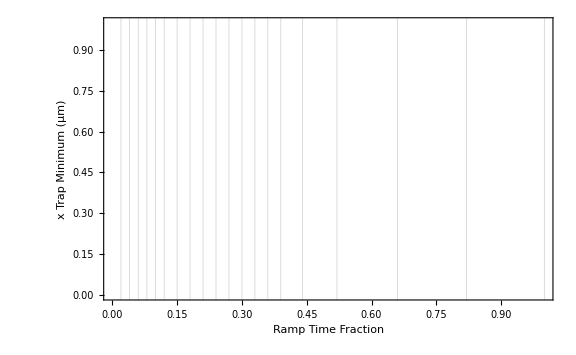
-Graphics-Show[ListLogPlot[Transpose[{{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,1/2,51/100,13/25,53/100,27/50,11/20,14/25,57/100,29/50,59/100,3/5,61/100,31/50,63/100,16/25,13/20,33/50,67/100,17/25,69/100,7/10,71/100,18/25,73/100,37/50,3/4,19/25,77/100,39/50,79/100,4/5,81/100,41/50,83/100,21/25,17/20,43/50,87/100,22/25,89/100,9/10,91/100,23/25,93/100,47/50,19/20,24/25,97/100,49/50,99/100,1},{{z0[0.8505,2.401,2.3,-8.9375,36.6722,1.5552]⟦All,2⟧,-8.9375,ChipTrapField[z0[0.8505,2.401,2.3,-8.9375,36.6722,1.5552],All,2,0.8505,2.401,2.3,-8.9375,36.6722,1.5552]},{z0[-0.00991 (0.8505-1. CurrL),-0.00991 (2.401-1. CurrZ),-0.00991 (2.3-1. CurrH),-0.00991 (-8.9375-1. Bx1),-0.00991 (36.6722-1. By1),-0.00991 (1.5552-1. Bz1)],-8.9375-0.00991 (-8.9375-1. Bx1),ChipTrapField[-0.00991 (0.8505-1. CurrL),-0.00991 (2.401-1. CurrZ),-0.00991 (2.3-1. CurrH),0.8505-0.00991 (0.8505-1. CurrL),2.401-0.00991 (2.401-1. CurrZ),2.3-0.00991 (2.3-1. CurrH),-8.9375-0.00991 (-8.9375-1. Bx1),36.6722-0.00991 (36.6722-1. By1),1.5552-0.00991 (1.5552-1. Bz1)]},{z0[-0.01982 (0.8505-1. CurrL),-0.01982 (2.401-1. CurrZ),-0.01982 (2.3-1. CurrH),-0.01982 (-8.9375-1. Bx1),-0.01982 (36.6722-1. By1),-0.01982 (1.5552-1. Bz1)],-8.9375-0.01982 (-8.9375-1. Bx1),ChipTrapField[-0.01982 (0.8505-1. CurrL),-0.01982 (2.401-1. CurrZ),-0.01982 (2.3-1. CurrH),0.8505-0.01982 (0.8505-1. CurrL),2.401-0.01982 (2.401-1. CurrZ),2.3-0.01982 (2.3-1. CurrH),-8.9375-0.01982 (-8.9375-1. Bx1),36.6722-0.01982 (36.6722-1. By1),1.5552-0.01982 (1.5552-1. Bz1)]},{z0[-0.04021 (0.8505-1. CurrL),-0.04021 (2.401-1. CurrZ),-0.04021 (2.3-1. CurrH),-0.04021 (-8.9375-1. Bx1),-0.04021 (36.6722-1. By1),-0.04021 (1.5552-1. Bz1)],-8.9375-0.04021 (-8.9375-1. Bx1),ChipTrapField[-0.04021 (0.8505-1. CurrL),-0.04021 (2.401-1. CurrZ),-0.04021 (2.3-1. CurrH),0.8505-0.04021 (0.8505-1. CurrL),2.401-0.04021 (2.401-1. CurrZ),2.3-0.04021 (2.3-1. CurrH),-8.9375-0.04021 (-8.9375-1. Bx1),36.6722-0.04021 (36.6722-1. By1),1.5552-0.04021 (1.5552-1. Bz1)]},{z0[-0.0606 (0.8505-1. CurrL),-0.0606 (2.401-1. CurrZ),-0.0606 (2.3-1. CurrH),-0.0606 (-8.9375-1. Bx1),-0.0606 (36.6722-1. By1),-0.0606 (1.5552-1. Bz1)],-8.9375-0.0606 (-8.9375-1. Bx1),ChipTrapField[-0.0606 (0.8505-1. CurrL),-0.0606 (2.401-1. CurrZ),-0.0606 (2.3-1. CurrH),0.8505-0.0606 (0.8505-1. CurrL),2.401-0.0606 (2.401-1. CurrZ),2.3-0.0606 (2.3-1. CurrH),-8.9375-0.0606 (-8.9375-1. Bx1),36.6722-0.0606 (36.6722-1. By1),1.5552-0.0606 (1.5552-1. Bz1)]},{z0[-0.092385 (0.8505-1. CurrL),-0.092385 (2.401-1. CurrZ),-0.092385 (2.3-1. CurrH),-0.092385 (-8.9375-1. Bx1),-0.092385 (36.6722-1. By1),-0.092385 (1.5552-1. Bz1)],-8.9375-0.092385 (-8.9375-1. Bx1),ChipTrapField[-0.092385 (0.8505-1. CurrL),-0.092385 (2.401-1. CurrZ),-0.092385 (2.3-1. CurrH),0.8505-0.092385 (0.8505-1. CurrL),2.401-0.092385 (2.401-1. CurrZ),2.3-0.092385 (2.3-1. CurrH),-8.9375-0.092385 (-8.9375-1. Bx1),36.6722-0.092385 (36.6722-1. By1),1.5552-0.092385 (1.5552-1. Bz1)]},{z0[-0.12417 (0.8505-1. CurrL),-0.12417 (2.401-1. CurrZ),-0.12417 (2.3-1. CurrH),-0.12417 (-8.9375-1. Bx1),-0.12417 (36.6722-1. By1),-0.12417 (1.5552-1. Bz1)],-8.9375-0.12417 (-8.9375-1. Bx1),ChipTrapField[-0.12417 (0.8505-1. CurrL),-0.12417 (2.401-1. CurrZ),-0.12417 (2.3-1. CurrH),0.8505-0.12417 (0.8505-1. CurrL),2.401-0.12417 (2.401-1. CurrZ),2.3-0.12417 (2.3-1. CurrH),-8.9375-0.12417 (-8.9375-1. Bx1),36.6722-0.12417 (36.6722-1. By1),1.5552-0.12417 (1.5552-1. Bz1)]},{z0[-0.165495 (0.8505-1. CurrL),-0.165495 (2.401-1. CurrZ),-0.165495 (2.3-1. CurrH),-0.165495 (-8.9375-1. Bx1),-0.165495 (36.6722-1. By1),-0.165495 (1.5552-1. Bz1)],-8.9375-0.165495 (-8.9375-1. Bx1),ChipTrapField[-0.165495 (0.8505-1. CurrL),-0.165495 (2.401-1. CurrZ),-0.165495 (2.3-1. CurrH),0.8505-0.165495 (0.8505-1. CurrL),2.401-0.165495 (2.401-1. CurrZ),2.3-0.165495 (2.3-1. CurrH),-8.9375-0.165495 (-8.9375-1. Bx1),36.6722-0.165495 (36.6722-1. By1),1.5552-0.165495 (1.5552-1. Bz1)]},{z0[-0.20682 (0.8505-1. CurrL),-0.20682 (2.401-1. CurrZ),-0.20682 (2.3-1. CurrH),-0.20682 (-8.9375-1. Bx1),-0.20682 (36.6722-1. By1),-0.20682 (1.5552-1. Bz1)],-8.9375-0.20682 (-8.9375-1. Bx1),ChipTrapField[-0.20682 (0.8505-1. CurrL),-0.20682 (2.401-1. CurrZ),-0.20682 (2.3-1. CurrH),0.8505-0.20682 (0.8505-1. CurrL),2.401-0.20682 (2.401-1. CurrZ),2.3-0.20682 (2.3-1. CurrH),-8.9375-0.20682 (-8.9375-1. Bx1),36.6722-0.20682 (36.6722-1. By1),1.5552-0.20682 (1.5552-1. Bz1)]},{z0[-0.25314 (0.8505-1. CurrL),-0.25314 (2.401-1. CurrZ),-0.25314 (2.3-1. CurrH),-0.25314 (-8.9375-1. Bx1),-0.25314 (36.6722-1. By1),-0.25314 (1.5552-1. Bz1)],-8.9375-0.25314 (-8.9375-1. Bx1),ChipTrapField[-0.25314 (0.8505-1. CurrL),-0.25314 (2.401-1. CurrZ),-0.25314 (2.3-1. CurrH),0.8505-0.25314 (0.8505-1. CurrL),2.401-0.25314 (2.401-1. CurrZ),2.3-0.25314 (2.3-1. CurrH),-8.9375-0.25314 (-8.9375-1. Bx1),36.6722-0.25314 (36.6722-1. By1),1.5552-0.25314 (1.5552-1. Bz1)]},{z0[-0.29946 (0.8505-1. CurrL),-0.29946 (2.401-1. CurrZ),-0.29946 (2.3-1. CurrH),-0.29946 (-8.9375-1. Bx1),-0.29946 (36.6722-1. By1),-0.29946 (1.5552-1. Bz1)],-8.9375-0.29946 (-8.9375-1. Bx1),ChipTrapField[-0.29946 (0.8505-1. CurrL),-0.29946 (2.401-1. CurrZ),-0.29946 (2.3-1. CurrH),0.8505-0.29946 (0.8505-1. CurrL),2.401-0.29946 (2.401-1. CurrZ),2.3-0.29946 (2.3-1. CurrH),-8.9375-0.29946 (-8.9375-1. Bx1),36.6722-0.29946 (36.6722-1. By1),1.5552-0.29946 (1.5552-1. Bz1)]},{z0[-0.34699 (0.8505-1. CurrL),-0.34699 (2.401-1. CurrZ),-0.34699 (2.3-1. CurrH),-0.34699 (-8.9375-1. Bx1),-0.34699 (36.6722-1. By1),-0.34699 (1.5552-1. Bz1)],-8.9375-0.34699 (-8.9375-1. Bx1),ChipTrapField[-0.34699 (0.8505-1. CurrL),-0.34699 (2.401-1. CurrZ),-0.34699 (2.3-1. CurrH),0.8505-0.34699 (0.8505-1. CurrL),2.401-0.34699 (2.401-1. CurrZ),2.3-0.34699 (2.3-1. CurrH),-8.9375-0.34699 (-8.9375-1. Bx1),36.6722-0.34699 (36.6722-1. By1),1.5552-0.34699 (1.5552-1. Bz1)]},{z0[-0.39452 (0.8505-1. CurrL),-0.39452 (2.401-1. CurrZ),-0.39452 (2.3-1. CurrH),-0.39452 (-8.9375-1. Bx1),-0.39452 (36.6722-1. By1),-0.39452 (1.5552-1. Bz1)],-8.9375-0.39452 (-8.9375-1. Bx1),ChipTrapField[-0.39452 (0.8505-1. CurrL),-0.39452 (2.401-1. CurrZ),-0.39452 (2.3-1. CurrH),0.8505-0.39452 (0.8505-1. CurrL),2.401-0.39452 (2.401-1. CurrZ),2.3-0.39452 (2.3-1. CurrH),-8.9375-0.39452 (-8.9375-1. Bx1),36.6722-0.39452 (36.6722-1. By1),1.5552-0.39452 (1.5552-1. Bz1)]},{z0[-0.438723 (0.8505-1. CurrL),-0.438723 (2.401-1. CurrZ),-0.438723 (2.3-1. CurrH),-0.438723 (-8.9375-1. Bx1),-0.438723 (36.6722-1. By1),-0.438723 (1.5552-1. Bz1)],-8.9375-0.438723 (-8.9375-1. Bx1),ChipTrapField[-0.438723 (0.8505-1. CurrL),-0.438723 (2.401-1. CurrZ),-0.438723 (2.3-1. CurrH),0.8505-0.438723 (0.8505-1. CurrL),2.401-0.438723 (2.401-1. CurrZ),2.3-0.438723 (2.3-1. CurrH),-8.9375-0.438723 (-8.9375-1. Bx1),36.6722-0.438723 (36.6722-1. By1),1.5552-0.438723 (1.5552-1. Bz1)]},{z0[-0.482927 (0.8505-1. CurrL),-0.482927 (2.401-1. CurrZ),-0.482927 (2.3-1. CurrH),-0.482927 (-8.9375-1. Bx1),-0.482927 (36.6722-1. By1),-0.482927 (1.5552-1. Bz1)],-8.9375-0.482927 (-8.9375-1. Bx1),ChipTrapField[-0.482927 (0.8505-1. CurrL),-0.482927 (2.401-1. CurrZ),-0.482927 (2.3-1. CurrH),0.8505-0.482927 (0.8505-1. CurrL),2.401-0.482927 (2.401-1. CurrZ),2.3-0.482927 (2.3-1. CurrH),-8.9375-0.482927 (-8.9375-1. Bx1),36.6722-0.482927 (36.6722-1. By1),1.5552-0.482927 (1.5552-1. Bz1)]},{z0[-0.52713 (0.8505-1. CurrL),-0.52713 (2.401-1. CurrZ),-0.52713 (2.3-1. CurrH),-0.52713 (-8.9375-1. Bx1),-0.52713 (36.6722-1. By1),-0.52713 (1.5552-1. Bz1)],-8.9375-0.52713 (-8.9375-1. Bx1),ChipTrapField[-0.52713 (0.8505-1. CurrL),-0.52713 (2.401-1. CurrZ),-0.52713 (2.3-1. CurrH),0.8505-0.52713 (0.8505-1. CurrL),2.401-0.52713 (2.401-1. CurrZ),2.3-0.52713 (2.3-1. CurrH),-8.9375-0.52713 (-8.9375-1. Bx1),36.6722-0.52713 (36.6722-1. By1),1.5552-0.52713 (1.5552-1. Bz1)]},{z0[-0.56413 (0.8505-1. CurrL),-0.56413 (2.401-1. CurrZ),-0.56413 (2.3-1. CurrH),-0.56413 (-8.9375-1. Bx1),-0.56413 (36.6722-1. By1),-0.56413 (1.5552-1. Bz1)],-8.9375-0.56413 (-8.9375-1. Bx1),ChipTrapField[-0.56413 (0.8505-1. CurrL),-0.56413 (2.401-1. CurrZ),-0.56413 (2.3-1. CurrH),0.8505-0.56413 (0.8505-1. CurrL),2.401-0.56413 (2.401-1. CurrZ),2.3-0.56413 (2.3-1. CurrH),-8.9375-0.56413 (-8.9375-1. Bx1),36.6722-0.56413 (36.6722-1. By1),1.5552-0.56413 (1.5552-1. Bz1)]},{z0[-0.60113 (0.8505-1. CurrL),-0.60113 (2.401-1. CurrZ),-0.60113 (2.3-1. CurrH),-0.60113 (-8.9375-1. Bx1),-0.60113 (36.6722-1. By1),-0.60113 (1.5552-1. Bz1)],-8.9375-0.60113 (-8.9375-1. Bx1),ChipTrapField[-0.60113 (0.8505-1. CurrL),-0.60113 (2.401-1. CurrZ),-0.60113 (2.3-1. CurrH),0.8505-0.60113 (0.8505-1. CurrL),2.401-0.60113 (2.401-1. CurrZ),2.3-0.60113 (2.3-1. CurrH),-8.9375-0.60113 (-8.9375-1. Bx1),36.6722-0.60113 (36.6722-1. By1),1.5552-0.60113 (1.5552-1. Bz1)]},{z0[-0.63813 (0.8505-1. CurrL),-0.63813 (2.401-1. CurrZ),-0.63813 (2.3-1. CurrH),-0.63813 (-8.9375-1. Bx1),-0.63813 (36.6722-1. By1),-0.63813 (1.5552-1. Bz1)],-8.9375-0.63813 (-8.9375-1. Bx1),ChipTrapField[-0.63813 (0.8505-1. CurrL),-0.63813 (2.401-1. CurrZ),-0.63813 (2.3-1. CurrH),0.8505-0.63813 (0.8505-1. CurrL),2.401-0.63813 (2.401-1. CurrZ),2.3-0.63813 (2.3-1. CurrH),-8.9375-0.63813 (-8.9375-1. Bx1),36.6722-0.63813 (36.6722-1. By1),1.5552-0.63813 (1.5552-1. Bz1)]},{z0[-0.66735 (0.8505-1. CurrL),-0.66735 (2.401-1. CurrZ),-0.66735 (2.3-1. CurrH),-0.66735 (-8.9375-1. Bx1),-0.66735 (36.6722-1. By1),-0.66735 (1.5552-1. Bz1)],-8.9375-0.66735 (-8.9375-1. Bx1),ChipTrapField[-0.66735 (0.8505-1. CurrL),-0.66735 (2.401-1. CurrZ),-0.66735 (2.3-1. CurrH),0.8505-0.66735 (0.8505-1. CurrL),2.401-0.66735 (2.401-1. CurrZ),2.3-0.66735 (2.3-1. CurrH),-8.9375-0.66735 (-8.9375-1. Bx1),36.6722-0.66735 (36.6722-1. By1),1.5552-0.66735 (1.5552-1. Bz1)]},{z0[-0.69657 (0.8505-1. CurrL),-0.69657 (2.401-1. CurrZ),-0.69657 (2.3-1. CurrH),-0.69657 (-8.9375-1. Bx1),-0.69657 (36.6722-1. By1),-0.69657 (1.5552-1. Bz1)],-8.9375-0.69657 (-8.9375-1. Bx1),ChipTrapField[-0.69657 (0.8505-1. CurrL),-0.69657 (2.401-1. CurrZ),-0.69657 (2.3-1. CurrH),0.8505-0.69657 (0.8505-1. CurrL),2.401-0.69657 (2.401-1. CurrZ),2.3-0.69657 (2.3-1. CurrH),-8.9375-0.69657 (-8.9375-1. Bx1),36.6722-0.69657 (36.6722-1. By1),1.5552-0.69657 (1.5552-1. Bz1)]},{z0[-0.72579 (0.8505-1. CurrL),-0.72579 (2.401-1. CurrZ),-0.72579 (2.3-1. CurrH),-0.72579 (-8.9375-1. Bx1),-0.72579 (36.6722-1. By1),-0.72579 (1.5552-1. Bz1)],-8.9375-0.72579 (-8.9375-1. Bx1),ChipTrapField[-0.72579 (0.8505-1. CurrL),-0.72579 (2.401-1. CurrZ),-0.72579 (2.3-1. CurrH),0.8505-0.72579 (0.8505-1. CurrL),2.401-0.72579 (2.401-1. CurrZ),2.3-0.72579 (2.3-1. CurrH),-8.9375-0.72579 (-8.9375-1. Bx1),36.6722-0.72579 (36.6722-1. By1),1.5552-0.72579 (1.5552-1. Bz1)]},{z0[-0.747893 (0.8505-1. CurrL),-0.747893 (2.401-1. CurrZ),-0.747893 (2.3-1. CurrH),-0.747893 (-8.9375-1. Bx1),-0.747893 (36.6722-1. By1),-0.747893 (1.5552-1. Bz1)],-8.9375-0.747893 (-8.9375-1. Bx1),ChipTrapField[-0.747893 (0.8505-1. CurrL),-0.747893 (2.401-1. CurrZ),-0.747893 (2.3-1. CurrH),0.8505-0.747893 (0.8505-1. CurrL),2.401-0.747893 (2.401-1. CurrZ),2.3-0.747893 (2.3-1. CurrH),-8.9375-0.747893 (-8.9375-1. Bx1),36.6722-0.747893 (36.6722-1. By1),1.5552-0.747893 (1.5552-1. Bz1)]},{z0[-0.769997 (0.8505-1. CurrL),-0.769997 (2.401-1. CurrZ),-0.769997 (2.3-1. CurrH),-0.769997 (-8.9375-1. Bx1),-0.769997 (36.6722-1. By1),-0.769997 (1.5552-1. Bz1)],-8.9375-0.769997 (-8.9375-1. Bx1),ChipTrapField[-0.769997 (0.8505-1. CurrL),-0.769997 (2.401-1. CurrZ),-0.769997 (2.3-1. CurrH),0.8505-0.769997 (0.8505-1. CurrL),2.401-0.769997 (2.401-1. CurrZ),2.3-0.769997 (2.3-1. CurrH),-8.9375-0.769997 (-8.9375-1. Bx1),36.6722-0.769997 (36.6722-1. By1),1.5552-0.769997 (1.5552-1. Bz1)]},{z0[-0.7921 (0.8505-1. CurrL),-0.7921 (2.401-1. CurrZ),-0.7921 (2.3-1. CurrH),-0.7921 (-8.9375-1. Bx1),-0.7921 (36.6722-1. By1),-0.7921 (1.5552-1. Bz1)],-8.9375-0.7921 (-8.9375-1. Bx1),ChipTrapField[-0.7921 (0.8505-1. CurrL),-0.7921 (2.401-1. CurrZ),-0.7921 (2.3-1. CurrH),0.8505-0.7921 (0.8505-1. CurrL),2.401-0.7921 (2.401-1. CurrZ),2.3-0.7921 (2.3-1. CurrH),-8.9375-0.7921 (-8.9375-1. Bx1),36.6722-0.7921 (36.6722-1. By1),1.5552-0.7921 (1.5552-1. Bz1)]},{z0[-0.80891 (0.8505-1. CurrL),-0.80891 (2.401-1. CurrZ),-0.80891 (2.3-1. CurrH),-0.80891 (-8.9375-1. Bx1),-0.80891 (36.6722-1. By1),-0.80891 (1.5552-1. Bz1)],-8.9375-0.80891 (-8.9375-1. Bx1),ChipTrapField[-0.80891 (0.8505-1. CurrL),-0.80891 (2.401-1. CurrZ),-0.80891 (2.3-1. CurrH),0.8505-0.80891 (0.8505-1. CurrL),2.401-0.80891 (2.401-1. CurrZ),2.3-0.80891 (2.3-1. CurrH),-8.9375-0.80891 (-8.9375-1. Bx1),36.6722-0.80891 (36.6722-1. By1),1.5552-0.80891 (1.5552-1. Bz1)]},{z0[-0.82572 (0.8505-1. CurrL),-0.82572 (2.401-1. CurrZ),-0.82572 (2.3-1. CurrH),-0.82572 (-8.9375-1. Bx1),-0.82572 (36.6722-1. By1),-0.82572 (1.5552-1. Bz1)],-8.9375-0.82572 (-8.9375-1. Bx1),ChipTrapField[-0.82572 (0.8505-1. CurrL),-0.82572 (2.401-1. CurrZ),-0.82572 (2.3-1. CurrH),0.8505-0.82572 (0.8505-1. CurrL),2.401-0.82572 (2.401-1. CurrZ),2.3-0.82572 (2.3-1. CurrH),-8.9375-0.82572 (-8.9375-1. Bx1),36.6722-0.82572 (36.6722-1. By1),1.5552-0.82572 (1.5552-1. Bz1)]},{z0[-0.84253 (0.8505-1. CurrL),-0.84253 (2.401-1. CurrZ),-0.84253 (2.3-1. CurrH),-0.84253 (-8.9375-1. Bx1),-0.84253 (36.6722-1. By1),-0.84253 (1.5552-1. Bz1)],-8.9375-0.84253 (-8.9375-1. Bx1),ChipTrapField[-0.84253 (0.8505-1. CurrL),-0.84253 (2.401-1. CurrZ),-0.84253 (2.3-1. CurrH),0.8505-0.84253 (0.8505-1. CurrL),2.401-0.84253 (2.401-1. CurrZ),2.3-0.84253 (2.3-1. CurrH),-8.9375-0.84253 (-8.9375-1. Bx1),36.6722-0.84253 (36.6722-1. By1),1.5552-0.84253 (1.5552-1. Bz1)]},{z0[-0.855073 (0.8505-1. CurrL),-0.855073 (2.401-1. CurrZ),-0.855073 (2.3-1. CurrH),-0.855073 (-8.9375-1. Bx1),-0.855073 (36.6722-1. By1),-0.855073 (1.5552-1. Bz1)],-8.9375-0.855073 (-8.9375-1. Bx1),ChipTrapField[-0.855073 (0.8505-1. CurrL),-0.855073 (2.401-1. CurrZ),-0.855073 (2.3-1. CurrH),0.8505-0.855073 (0.8505-1. CurrL),2.401-0.855073 (2.401-1. CurrZ),2.3-0.855073 (2.3-1. CurrH),-8.9375-0.855073 (-8.9375-1. Bx1),36.6722-0.855073 (36.6722-1. By1),1.5552-0.855073 (1.5552-1. Bz1)]},{z0[-0.867617 (0.8505-1. CurrL),-0.867617 (2.401-1. CurrZ),-0.867617 (2.3-1. CurrH),-0.867617 (-8.9375-1. Bx1),-0.867617 (36.6722-1. By1),-0.867617 (1.5552-1. Bz1)],-8.9375-0.867617 (-8.9375-1. Bx1),ChipTrapField[-0.867617 (0.8505-1. CurrL),-0.867617 (2.401-1. CurrZ),-0.867617 (2.3-1. CurrH),0.8505-0.867617 (0.8505-1. CurrL),2.401-0.867617 (2.401-1. CurrZ),2.3-0.867617 (2.3-1. CurrH),-8.9375-0.867617 (-8.9375-1. Bx1),36.6722-0.867617 (36.6722-1. By1),1.5552-0.867617 (1.5552-1. Bz1)]},{z0[-0.88016 (0.8505-1. CurrL),-0.88016 (2.401-1. CurrZ),-0.88016 (2.3-1. CurrH),-0.88016 (-8.9375-1. Bx1),-0.88016 (36.6722-1. By1),-0.88016 (1.5552-1. Bz1)],-8.9375-0.88016 (-8.9375-1. Bx1),ChipTrapField[-0.88016 (0.8505-1. CurrL),-0.88016 (2.401-1. CurrZ),-0.88016 (2.3-1. CurrH),0.8505-0.88016 (0.8505-1. CurrL),2.401-0.88016 (2.401-1. CurrZ),2.3-0.88016 (2.3-1. CurrH),-8.9375-0.88016 (-8.9375-1. Bx1),36.6722-0.88016 (36.6722-1. By1),1.5552-0.88016 (1.5552-1. Bz1)]},{z0[-0.88944 (0.8505-1. CurrL),-0.88944 (2.401-1. CurrZ),-0.88944 (2.3-1. CurrH),-0.88944 (-8.9375-1. Bx1),-0.88944 (36.6722-1. By1),-0.88944 (1.5552-1. Bz1)],-8.9375-0.88944 (-8.9375-1. Bx1),ChipTrapField[-0.88944 (0.8505-1. CurrL),-0.88944 (2.401-1. CurrZ),-0.88944 (2.3-1. CurrH),0.8505-0.88944 (0.8505-1. CurrL),2.401-0.88944 (2.401-1. CurrZ),2.3-0.88944 (2.3-1. CurrH),-8.9375-0.88944 (-8.9375-1. Bx1),36.6722-0.88944 (36.6722-1. By1),1.5552-0.88944 (1.5552-1. Bz1)]},{z0[-0.89872 (0.8505-1. CurrL),-0.89872 (2.401-1. CurrZ),-0.89872 (2.3-1. CurrH),-0.89872 (-8.9375-1. Bx1),-0.89872 (36.6722-1. By1),-0.89872 (1.5552-1. Bz1)],-8.9375-0.89872 (-8.9375-1. Bx1),ChipTrapField[-0.89872 (0.8505-1. CurrL),-0.89872 (2.401-1. CurrZ),-0.89872 (2.3-1. CurrH),0.8505-0.89872 (0.8505-1. CurrL),2.401-0.89872 (2.401-1. CurrZ),2.3-0.89872 (2.3-1. CurrH),-8.9375-0.89872 (-8.9375-1. Bx1),36.6722-0.89872 (36.6722-1. By1),1.5552-0.89872 (1.5552-1. Bz1)]},{z0[-0.908 (0.8505-1. CurrL),-0.908 (2.401-1. CurrZ),-0.908 (2.3-1. CurrH),-0.908 (-8.9375-1. Bx1),-0.908 (36.6722-1. By1),-0.908 (1.5552-1. Bz1)],-8.9375-0.908 (-8.9375-1. Bx1),ChipTrapField[-0.908 (0.8505-1. CurrL),-0.908 (2.401-1. CurrZ),-0.908 (2.3-1. CurrH),0.8505-0.908 (0.8505-1. CurrL),2.401-0.908 (2.401-1. CurrZ),2.3-0.908 (2.3-1. CurrH),-8.9375-0.908 (-8.9375-1. Bx1),36.6722-0.908 (36.6722-1. By1),1.5552-0.908 (1.5552-1. Bz1)]},{z0[-0.914953 (0.8505-1. CurrL),-0.914953 (2.401-1. CurrZ),-0.914953 (2.3-1. CurrH),-0.914953 (-8.9375-1. Bx1),-0.914953 (36.6722-1. By1),-0.914953 (1.5552-1. Bz1)],-8.9375-0.914953 (-8.9375-1. Bx1),ChipTrapField[-0.914953 (0.8505-1. CurrL),-0.914953 (2.401-1. CurrZ),-0.914953 (2.3-1. CurrH),0.8505-0.914953 (0.8505-1. CurrL),2.401-0.914953 (2.401-1. CurrZ),2.3-0.914953 (2.3-1. CurrH),-8.9375-0.914953 (-8.9375-1. Bx1),36.6722-0.914953 (36.6722-1. By1),1.5552-0.914953 (1.5552-1. Bz1)]},{z0[-0.921907 (0.8505-1. CurrL),-0.921907 (2.401-1. CurrZ),-0.921907 (2.3-1. CurrH),-0.921907 (-8.9375-1. Bx1),-0.921907 (36.6722-1. By1),-0.921907 (1.5552-1. Bz1)],-8.9375-0.921907 (-8.9375-1. Bx1),ChipTrapField[-0.921907 (0.8505-1. CurrL),-0.921907 (2.401-1. CurrZ),-0.921907 (2.3-1. CurrH),0.8505-0.921907 (0.8505-1. CurrL),2.401-0.921907 (2.401-1. CurrZ),2.3-0.921907 (2.3-1. CurrH),-8.9375-0.921907 (-8.9375-1. Bx1),36.6722-0.921907 (36.6722-1. By1),1.5552-0.921907 (1.5552-1. Bz1)]},{z0[-0.92886 (0.8505-1. CurrL),-0.92886 (2.401-1. CurrZ),-0.92886 (2.3-1. CurrH),-0.92886 (-8.9375-1. Bx1),-0.92886 (36.6722-1. By1),-0.92886 (1.5552-1. Bz1)],-8.9375-0.92886 (-8.9375-1. Bx1),ChipTrapField[-0.92886 (0.8505-1. CurrL),-0.92886 (2.401-1. CurrZ),-0.92886 (2.3-1. CurrH),0.8505-0.92886 (0.8505-1. CurrL),2.401-0.92886 (2.401-1. CurrZ),2.3-0.92886 (2.3-1. CurrH),-8.9375-0.92886 (-8.9375-1. Bx1),36.6722-0.92886 (36.6722-1. By1),1.5552-0.92886 (1.5552-1. Bz1)]},{z0[-0.934007 (0.8505-1. CurrL),-0.934007 (2.401-1. CurrZ),-0.934007 (2.3-1. CurrH),-0.934007 (-8.9375-1. Bx1),-0.934007 (36.6722-1. By1),-0.934007 (1.5552-1. Bz1)],-8.9375-0.934007 (-8.9375-1. Bx1),ChipTrapField[-0.934007 (0.8505-1. CurrL),-0.934007 (2.401-1. CurrZ),-0.934007 (2.3-1. CurrH),0.8505-0.934007 (0.8505-1. CurrL),2.401-0.934007 (2.401-1. CurrZ),2.3-0.934007 (2.3-1. CurrH),-8.9375-0.934007 (-8.9375-1. Bx1),36.6722-0.934007 (36.6722-1. By1),1.5552-0.934007 (1.5552-1. Bz1)]},{z0[-0.939153 (0.8505-1. CurrL),-0.939153 (2.401-1. CurrZ),-0.939153 (2.3-1. CurrH),-0.939153 (-8.9375-1. Bx1),-0.939153 (36.6722-1. By1),-0.939153 (1.5552-1. Bz1)],-8.9375-0.939153 (-8.9375-1. Bx1),ChipTrapField[-0.939153 (0.8505-1. CurrL),-0.939153 (2.401-1. CurrZ),-0.939153 (2.3-1. CurrH),0.8505-0.939153 (0.8505-1. CurrL),2.401-0.939153 (2.401-1. CurrZ),2.3-0.939153 (2.3-1. CurrH),-8.9375-0.939153 (-8.9375-1. Bx1),36.6722-0.939153 (36.6722-1. By1),1.5552-0.939153 (1.5552-1. Bz1)]},{z0[-0.9443 (0.8505-1. CurrL),-0.9443 (2.401-1. CurrZ),-0.9443 (2.3-1. CurrH),-0.9443 (-8.9375-1. Bx1),-0.9443 (36.6722-1. By1),-0.9443 (1.5552-1. Bz1)],-8.9375-0.9443 (-8.9375-1. Bx1),ChipTrapField[-0.9443 (0.8505-1. CurrL),-0.9443 (2.401-1. CurrZ),-0.9443 (2.3-1. CurrH),0.8505-0.9443 (0.8505-1. CurrL),2.401-0.9443 (2.401-1. CurrZ),2.3-0.9443 (2.3-1. CurrH),-8.9375-0.9443 (-8.9375-1. Bx1),36.6722-0.9443 (36.6722-1. By1),1.5552-0.9443 (1.5552-1. Bz1)]},{z0[-0.947978 (0.8505-1. CurrL),-0.947978 (2.401-1. CurrZ),-0.947978 (2.3-1. CurrH),-0.947978 (-8.9375-1. Bx1),-0.947978 (36.6722-1. By1),-0.947978 (1.5552-1. Bz1)],-8.9375-0.947978 (-8.9375-1. Bx1),ChipTrapField[-0.947978 (0.8505-1. CurrL),-0.947978 (2.401-1. CurrZ),-0.947978 (2.3-1. CurrH),0.8505-0.947978 (0.8505-1. CurrL),2.401-0.947978 (2.401-1. CurrZ),2.3-0.947978 (2.3-1. CurrH),-8.9375-0.947978 (-8.9375-1. Bx1),36.6722-0.947978 (36.6722-1. By1),1.5552-0.947978 (1.5552-1. Bz1)]},{z0[-0.951656 (0.8505-1. CurrL),-0.951656 (2.401-1. CurrZ),-0.951656 (2.3-1. CurrH),-0.951656 (-8.9375-1. Bx1),-0.951656 (36.6722-1. By1),-0.951656 (1.5552-1. Bz1)],-8.9375-0.951656 (-8.9375-1. Bx1),ChipTrapField[-0.951656 (0.8505-1. CurrL),-0.951656 (2.401-1. CurrZ),-0.951656 (2.3-1. CurrH),0.8505-0.951656 (0.8505-1. CurrL),2.401-0.951656 (2.401-1. CurrZ),2.3-0.951656 (2.3-1. CurrH),-8.9375-0.951656 (-8.9375-1. Bx1),36.6722-0.951656 (36.6722-1. By1),1.5552-0.951656 (1.5552-1. Bz1)]},{z0[-0.955334 (0.8505-1. CurrL),-0.955334 (2.401-1. CurrZ),-0.955334 (2.3-1. CurrH),-0.955334 (-8.9375-1. Bx1),-0.955334 (36.6722-1. By1),-0.955334 (1.5552-1. Bz1)],-8.9375-0.955334 (-8.9375-1. Bx1),ChipTrapField[-0.955334 (0.8505-1. CurrL),-0.955334 (2.401-1. CurrZ),-0.955334 (2.3-1. CurrH),0.8505-0.955334 (0.8505-1. CurrL),2.401-0.955334 (2.401-1. CurrZ),2.3-0.955334 (2.3-1. CurrH),-8.9375-0.955334 (-8.9375-1. Bx1),36.6722-0.955334 (36.6722-1. By1),1.5552-0.955334 (1.5552-1. Bz1)]},{z0[-0.959012 (0.8505-1. CurrL),-0.959012 (2.401-1. CurrZ),-0.959012 (2.3-1. CurrH),-0.959012 (-8.9375-1. Bx1),-0.959012 (36.6722-1. By1),-0.959012 (1.5552-1. Bz1)],-8.9375-0.959012 (-8.9375-1. Bx1),ChipTrapField[-0.959012 (0.8505-1. CurrL),-0.959012 (2.401-1. CurrZ),-0.959012 (2.3-1. CurrH),0.8505-0.959012 (0.8505-1. CurrL),2.401-0.959012 (2.401-1. CurrZ),2.3-0.959012 (2.3-1. CurrH),-8.9375-0.959012 (-8.9375-1. Bx1),36.6722-0.959012 (36.6722-1. By1),1.5552-0.959012 (1.5552-1. Bz1)]},{z0[-0.96269 (0.8505-1. CurrL),-0.96269 (2.401-1. CurrZ),-0.96269 (2.3-1. CurrH),-0.96269 (-8.9375-1. Bx1),-0.96269 (36.6722-1. By1),-0.96269 (1.5552-1. Bz1)],-8.9375-0.96269 (-8.9375-1. Bx1),ChipTrapField[-0.96269 (0.8505-1. CurrL),-0.96269 (2.401-1. CurrZ),-0.96269 (2.3-1. CurrH),0.8505-0.96269 (0.8505-1. CurrL),2.401-0.96269 (2.401-1. CurrZ),2.3-0.96269 (2.3-1. CurrH),-8.9375-0.96269 (-8.9375-1. Bx1),36.6722-0.96269 (36.6722-1. By1),1.5552-0.96269 (1.5552-1. Bz1)]},{z0[-0.964795 (0.8505-1. CurrL),-0.964795 (2.401-1. CurrZ),-0.964795 (2.3-1. CurrH),-0.964795 (-8.9375-1. Bx1),-0.964795 (36.6722-1. By1),-0.964795 (1.5552-1. Bz1)],-8.9375-0.964795 (-8.9375-1. Bx1),ChipTrapField[-0.964795 (0.8505-1. CurrL),-0.964795 (2.401-1. CurrZ),-0.964795 (2.3-1. CurrH),0.8505-0.964795 (0.8505-1. CurrL),2.401-0.964795 (2.401-1. CurrZ),2.3-0.964795 (2.3-1. CurrH),-8.9375-0.964795 (-8.9375-1. Bx1),36.6722-0.964795 (36.6722-1. By1),1.5552-0.964795 (1.5552-1. Bz1)]},{z0[-0.9669 (0.8505-1. CurrL),-0.9669 (2.401-1. CurrZ),-0.9669 (2.3-1. CurrH),-0.9669 (-8.9375-1. Bx1),-0.9669 (36.6722-1. By1),-0.9669 (1.5552-1. Bz1)],-8.9375-0.9669 (-8.9375-1. Bx1),ChipTrapField[-0.9669 (0.8505-1. CurrL),-0.9669 (2.401-1. CurrZ),-0.9669 (2.3-1. CurrH),0.8505-0.9669 (0.8505-1. CurrL),2.401-0.9669 (2.401-1. CurrZ),2.3-0.9669 (2.3-1. CurrH),-8.9375-0.9669 (-8.9375-1. Bx1),36.6722-0.9669 (36.6722-1. By1),1.5552-0.9669 (1.5552-1. Bz1)]},{z0[-0.969005 (0.8505-1. CurrL),-0.969005 (2.401-1. CurrZ),-0.969005 (2.3-1. CurrH),-0.969005 (-8.9375-1. Bx1),-0.969005 (36.6722-1. By1),-0.969005 (1.5552-1. Bz1)],-8.9375-0.969005 (-8.9375-1. Bx1),ChipTrapField[-0.969005 (0.8505-1. CurrL),-0.969005 (2.401-1. CurrZ),-0.969005 (2.3-1. CurrH),0.8505-0.969005 (0.8505-1. CurrL),2.401-0.969005 (2.401-1. CurrZ),2.3-0.969005 (2.3-1. CurrH),-8.9375-0.969005 (-8.9375-1. Bx1),36.6722-0.969005 (36.6722-1. By1),1.5552-0.969005 (1.5552-1. Bz1)]},{z0[-0.97111 (0.8505-1. CurrL),-0.97111 (2.401-1. CurrZ),-0.97111 (2.3-1. CurrH),-0.97111 (-8.9375-1. Bx1),-0.97111 (36.6722-1. By1),-0.97111 (1.5552-1. Bz1)],-8.9375-0.97111 (-8.9375-1. Bx1),ChipTrapField[-0.97111 (0.8505-1. CurrL),-0.97111 (2.401-1. CurrZ),-0.97111 (2.3-1. CurrH),0.8505-0.97111 (0.8505-1. CurrL),2.401-0.97111 (2.401-1. CurrZ),2.3-0.97111 (2.3-1. CurrH),-8.9375-0.97111 (-8.9375-1. Bx1),36.6722-0.97111 (36.6722-1. By1),1.5552-0.97111 (1.5552-1. Bz1)]},{z0[-0.973215 (0.8505-1. CurrL),-0.973215 (2.401-1. CurrZ),-0.973215 (2.3-1. CurrH),-0.973215 (-8.9375-1. Bx1),-0.973215 (36.6722-1. By1),-0.973215 (1.5552-1. Bz1)],-8.9375-0.973215 (-8.9375-1. Bx1),ChipTrapField[-0.973215 (0.8505-1. CurrL),-0.973215 (2.401-1. CurrZ),-0.973215 (2.3-1. CurrH),0.8505-0.973215 (0.8505-1. CurrL),2.401-0.973215 (2.401-1. CurrZ),2.3-0.973215 (2.3-1. CurrH),-8.9375-0.973215 (-8.9375-1. Bx1),36.6722-0.973215 (36.6722-1. By1),1.5552-0.973215 (1.5552-1. Bz1)]},{z0[-0.97532 (0.8505-1. CurrL),-0.97532 (2.401-1. CurrZ),-0.97532 (2.3-1. CurrH),-0.97532 (-8.9375-1. Bx1),-0.97532 (36.6722-1. By1),-0.97532 (1.5552-1. Bz1)],-8.9375-0.97532 (-8.9375-1. Bx1),ChipTrapField[-0.97532 (0.8505-1. CurrL),-0.97532 (2.401-1. CurrZ),-0.97532 (2.3-1. CurrH),0.8505-0.97532 (0.8505-1. CurrL),2.401-0.97532 (2.401-1. CurrZ),2.3-0.97532 (2.3-1. CurrH),-8.9375-0.97532 (-8.9375-1. Bx1),36.6722-0.97532 (36.6722-1. By1),1.5552-0.97532 (1.5552-1. Bz1)]},{z0[-0.977425 (0.8505-1. CurrL),-0.977425 (2.401-1. CurrZ),-0.977425 (2.3-1. CurrH),-0.977425 (-8.9375-1. Bx1),-0.977425 (36.6722-1. By1),-0.977425 (1.5552-1. Bz1)],-8.9375-0.977425 (-8.9375-1. Bx1),ChipTrapField[-0.977425 (0.8505-1. CurrL),-0.977425 (2.401-1. CurrZ),-0.977425 (2.3-1. CurrH),0.8505-0.977425 (0.8505-1. CurrL),2.401-0.977425 (2.401-1. CurrZ),2.3-0.977425 (2.3-1. CurrH),-8.9375-0.977425 (-8.9375-1. Bx1),36.6722-0.977425 (36.6722-1. By1),1.5552-0.977425 (1.5552-1. Bz1)]},{z0[-0.97953 (0.8505-1. CurrL),-0.97953 (2.401-1. CurrZ),-0.97953 (2.3-1. CurrH),-0.97953 (-8.9375-1. Bx1),-0.97953 (36.6722-1. By1),-0.97953 (1.5552-1. Bz1)],-8.9375-0.97953 (-8.9375-1. Bx1),ChipTrapField[-0.97953 (0.8505-1. CurrL),-0.97953 (2.401-1. CurrZ),-0.97953 (2.3-1. CurrH),0.8505-0.97953 (0.8505-1. CurrL),2.401-0.97953 (2.401-1. CurrZ),2.3-0.97953 (2.3-1. CurrH),-8.9375-0.97953 (-8.9375-1. Bx1),36.6722-0.97953 (36.6722-1. By1),1.5552-0.97953 (1.5552-1. Bz1)]},{z0[-0.980457 (0.8505-1. CurrL),-0.980457 (2.401-1. CurrZ),-0.980457 (2.3-1. CurrH),-0.980457 (-8.9375-1. Bx1),-0.980457 (36.6722-1. By1),-0.980457 (1.5552-1. Bz1)],-8.9375-0.980457 (-8.9375-1. Bx1),ChipTrapField[-0.980457 (0.8505-1. CurrL),-0.980457 (2.401-1. CurrZ),-0.980457 (2.3-1. CurrH),0.8505-0.980457 (0.8505-1. CurrL),2.401-0.980457 (2.401-1. CurrZ),2.3-0.980457 (2.3-1. CurrH),-8.9375-0.980457 (-8.9375-1. Bx1),36.6722-0.980457 (36.6722-1. By1),1.5552-0.980457 (1.5552-1. Bz1)]},{z0[-0.981384 (0.8505-1. CurrL),-0.981384 (2.401-1. CurrZ),-0.981384 (2.3-1. CurrH),-0.981384 (-8.9375-1. Bx1),-0.981384 (36.6722-1. By1),-0.981384 (1.5552-1. Bz1)],-8.9375-0.981384 (-8.9375-1. Bx1),ChipTrapField[-0.981384 (0.8505-1. CurrL),-0.981384 (2.401-1. CurrZ),-0.981384 (2.3-1. CurrH),0.8505-0.981384 (0.8505-1. CurrL),2.401-0.981384 (2.401-1. CurrZ),2.3-0.981384 (2.3-1. CurrH),-8.9375-0.981384 (-8.9375-1. Bx1),36.6722-0.981384 (36.6722-1. By1),1.5552-0.981384 (1.5552-1. Bz1)]},{z0[-0.982311 (0.8505-1. CurrL),-0.982311 (2.401-1. CurrZ),-0.982311 (2.3-1. CurrH),-0.982311 (-8.9375-1. Bx1),-0.982311 (36.6722-1. By1),-0.982311 (1.5552-1. Bz1)],-8.9375-0.982311 (-8.9375-1. Bx1),ChipTrapField[-0.982311 (0.8505-1. CurrL),-0.982311 (2.401-1. CurrZ),-0.982311 (2.3-1. CurrH),0.8505-0.982311 (0.8505-1. CurrL),2.401-0.982311 (2.401-1. CurrZ),2.3-0.982311 (2.3-1. CurrH),-8.9375-0.982311 (-8.9375-1. Bx1),36.6722-0.982311 (36.6722-1. By1),1.5552-0.982311 (1.5552-1. Bz1)]},{z0[-0.983239 (0.8505-1. CurrL),-0.983239 (2.401-1. CurrZ),-0.983239 (2.3-1. CurrH),-0.983239 (-8.9375-1. Bx1),-0.983239 (36.6722-1. By1),-0.983239 (1.5552-1. Bz1)],-8.9375-0.983239 (-8.9375-1. Bx1),ChipTrapField[-0.983239 (0.8505-1. CurrL),-0.983239 (2.401-1. CurrZ),-0.983239 (2.3-1. CurrH),0.8505-0.983239 (0.8505-1. CurrL),2.401-0.983239 (2.401-1. CurrZ),2.3-0.983239 (2.3-1. CurrH),-8.9375-0.983239 (-8.9375-1. Bx1),36.6722-0.983239 (36.6722-1. By1),1.5552-0.983239 (1.5552-1. Bz1)]},{z0[-0.984166 (0.8505-1. CurrL),-0.984166 (2.401-1. CurrZ),-0.984166 (2.3-1. CurrH),-0.984166 (-8.9375-1. Bx1),-0.984166 (36.6722-1. By1),-0.984166 (1.5552-1. Bz1)],-8.9375-0.984166 (-8.9375-1. Bx1),ChipTrapField[-0.984166 (0.8505-1. CurrL),-0.984166 (2.401-1. CurrZ),-0.984166 (2.3-1. CurrH),0.8505-0.984166 (0.8505-1. CurrL),2.401-0.984166 (2.401-1. CurrZ),2.3-0.984166 (2.3-1. CurrH),-8.9375-0.984166 (-8.9375-1. Bx1),36.6722-0.984166 (36.6722-1. By1),1.5552-0.984166 (1.5552-1. Bz1)]},{z0[-0.985093 (0.8505-1. CurrL),-0.985093 (2.401-1. CurrZ),-0.985093 (2.3-1. CurrH),-0.985093 (-8.9375-1. Bx1),-0.985093 (36.6722-1. By1),-0.985093 (1.5552-1. Bz1)],-8.9375-0.985093 (-8.9375-1. Bx1),ChipTrapField[-0.985093 (0.8505-1. CurrL),-0.985093 (2.401-1. CurrZ),-0.985093 (2.3-1. CurrH),0.8505-0.985093 (0.8505-1. CurrL),2.401-0.985093 (2.401-1. CurrZ),2.3-0.985093 (2.3-1. CurrH),-8.9375-0.985093 (-8.9375-1. Bx1),36.6722-0.985093 (36.6722-1. By1),1.5552-0.985093 (1.5552-1. Bz1)]},{z0[-0.98602 (0.8505-1. CurrL),-0.98602 (2.401-1. CurrZ),-0.98602 (2.3-1. CurrH),-0.98602 (-8.9375-1. Bx1),-0.98602 (36.6722-1. By1),-0.98602 (1.5552-1. Bz1)],-8.9375-0.98602 (-8.9375-1. Bx1),ChipTrapField[-0.98602 (0.8505-1. CurrL),-0.98602 (2.401-1. CurrZ),-0.98602 (2.3-1. CurrH),0.8505-0.98602 (0.8505-1. CurrL),2.401-0.98602 (2.401-1. CurrZ),2.3-0.98602 (2.3-1. CurrH),-8.9375-0.98602 (-8.9375-1. Bx1),36.6722-0.98602 (36.6722-1. By1),1.5552-0.98602 (1.5552-1. Bz1)]},{z0[-0.986947 (0.8505-1. CurrL),-0.986947 (2.401-1. CurrZ),-0.986947 (2.3-1. CurrH),-0.986947 (-8.9375-1. Bx1),-0.986947 (36.6722-1. By1),-0.986947 (1.5552-1. Bz1)],-8.9375-0.986947 (-8.9375-1. Bx1),ChipTrapField[-0.986947 (0.8505-1. CurrL),-0.986947 (2.401-1. CurrZ),-0.986947 (2.3-1. CurrH),0.8505-0.986947 (0.8505-1. CurrL),2.401-0.986947 (2.401-1. CurrZ),2.3-0.986947 (2.3-1. CurrH),-8.9375-0.986947 (-8.9375-1. Bx1),36.6722-0.986947 (36.6722-1. By1),1.5552-0.986947 (1.5552-1. Bz1)]},{z0[-0.987874 (0.8505-1. CurrL),-0.987874 (2.401-1. CurrZ),-0.987874 (2.3-1. CurrH),-0.987874 (-8.9375-1. Bx1),-0.987874 (36.6722-1. By1),-0.987874 (1.5552-1. Bz1)],-8.9375-0.987874 (-8.9375-1. Bx1),ChipTrapField[-0.987874 (0.8505-1. CurrL),-0.987874 (2.401-1. CurrZ),-0.987874 (2.3-1. CurrH),0.8505-0.987874 (0.8505-1. CurrL),2.401-0.987874 (2.401-1. CurrZ),2.3-0.987874 (2.3-1. CurrH),-8.9375-0.987874 (-8.9375-1. Bx1),36.6722-0.987874 (36.6722-1. By1),1.5552-0.987874 (1.5552-1. Bz1)]},{z0[-0.988801 (0.8505-1. CurrL),-0.988801 (2.401-1. CurrZ),-0.988801 (2.3-1. CurrH),-0.988801 (-8.9375-1. Bx1),-0.988801 (36.6722-1. By1),-0.988801 (1.5552-1. Bz1)],-8.9375-0.988801 (-8.9375-1. Bx1),ChipTrapField[-0.988801 (0.8505-1. CurrL),-0.988801 (2.401-1. CurrZ),-0.988801 (2.3-1. CurrH),0.8505-0.988801 (0.8505-1. CurrL),2.401-0.988801 (2.401-1. CurrZ),2.3-0.988801 (2.3-1. CurrH),-8.9375-0.988801 (-8.9375-1. Bx1),36.6722-0.988801 (36.6722-1. By1),1.5552-0.988801 (1.5552-1. Bz1)]},{z0[-0.989729 (0.8505-1. CurrL),-0.989729 (2.401-1. CurrZ),-0.989729 (2.3-1. CurrH),-0.989729 (-8.9375-1. Bx1),-0.989729 (36.6722-1. By1),-0.989729 (1.5552-1. Bz1)],-8.9375-0.989729 (-8.9375-1. Bx1),ChipTrapField[-0.989729 (0.8505-1. CurrL),-0.989729 (2.401-1. CurrZ),-0.989729 (2.3-1. CurrH),0.8505-0.989729 (0.8505-1. CurrL),2.401-0.989729 (2.401-1. CurrZ),2.3-0.989729 (2.3-1. CurrH),-8.9375-0.989729 (-8.9375-1. Bx1),36.6722-0.989729 (36.6722-1. By1),1.5552-0.989729 (1.5552-1. Bz1)]},{z0[-0.990656 (0.8505-1. CurrL),-0.990656 (2.401-1. CurrZ),-0.990656 (2.3-1. CurrH),-0.990656 (-8.9375-1. Bx1),-0.990656 (36.6722-1. By1),-0.990656 (1.5552-1. Bz1)],-8.9375-0.990656 (-8.9375-1. Bx1),ChipTrapField[-0.990656 (0.8505-1. CurrL),-0.990656 (2.401-1. CurrZ),-0.990656 (2.3-1. CurrH),0.8505-0.990656 (0.8505-1. CurrL),2.401-0.990656 (2.401-1. CurrZ),2.3-0.990656 (2.3-1. CurrH),-8.9375-0.990656 (-8.9375-1. Bx1),36.6722-0.990656 (36.6722-1. By1),1.5552-0.990656 (1.5552-1. Bz1)]},{z0[-0.991583 (0.8505-1. CurrL),-0.991583 (2.401-1. CurrZ),-0.991583 (2.3-1. CurrH),-0.991583 (-8.9375-1. Bx1),-0.991583 (36.6722-1. By1),-0.991583 (1.5552-1. Bz1)],-8.9375-0.991583 (-8.9375-1. Bx1),ChipTrapField[-0.991583 (0.8505-1. CurrL),-0.991583 (2.401-1. CurrZ),-0.991583 (2.3-1. CurrH),0.8505-0.991583 (0.8505-1. CurrL),2.401-0.991583 (2.401-1. CurrZ),2.3-0.991583 (2.3-1. CurrH),-8.9375-0.991583 (-8.9375-1. Bx1),36.6722-0.991583 (36.6722-1. By1),1.5552-0.991583 (1.5552-1. Bz1)]},{z0[-0.99251 (0.8505-1. CurrL),-0.99251 (2.401-1. CurrZ),-0.99251 (2.3-1. CurrH),-0.99251 (-8.9375-1. Bx1),-0.99251 (36.6722-1. By1),-0.99251 (1.5552-1. Bz1)],-8.9375-0.99251 (-8.9375-1. Bx1),ChipTrapField[-0.99251 (0.8505-1. CurrL),-0.99251 (2.401-1. CurrZ),-0.99251 (2.3-1. CurrH),0.8505-0.99251 (0.8505-1. CurrL),2.401-0.99251 (2.401-1. CurrZ),2.3-0.99251 (2.3-1. CurrH),-8.9375-0.99251 (-8.9375-1. Bx1),36.6722-0.99251 (36.6722-1. By1),1.5552-0.99251 (1.5552-1. Bz1)]},{z0[-0.992835 (0.8505-1. CurrL),-0.992835 (2.401-1. CurrZ),-0.992835 (2.3-1. CurrH),-0.992835 (-8.9375-1. Bx1),-0.992835 (36.6722-1. By1),-0.992835 (1.5552-1. Bz1)],-8.9375-0.992835 (-8.9375-1. Bx1),ChipTrapField[-0.992835 (0.8505-1. CurrL),-0.992835 (2.401-1. CurrZ),-0.992835 (2.3-1. CurrH),0.8505-0.992835 (0.8505-1. CurrL),2.401-0.992835 (2.401-1. CurrZ),2.3-0.992835 (2.3-1. CurrH),-8.9375-0.992835 (-8.9375-1. Bx1),36.6722-0.992835 (36.6722-1. By1),1.5552-0.992835 (1.5552-1. Bz1)]},{z0[-0.99316 (0.8505-1. CurrL),-0.99316 (2.401-1. CurrZ),-0.99316 (2.3-1. CurrH),-0.99316 (-8.9375-1. Bx1),-0.99316 (36.6722-1. By1),-0.99316 (1.5552-1. Bz1)],-8.9375-0.99316 (-8.9375-1. Bx1),ChipTrapField[-0.99316 (0.8505-1. CurrL),-0.99316 (2.401-1. CurrZ),-0.99316 (2.3-1. CurrH),0.8505-0.99316 (0.8505-1. CurrL),2.401-0.99316 (2.401-1. CurrZ),2.3-0.99316 (2.3-1. CurrH),-8.9375-0.99316 (-8.9375-1. Bx1),36.6722-0.99316 (36.6722-1. By1),1.5552-0.99316 (1.5552-1. Bz1)]},{z0[-0.993485 (0.8505-1. CurrL),-0.993485 (2.401-1. CurrZ),-0.993485 (2.3-1. CurrH),-0.993485 (-8.9375-1. Bx1),-0.993485 (36.6722-1. By1),-0.993485 (1.5552-1. Bz1)],-8.9375-0.993485 (-8.9375-1. Bx1),ChipTrapField[-0.993485 (0.8505-1. CurrL),-0.993485 (2.401-1. CurrZ),-0.993485 (2.3-1. CurrH),0.8505-0.993485 (0.8505-1. CurrL),2.401-0.993485 (2.401-1. CurrZ),2.3-0.993485 (2.3-1. CurrH),-8.9375-0.993485 (-8.9375-1. Bx1),36.6722-0.993485 (36.6722-1. By1),1.5552-0.993485 (1.5552-1. Bz1)]},{z0[-0.99381 (0.8505-1. CurrL),-0.99381 (2.401-1. CurrZ),-0.99381 (2.3-1. CurrH),-0.99381 (-8.9375-1. Bx1),-0.99381 (36.6722-1. By1),-0.99381 (1.5552-1. Bz1)],-8.9375-0.99381 (-8.9375-1. Bx1),ChipTrapField[-0.99381 (0.8505-1. CurrL),-0.99381 (2.401-1. CurrZ),-0.99381 (2.3-1. CurrH),0.8505-0.99381 (0.8505-1. CurrL),2.401-0.99381 (2.401-1. CurrZ),2.3-0.99381 (2.3-1. CurrH),-8.9375-0.99381 (-8.9375-1. Bx1),36.6722-0.99381 (36.6722-1. By1),1.5552-0.99381 (1.5552-1. Bz1)]},{z0[-0.994135 (0.8505-1. CurrL),-0.994135 (2.401-1. CurrZ),-0.994135 (2.3-1. CurrH),-0.994135 (-8.9375-1. Bx1),-0.994135 (36.6722-1. By1),-0.994135 (1.5552-1. Bz1)],-8.9375-0.994135 (-8.9375-1. Bx1),ChipTrapField[-0.994135 (0.8505-1. CurrL),-0.994135 (2.401-1. CurrZ),-0.994135 (2.3-1. CurrH),0.8505-0.994135 (0.8505-1. CurrL),2.401-0.994135 (2.401-1. CurrZ),2.3-0.994135 (2.3-1. CurrH),-8.9375-0.994135 (-8.9375-1. Bx1),36.6722-0.994135 (36.6722-1. By1),1.5552-0.994135 (1.5552-1. Bz1)]},{z0[-0.99446 (0.8505-1. CurrL),-0.99446 (2.401-1. CurrZ),-0.99446 (2.3-1. CurrH),-0.99446 (-8.9375-1. Bx1),-0.99446 (36.6722-1. By1),-0.99446 (1.5552-1. Bz1)],-8.9375-0.99446 (-8.9375-1. Bx1),ChipTrapField[-0.99446 (0.8505-1. CurrL),-0.99446 (2.401-1. CurrZ),-0.99446 (2.3-1. CurrH),0.8505-0.99446 (0.8505-1. CurrL),2.401-0.99446 (2.401-1. CurrZ),2.3-0.99446 (2.3-1. CurrH),-8.9375-0.99446 (-8.9375-1. Bx1),36.6722-0.99446 (36.6722-1. By1),1.5552-0.99446 (1.5552-1. Bz1)]},{z0[-0.994785 (0.8505-1. CurrL),-0.994785 (2.401-1. CurrZ),-0.994785 (2.3-1. CurrH),-0.994785 (-8.9375-1. Bx1),-0.994785 (36.6722-1. By1),-0.994785 (1.5552-1. Bz1)],-8.9375-0.994785 (-8.9375-1. Bx1),ChipTrapField[-0.994785 (0.8505-1. CurrL),-0.994785 (2.401-1. CurrZ),-0.994785 (2.3-1. CurrH),0.8505-0.994785 (0.8505-1. CurrL),2.401-0.994785 (2.401-1. CurrZ),2.3-0.994785 (2.3-1. CurrH),-8.9375-0.994785 (-8.9375-1. Bx1),36.6722-0.994785 (36.6722-1. By1),1.5552-0.994785 (1.5552-1. Bz1)]},{z0[-0.99511 (0.8505-1. CurrL),-0.99511 (2.401-1. CurrZ),-0.99511 (2.3-1. CurrH),-0.99511 (-8.9375-1. Bx1),-0.99511 (36.6722-1. By1),-0.99511 (1.5552-1. Bz1)],-8.9375-0.99511 (-8.9375-1. Bx1),ChipTrapField[-0.99511 (0.8505-1. CurrL),-0.99511 (2.401-1. CurrZ),-0.99511 (2.3-1. CurrH),0.8505-0.99511 (0.8505-1. CurrL),2.401-0.99511 (2.401-1. CurrZ),2.3-0.99511 (2.3-1. CurrH),-8.9375-0.99511 (-8.9375-1. Bx1),36.6722-0.99511 (36.6722-1. By1),1.5552-0.99511 (1.5552-1. Bz1)]},{z0[-0.995435 (0.8505-1. CurrL),-0.995435 (2.401-1. CurrZ),-0.995435 (2.3-1. CurrH),-0.995435 (-8.9375-1. Bx1),-0.995435 (36.6722-1. By1),-0.995435 (1.5552-1. Bz1)],-8.9375-0.995435 (-8.9375-1. Bx1),ChipTrapField[-0.995435 (0.8505-1. CurrL),-0.995435 (2.401-1. CurrZ),-0.995435 (2.3-1. CurrH),0.8505-0.995435 (0.8505-1. CurrL),2.401-0.995435 (2.401-1. CurrZ),2.3-0.995435 (2.3-1. CurrH),-8.9375-0.995435 (-8.9375-1. Bx1),36.6722-0.995435 (36.6722-1. By1),1.5552-0.995435 (1.5552-1. Bz1)]},{z0[-0.99576 (0.8505-1. CurrL),-0.99576 (2.401-1. CurrZ),-0.99576 (2.3-1. CurrH),-0.99576 (-8.9375-1. Bx1),-0.99576 (36.6722-1. By1),-0.99576 (1.5552-1. Bz1)],-8.9375-0.99576 (-8.9375-1. Bx1),ChipTrapField[-0.99576 (0.8505-1. CurrL),-0.99576 (2.401-1. CurrZ),-0.99576 (2.3-1. CurrH),0.8505-0.99576 (0.8505-1. CurrL),2.401-0.99576 (2.401-1. CurrZ),2.3-0.99576 (2.3-1. CurrH),-8.9375-0.99576 (-8.9375-1. Bx1),36.6722-0.99576 (36.6722-1. By1),1.5552-0.99576 (1.5552-1. Bz1)]},{z0[-0.996085 (0.8505-1. CurrL),-0.996085 (2.401-1. CurrZ),-0.996085 (2.3-1. CurrH),-0.996085 (-8.9375-1. Bx1),-0.996085 (36.6722-1. By1),-0.996085 (1.5552-1. Bz1)],-8.9375-0.996085 (-8.9375-1. Bx1),ChipTrapField[-0.996085 (0.8505-1. CurrL),-0.996085 (2.401-1. CurrZ),-0.996085 (2.3-1. CurrH),0.8505-0.996085 (0.8505-1. CurrL),2.401-0.996085 (2.401-1. CurrZ),2.3-0.996085 (2.3-1. CurrH),-8.9375-0.996085 (-8.9375-1. Bx1),36.6722-0.996085 (36.6722-1. By1),1.5552-0.996085 (1.5552-1. Bz1)]},{z0[-0.99641 (0.8505-1. CurrL),-0.99641 (2.401-1. CurrZ),-0.99641 (2.3-1. CurrH),-0.99641 (-8.9375-1. Bx1),-0.99641 (36.6722-1. By1),-0.99641 (1.5552-1. Bz1)],-8.9375-0.99641 (-8.9375-1. Bx1),ChipTrapField[-0.99641 (0.8505-1. CurrL),-0.99641 (2.401-1. CurrZ),-0.99641 (2.3-1. CurrH),0.8505-0.99641 (0.8505-1. CurrL),2.401-0.99641 (2.401-1. CurrZ),2.3-0.99641 (2.3-1. CurrH),-8.9375-0.99641 (-8.9375-1. Bx1),36.6722-0.99641 (36.6722-1. By1),1.5552-0.99641 (1.5552-1. Bz1)]},{z0[-0.996735 (0.8505-1. CurrL),-0.996735 (2.401-1. CurrZ),-0.996735 (2.3-1. CurrH),-0.996735 (-8.9375-1. Bx1),-0.996735 (36.6722-1. By1),-0.996735 (1.5552-1. Bz1)],-8.9375-0.996735 (-8.9375-1. Bx1),ChipTrapField[-0.996735 (0.8505-1. CurrL),-0.996735 (2.401-1. CurrZ),-0.996735 (2.3-1. CurrH),0.8505-0.996735 (0.8505-1. CurrL),2.401-0.996735 (2.401-1. CurrZ),2.3-0.996735 (2.3-1. CurrH),-8.9375-0.996735 (-8.9375-1. Bx1),36.6722-0.996735 (36.6722-1. By1),1.5552-0.996735 (1.5552-1. Bz1)]},{z0[-0.99706 (0.8505-1. CurrL),-0.99706 (2.401-1. CurrZ),-0.99706 (2.3-1. CurrH),-0.99706 (-8.9375-1. Bx1),-0.99706 (36.6722-1. By1),-0.99706 (1.5552-1. Bz1)],-8.9375-0.99706 (-8.9375-1. Bx1),ChipTrapField[-0.99706 (0.8505-1. CurrL),-0.99706 (2.401-1. CurrZ),-0.99706 (2.3-1. CurrH),0.8505-0.99706 (0.8505-1. CurrL),2.401-0.99706 (2.401-1. CurrZ),2.3-0.99706 (2.3-1. CurrH),-8.9375-0.99706 (-8.9375-1. Bx1),36.6722-0.99706 (36.6722-1. By1),1.5552-0.99706 (1.5552-1. Bz1)]},{z0[-0.997385 (0.8505-1. CurrL),-0.997385 (2.401-1. CurrZ),-0.997385 (2.3-1. CurrH),-0.997385 (-8.9375-1. Bx1),-0.997385 (36.6722-1. By1),-0.997385 (1.5552-1. Bz1)],-8.9375-0.997385 (-8.9375-1. Bx1),ChipTrapField[-0.997385 (0.8505-1. CurrL),-0.997385 (2.401-1. CurrZ),-0.997385 (2.3-1. CurrH),0.8505-0.997385 (0.8505-1. CurrL),2.401-0.997385 (2.401-1. CurrZ),2.3-0.997385 (2.3-1. CurrH),-8.9375-0.997385 (-8.9375-1. Bx1),36.6722-0.997385 (36.6722-1. By1),1.5552-0.997385 (1.5552-1. Bz1)]},{z0[-0.99771 (0.8505-1. CurrL),-0.99771 (2.401-1. CurrZ),-0.99771 (2.3-1. CurrH),-0.99771 (-8.9375-1. Bx1),-0.99771 (36.6722-1. By1),-0.99771 (1.5552-1. Bz1)],-8.9375-0.99771 (-8.9375-1. Bx1),ChipTrapField[-0.99771 (0.8505-1. CurrL),-0.99771 (2.401-1. CurrZ),-0.99771 (2.3-1. CurrH),0.8505-0.99771 (0.8505-1. CurrL),2.401-0.99771 (2.401-1. CurrZ),2.3-0.99771 (2.3-1. CurrH),-8.9375-0.99771 (-8.9375-1. Bx1),36.6722-0.99771 (36.6722-1. By1),1.5552-0.99771 (1.5552-1. Bz1)]},{z0[-0.997837 (0.8505-1. CurrL),-0.997837 (2.401-1. CurrZ),-0.997837 (2.3-1. CurrH),-0.997837 (-8.9375-1. Bx1),-0.997837 (36.6722-1. By1),-0.997837 (1.5552-1. Bz1)],-8.9375-0.997837 (-8.9375-1. Bx1),ChipTrapField[-0.997837 (0.8505-1. CurrL),-0.997837 (2.401-1. CurrZ),-0.997837 (2.3-1. CurrH),0.8505-0.997837 (0.8505-1. CurrL),2.401-0.997837 (2.401-1. CurrZ),2.3-0.997837 (2.3-1. CurrH),-8.9375-0.997837 (-8.9375-1. Bx1),36.6722-0.997837 (36.6722-1. By1),1.5552-0.997837 (1.5552-1. Bz1)]},{z0[-0.997964 (0.8505-1. CurrL),-0.997964 (2.401-1. CurrZ),-0.997964 (2.3-1. CurrH),-0.997964 (-8.9375-1. Bx1),-0.997964 (36.6722-1. By1),-0.997964 (1.5552-1. Bz1)],-8.9375-0.997964 (-8.9375-1. Bx1),ChipTrapField[-0.997964 (0.8505-1. CurrL),-0.997964 (2.401-1. CurrZ),-0.997964 (2.3-1. CurrH),0.8505-0.997964 (0.8505-1. CurrL),2.401-0.997964 (2.401-1. CurrZ),2.3-0.997964 (2.3-1. CurrH),-8.9375-0.997964 (-8.9375-1. Bx1),36.6722-0.997964 (36.6722-1. By1),1.5552-0.997964 (1.5552-1. Bz1)]},{z0[-0.998092 (0.8505-1. CurrL),-0.998092 (2.401-1. CurrZ),-0.998092 (2.3-1. CurrH),-0.998092 (-8.9375-1. Bx1),-0.998092 (36.6722-1. By1),-0.998092 (1.5552-1. Bz1)],-8.9375-0.998092 (-8.9375-1. Bx1),ChipTrapField[-0.998092 (0.8505-1. CurrL),-0.998092 (2.401-1. CurrZ),-0.998092 (2.3-1. CurrH),0.8505-0.998092 (0.8505-1. CurrL),2.401-0.998092 (2.401-1. CurrZ),2.3-0.998092 (2.3-1. CurrH),-8.9375-0.998092 (-8.9375-1. Bx1),36.6722-0.998092 (36.6722-1. By1),1.5552-0.998092 (1.5552-1. Bz1)]},{z0[-0.998219 (0.8505-1. CurrL),-0.998219 (2.401-1. CurrZ),-0.998219 (2.3-1. CurrH),-0.998219 (-8.9375-1. Bx1),-0.998219 (36.6722-1. By1),-0.998219 (1.5552-1. Bz1)],-8.9375-0.998219 (-8.9375-1. Bx1),ChipTrapField[-0.998219 (0.8505-1. CurrL),-0.998219 (2.401-1. CurrZ),-0.998219 (2.3-1. CurrH),0.8505-0.998219 (0.8505-1. CurrL),2.401-0.998219 (2.401-1. CurrZ),2.3-0.998219 (2.3-1. CurrH),-8.9375-0.998219 (-8.9375-1. Bx1),36.6722-0.998219 (36.6722-1. By1),1.5552-0.998219 (1.5552-1. Bz1)]},{z0[-0.998346 (0.8505-1. CurrL),-0.998346 (2.401-1. CurrZ),-0.998346 (2.3-1. CurrH),-0.998346 (-8.9375-1. Bx1),-0.998346 (36.6722-1. By1),-0.998346 (1.5552-1. Bz1)],-8.9375-0.998346 (-8.9375-1. Bx1),ChipTrapField[-0.998346 (0.8505-1. CurrL),-0.998346 (2.401-1. CurrZ),-0.998346 (2.3-1. CurrH),0.8505-0.998346 (0.8505-1. CurrL),2.401-0.998346 (2.401-1. CurrZ),2.3-0.998346 (2.3-1. CurrH),-8.9375-0.998346 (-8.9375-1. Bx1),36.6722-0.998346 (36.6722-1. By1),1.5552-0.998346 (1.5552-1. Bz1)]},{z0[-0.998473 (0.8505-1. CurrL),-0.998473 (2.401-1. CurrZ),-0.998473 (2.3-1. CurrH),-0.998473 (-8.9375-1. Bx1),-0.998473 (36.6722-1. By1),-0.998473 (1.5552-1. Bz1)],-8.9375-0.998473 (-8.9375-1. Bx1),ChipTrapField[-0.998473 (0.8505-1. CurrL),-0.998473 (2.401-1. CurrZ),-0.998473 (2.3-1. CurrH),0.8505-0.998473 (0.8505-1. CurrL),2.401-0.998473 (2.401-1. CurrZ),2.3-0.998473 (2.3-1. CurrH),-8.9375-0.998473 (-8.9375-1. Bx1),36.6722-0.998473 (36.6722-1. By1),1.5552-0.998473 (1.5552-1. Bz1)]},{z0[-0.998601 (0.8505-1. CurrL),-0.998601 (2.401-1. CurrZ),-0.998601 (2.3-1. CurrH),-0.998601 (-8.9375-1. Bx1),-0.998601 (36.6722-1. By1),-0.998601 (1.5552-1. Bz1)],-8.9375-0.998601 (-8.9375-1. Bx1),ChipTrapField[-0.998601 (0.8505-1. CurrL),-0.998601 (2.401-1. CurrZ),-0.998601 (2.3-1. CurrH),0.8505-0.998601 (0.8505-1. CurrL),2.401-0.998601 (2.401-1. CurrZ),2.3-0.998601 (2.3-1. CurrH),-8.9375-0.998601 (-8.9375-1. Bx1),36.6722-0.998601 (36.6722-1. By1),1.5552-0.998601 (1.5552-1. Bz1)]},{z0[-0.998728 (0.8505-1. CurrL),-0.998728 (2.401-1. CurrZ),-0.998728 (2.3-1. CurrH),-0.998728 (-8.9375-1. Bx1),-0.998728 (36.6722-1. By1),-0.998728 (1.5552-1. Bz1)],-8.9375-0.998728 (-8.9375-1. Bx1),ChipTrapField[-0.998728 (0.8505-1. CurrL),-0.998728 (2.401-1. CurrZ),-0.998728 (2.3-1. CurrH),0.8505-0.998728 (0.8505-1. CurrL),2.401-0.998728 (2.401-1. CurrZ),2.3-0.998728 (2.3-1. CurrH),-8.9375-0.998728 (-8.9375-1. Bx1),36.6722-0.998728 (36.6722-1. By1),1.5552-0.998728 (1.5552-1. Bz1)]},{z0[-0.998855 (0.8505-1. CurrL),-0.998855 (2.401-1. CurrZ),-0.998855 (2.3-1. CurrH),-0.998855 (-8.9375-1. Bx1),-0.998855 (36.6722-1. By1),-0.998855 (1.5552-1. Bz1)],-8.9375-0.998855 (-8.9375-1. Bx1),ChipTrapField[-0.998855 (0.8505-1. CurrL),-0.998855 (2.401-1. CurrZ),-0.998855 (2.3-1. CurrH),0.8505-0.998855 (0.8505-1. CurrL),2.401-0.998855 (2.401-1. CurrZ),2.3-0.998855 (2.3-1. CurrH),-8.9375-0.998855 (-8.9375-1. Bx1),36.6722-0.998855 (36.6722-1. By1),1.5552-0.998855 (1.5552-1. Bz1)]},{z0[-0.998982 (0.8505-1. CurrL),-0.998982 (2.401-1. CurrZ),-0.998982 (2.3-1. CurrH),-0.998982 (-8.9375-1. Bx1),-0.998982 (36.6722-1. By1),-0.998982 (1.5552-1. Bz1)],-8.9375-0.998982 (-8.9375-1. Bx1),ChipTrapField[-0.998982 (0.8505-1. CurrL),-0.998982 (2.401-1. CurrZ),-0.998982 (2.3-1. CurrH),0.8505-0.998982 (0.8505-1. CurrL),2.401-0.998982 (2.401-1. CurrZ),2.3-0.998982 (2.3-1. CurrH),-8.9375-0.998982 (-8.9375-1. Bx1),36.6722-0.998982 (36.6722-1. By1),1.5552-0.998982 (1.5552-1. Bz1)]},{z0[-0.999109 (0.8505-1. CurrL),-0.999109 (2.401-1. CurrZ),-0.999109 (2.3-1. CurrH),-0.999109 (-8.9375-1. Bx1),-0.999109 (36.6722-1. By1),-0.999109 (1.5552-1. Bz1)],-8.9375-0.999109 (-8.9375-1. Bx1),ChipTrapField[-0.999109 (0.8505-1. CurrL),-0.999109 (2.401-1. CurrZ),-0.999109 (2.3-1. CurrH),0.8505-0.999109 (0.8505-1. CurrL),2.401-0.999109 (2.401-1. CurrZ),2.3-0.999109 (2.3-1. CurrH),-8.9375-0.999109 (-8.9375-1. Bx1),36.6722-0.999109 (36.6722-1. By1),1.5552-0.999109 (1.5552-1. Bz1)]},{z0[-0.999237 (0.8505-1. CurrL),-0.999237 (2.401-1. CurrZ),-0.999237 (2.3-1. CurrH),-0.999237 (-8.9375-1. Bx1),-0.999237 (36.6722-1. By1),-0.999237 (1.5552-1. Bz1)],-8.9375-0.999237 (-8.9375-1. Bx1),ChipTrapField[-0.999237 (0.8505-1. CurrL),-0.999237 (2.401-1. CurrZ),-0.999237 (2.3-1. CurrH),0.8505-0.999237 (0.8505-1. CurrL),2.401-0.999237 (2.401-1. CurrZ),2.3-0.999237 (2.3-1. CurrH),-8.9375-0.999237 (-8.9375-1. Bx1),36.6722-0.999237 (36.6722-1. By1),1.5552-0.999237 (1.5552-1. Bz1)]},{z0[-0.999364 (0.8505-1. CurrL),-0.999364 (2.401-1. CurrZ),-0.999364 (2.3-1. CurrH),-0.999364 (-8.9375-1. Bx1),-0.999364 (36.6722-1. By1),-0.999364 (1.5552-1. Bz1)],-8.9375-0.999364 (-8.9375-1. Bx1),ChipTrapField[-0.999364 (0.8505-1. CurrL),-0.999364 (2.401-1. CurrZ),-0.999364 (2.3-1. CurrH),0.8505-0.999364 (0.8505-1. CurrL),2.401-0.999364 (2.401-1. CurrZ),2.3-0.999364 (2.3-1. CurrH),-8.9375-0.999364 (-8.9375-1. Bx1),36.6722-0.999364 (36.6722-1. By1),1.5552-0.999364 (1.5552-1. Bz1)]},{z0[-0.999491 (0.8505-1. CurrL),-0.999491 (2.401-1. CurrZ),-0.999491 (2.3-1. CurrH),-0.999491 (-8.9375-1. Bx1),-0.999491 (36.6722-1. By1),-0.999491 (1.5552-1. Bz1)],-8.9375-0.999491 (-8.9375-1. Bx1),ChipTrapField[-0.999491 (0.8505-1. CurrL),-0.999491 (2.401-1. CurrZ),-0.999491 (2.3-1. CurrH),0.8505-0.999491 (0.8505-1. CurrL),2.401-0.999491 (2.401-1. CurrZ),2.3-0.999491 (2.3-1. CurrH),-8.9375-0.999491 (-8.9375-1. Bx1),36.6722-0.999491 (36.6722-1. By1),1.5552-0.999491 (1.5552-1. Bz1)]},{z0[-0.999618 (0.8505-1. CurrL),-0.999618 (2.401-1. CurrZ),-0.999618 (2.3-1. CurrH),-0.999618 (-8.9375-1. Bx1),-0.999618 (36.6722-1. By1),-0.999618 (1.5552-1. Bz1)],-8.9375-0.999618 (-8.9375-1. Bx1),ChipTrapField[-0.999618 (0.8505-1. CurrL),-0.999618 (2.401-1. CurrZ),-0.999618 (2.3-1. CurrH),0.8505-0.999618 (0.8505-1. CurrL),2.401-0.999618 (2.401-1. CurrZ),2.3-0.999618 (2.3-1. CurrH),-8.9375-0.999618 (-8.9375-1. Bx1),36.6722-0.999618 (36.6722-1. By1),1.5552-0.999618 (1.5552-1. Bz1)]},{z0[-0.999746 (0.8505-1. CurrL),-0.999746 (2.401-1. CurrZ),-0.999746 (2.3-1. CurrH),-0.999746 (-8.9375-1. Bx1),-0.999746 (36.6722-1. By1),-0.999746 (1.5552-1. Bz1)],-8.9375-0.999746 (-8.9375-1. Bx1),ChipTrapField[-0.999746 (0.8505-1. CurrL),-0.999746 (2.401-1. CurrZ),-0.999746 (2.3-1. CurrH),0.8505-0.999746 (0.8505-1. CurrL),2.401-0.999746 (2.401-1. CurrZ),2.3-0.999746 (2.3-1. CurrH),-8.9375-0.999746 (-8.9375-1. Bx1),36.6722-0.999746 (36.6722-1. By1),1.5552-0.999746 (1.5552-1. Bz1)]},{z0[-0.999873 (0.8505-1. CurrL),-0.999873 (2.401-1. CurrZ),-0.999873 (2.3-1. CurrH),-0.999873 (-8.9375-1. Bx1),-0.999873 (36.6722-1. By1),-0.999873 (1.5552-1. Bz1)],-8.9375-0.999873 (-8.9375-1. Bx1),ChipTrapField[-0.999873 (0.8505-1. CurrL),-0.999873 (2.401-1. CurrZ),-0.999873 (2.3-1. CurrH),0.8505-0.999873 (0.8505-1. CurrL),2.401-0.999873 (2.401-1. CurrZ),2.3-0.999873 (2.3-1. CurrH),-8.9375-0.999873 (-8.9375-1. Bx1),36.6722-0.999873 (36.6722-1. By1),1.5552-0.999873 (1.5552-1. Bz1)]},{z0[-1. (0.8505-1. CurrL),-1. (2.401-1. CurrZ),-1. (2.3-1. CurrH),-1. (-8.9375-1. Bx1),-1. (36.6722-1. By1),-1. (1.5552-1. Bz1)],-8.9375-1. (-8.9375-1. Bx1),ChipTrapField[-1. (0.8505-1. CurrL),-1. (2.401-1. CurrZ),-1. (2.3-1. CurrH),0.8505-1. (0.8505-1. CurrL),2.401-1. (2.401-1. CurrZ),2.3-1. (2.3-1. CurrH),-8.9375-1. (-8.9375-1. Bx1),36.6722-1. (36.6722-1. By1),1.5552-1. (1.5552-1. Bz1)]}}⟦All,2,1⟧}],ImagePadding→40,{Frame→{{False,True},{False,False}},FrameStyle→{{Automatic,RGBColor[1, 0, 0]},{Automatic,Automatic}},FrameTicks→{{None,All},{None,None}}},FrameLabel→{{,x-axis frequency (Hz)},{Ramp Time Fraction,Trap 1 Expansion}},PlotRange→All,PlotStyle→RGBColor[1, 0, 0],GridLines→{{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.},{}}],-Graphics-,ImageSize→Large]
 |  |  |  |

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

Part::partd: Part specification {«1»}⟦All,2,2⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,«51»},{{«1»},{«1»},{«1»},«46»,{«1»},«51»}⟦All,2,2⟧} cannot be transposed.

Part::partd: Part specification {«1»}⟦All,2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},{«1»}⟦All,2,2⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},{«1»}⟦«1»⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[«1»].

GridLines→{{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.},{}}

{{1.0202,1.04081,1.06184,1.08329,1.10517,1.1275,1.16183,1.19722,1.23368,1.27125,1.30996,1.34986,1.39097,1.43333,1.47698,1.55271,1.68203,1.93479,2.2705,2.71828},{}}

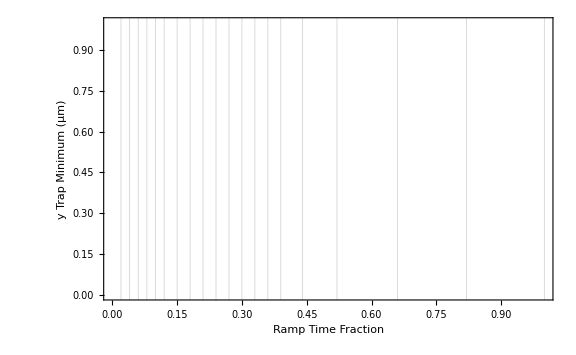
-Graphics-Show[ListLogPlot[Transpose[{{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,1/2,51/100,13/25,53/100,27/50,11/20,14/25,57/100,29/50,59/100,3/5,61/100,31/50,63/100,16/25,13/20,33/50,67/100,17/25,69/100,7/10,71/100,18/25,73/100,37/50,3/4,19/25,77/100,39/50,79/100,4/5,81/100,41/50,83/100,21/25,17/20,43/50,87/100,22/25,89/100,9/10,91/100,23/25,93/100,47/50,19/20,24/25,97/100,49/50,99/100,1},{{z0[0.8505,2.401,2.3,-8.9375,36.6722,1.5552]⟦All,2⟧,-8.9375,ChipTrapField[z0[0.8505,2.401,2.3,-8.9375,36.6722,1.5552],All,2,0.8505,2.401,2.3,-8.9375,36.6722,1.5552]},{z0[-0.00991 (0.8505-1. CurrL),-0.00991 (2.401-1. CurrZ),-0.00991 (2.3-1. CurrH),-0.00991 (-8.9375-1. Bx1),-0.00991 (36.6722-1. By1),-0.00991 (1.5552-1. Bz1)],-8.9375-0.00991 (-8.9375-1. Bx1),ChipTrapField[-0.00991 (0.8505-1. CurrL),-0.00991 (2.401-1. CurrZ),-0.00991 (2.3-1. CurrH),0.8505-0.00991 (0.8505-1. CurrL),2.401-0.00991 (2.401-1. CurrZ),2.3-0.00991 (2.3-1. CurrH),-8.9375-0.00991 (-8.9375-1. Bx1),36.6722-0.00991 (36.6722-1. By1),1.5552-0.00991 (1.5552-1. Bz1)]},{z0[-0.01982 (0.8505-1. CurrL),-0.01982 (2.401-1. CurrZ),-0.01982 (2.3-1. CurrH),-0.01982 (-8.9375-1. Bx1),-0.01982 (36.6722-1. By1),-0.01982 (1.5552-1. Bz1)],-8.9375-0.01982 (-8.9375-1. Bx1),ChipTrapField[-0.01982 (0.8505-1. CurrL),-0.01982 (2.401-1. CurrZ),-0.01982 (2.3-1. CurrH),0.8505-0.01982 (0.8505-1. CurrL),2.401-0.01982 (2.401-1. CurrZ),2.3-0.01982 (2.3-1. CurrH),-8.9375-0.01982 (-8.9375-1. Bx1),36.6722-0.01982 (36.6722-1. By1),1.5552-0.01982 (1.5552-1. Bz1)]},{z0[-0.04021 (0.8505-1. CurrL),-0.04021 (2.401-1. CurrZ),-0.04021 (2.3-1. CurrH),-0.04021 (-8.9375-1. Bx1),-0.04021 (36.6722-1. By1),-0.04021 (1.5552-1. Bz1)],-8.9375-0.04021 (-8.9375-1. Bx1),ChipTrapField[-0.04021 (0.8505-1. CurrL),-0.04021 (2.401-1. CurrZ),-0.04021 (2.3-1. CurrH),0.8505-0.04021 (0.8505-1. CurrL),2.401-0.04021 (2.401-1. CurrZ),2.3-0.04021 (2.3-1. CurrH),-8.9375-0.04021 (-8.9375-1. Bx1),36.6722-0.04021 (36.6722-1. By1),1.5552-0.04021 (1.5552-1. Bz1)]},{z0[-0.0606 (0.8505-1. CurrL),-0.0606 (2.401-1. CurrZ),-0.0606 (2.3-1. CurrH),-0.0606 (-8.9375-1. Bx1),-0.0606 (36.6722-1. By1),-0.0606 (1.5552-1. Bz1)],-8.9375-0.0606 (-8.9375-1. Bx1),ChipTrapField[-0.0606 (0.8505-1. CurrL),-0.0606 (2.401-1. CurrZ),-0.0606 (2.3-1. CurrH),0.8505-0.0606 (0.8505-1. CurrL),2.401-0.0606 (2.401-1. CurrZ),2.3-0.0606 (2.3-1. CurrH),-8.9375-0.0606 (-8.9375-1. Bx1),36.6722-0.0606 (36.6722-1. By1),1.5552-0.0606 (1.5552-1. Bz1)]},{z0[-0.092385 (0.8505-1. CurrL),-0.092385 (2.401-1. CurrZ),-0.092385 (2.3-1. CurrH),-0.092385 (-8.9375-1. Bx1),-0.092385 (36.6722-1. By1),-0.092385 (1.5552-1. Bz1)],-8.9375-0.092385 (-8.9375-1. Bx1),ChipTrapField[-0.092385 (0.8505-1. CurrL),-0.092385 (2.401-1. CurrZ),-0.092385 (2.3-1. CurrH),0.8505-0.092385 (0.8505-1. CurrL),2.401-0.092385 (2.401-1. CurrZ),2.3-0.092385 (2.3-1. CurrH),-8.9375-0.092385 (-8.9375-1. Bx1),36.6722-0.092385 (36.6722-1. By1),1.5552-0.092385 (1.5552-1. Bz1)]},{z0[-0.12417 (0.8505-1. CurrL),-0.12417 (2.401-1. CurrZ),-0.12417 (2.3-1. CurrH),-0.12417 (-8.9375-1. Bx1),-0.12417 (36.6722-1. By1),-0.12417 (1.5552-1. Bz1)],-8.9375-0.12417 (-8.9375-1. Bx1),ChipTrapField[-0.12417 (0.8505-1. CurrL),-0.12417 (2.401-1. CurrZ),-0.12417 (2.3-1. CurrH),0.8505-0.12417 (0.8505-1. CurrL),2.401-0.12417 (2.401-1. CurrZ),2.3-0.12417 (2.3-1. CurrH),-8.9375-0.12417 (-8.9375-1. Bx1),36.6722-0.12417 (36.6722-1. By1),1.5552-0.12417 (1.5552-1. Bz1)]},{z0[-0.165495 (0.8505-1. CurrL),-0.165495 (2.401-1. CurrZ),-0.165495 (2.3-1. CurrH),-0.165495 (-8.9375-1. Bx1),-0.165495 (36.6722-1. By1),-0.165495 (1.5552-1. Bz1)],-8.9375-0.165495 (-8.9375-1. Bx1),ChipTrapField[-0.165495 (0.8505-1. CurrL),-0.165495 (2.401-1. CurrZ),-0.165495 (2.3-1. CurrH),0.8505-0.165495 (0.8505-1. CurrL),2.401-0.165495 (2.401-1. CurrZ),2.3-0.165495 (2.3-1. CurrH),-8.9375-0.165495 (-8.9375-1. Bx1),36.6722-0.165495 (36.6722-1. By1),1.5552-0.165495 (1.5552-1. Bz1)]},{z0[-0.20682 (0.8505-1. CurrL),-0.20682 (2.401-1. CurrZ),-0.20682 (2.3-1. CurrH),-0.20682 (-8.9375-1. Bx1),-0.20682 (36.6722-1. By1),-0.20682 (1.5552-1. Bz1)],-8.9375-0.20682 (-8.9375-1. Bx1),ChipTrapField[-0.20682 (0.8505-1. CurrL),-0.20682 (2.401-1. CurrZ),-0.20682 (2.3-1. CurrH),0.8505-0.20682 (0.8505-1. CurrL),2.401-0.20682 (2.401-1. CurrZ),2.3-0.20682 (2.3-1. CurrH),-8.9375-0.20682 (-8.9375-1. Bx1),36.6722-0.20682 (36.6722-1. By1),1.5552-0.20682 (1.5552-1. Bz1)]},{z0[-0.25314 (0.8505-1. CurrL),-0.25314 (2.401-1. CurrZ),-0.25314 (2.3-1. CurrH),-0.25314 (-8.9375-1. Bx1),-0.25314 (36.6722-1. By1),-0.25314 (1.5552-1. Bz1)],-8.9375-0.25314 (-8.9375-1. Bx1),ChipTrapField[-0.25314 (0.8505-1. CurrL),-0.25314 (2.401-1. CurrZ),-0.25314 (2.3-1. CurrH),0.8505-0.25314 (0.8505-1. CurrL),2.401-0.25314 (2.401-1. CurrZ),2.3-0.25314 (2.3-1. CurrH),-8.9375-0.25314 (-8.9375-1. Bx1),36.6722-0.25314 (36.6722-1. By1),1.5552-0.25314 (1.5552-1. Bz1)]},{z0[-0.29946 (0.8505-1. CurrL),-0.29946 (2.401-1. CurrZ),-0.29946 (2.3-1. CurrH),-0.29946 (-8.9375-1. Bx1),-0.29946 (36.6722-1. By1),-0.29946 (1.5552-1. Bz1)],-8.9375-0.29946 (-8.9375-1. Bx1),ChipTrapField[-0.29946 (0.8505-1. CurrL),-0.29946 (2.401-1. CurrZ),-0.29946 (2.3-1. CurrH),0.8505-0.29946 (0.8505-1. CurrL),2.401-0.29946 (2.401-1. CurrZ),2.3-0.29946 (2.3-1. CurrH),-8.9375-0.29946 (-8.9375-1. Bx1),36.6722-0.29946 (36.6722-1. By1),1.5552-0.29946 (1.5552-1. Bz1)]},{z0[-0.34699 (0.8505-1. CurrL),-0.34699 (2.401-1. CurrZ),-0.34699 (2.3-1. CurrH),-0.34699 (-8.9375-1. Bx1),-0.34699 (36.6722-1. By1),-0.34699 (1.5552-1. Bz1)],-8.9375-0.34699 (-8.9375-1. Bx1),ChipTrapField[-0.34699 (0.8505-1. CurrL),-0.34699 (2.401-1. CurrZ),-0.34699 (2.3-1. CurrH),0.8505-0.34699 (0.8505-1. CurrL),2.401-0.34699 (2.401-1. CurrZ),2.3-0.34699 (2.3-1. CurrH),-8.9375-0.34699 (-8.9375-1. Bx1),36.6722-0.34699 (36.6722-1. By1),1.5552-0.34699 (1.5552-1. Bz1)]},{z0[-0.39452 (0.8505-1. CurrL),-0.39452 (2.401-1. CurrZ),-0.39452 (2.3-1. CurrH),-0.39452 (-8.9375-1. Bx1),-0.39452 (36.6722-1. By1),-0.39452 (1.5552-1. Bz1)],-8.9375-0.39452 (-8.9375-1. Bx1),ChipTrapField[-0.39452 (0.8505-1. CurrL),-0.39452 (2.401-1. CurrZ),-0.39452 (2.3-1. CurrH),0.8505-0.39452 (0.8505-1. CurrL),2.401-0.39452 (2.401-1. CurrZ),2.3-0.39452 (2.3-1. CurrH),-8.9375-0.39452 (-8.9375-1. Bx1),36.6722-0.39452 (36.6722-1. By1),1.5552-0.39452 (1.5552-1. Bz1)]},{z0[-0.438723 (0.8505-1. CurrL),-0.438723 (2.401-1. CurrZ),-0.438723 (2.3-1. CurrH),-0.438723 (-8.9375-1. Bx1),-0.438723 (36.6722-1. By1),-0.438723 (1.5552-1. Bz1)],-8.9375-0.438723 (-8.9375-1. Bx1),ChipTrapField[-0.438723 (0.8505-1. CurrL),-0.438723 (2.401-1. CurrZ),-0.438723 (2.3-1. CurrH),0.8505-0.438723 (0.8505-1. CurrL),2.401-0.438723 (2.401-1. CurrZ),2.3-0.438723 (2.3-1. CurrH),-8.9375-0.438723 (-8.9375-1. Bx1),36.6722-0.438723 (36.6722-1. By1),1.5552-0.438723 (1.5552-1. Bz1)]},{z0[-0.482927 (0.8505-1. CurrL),-0.482927 (2.401-1. CurrZ),-0.482927 (2.3-1. CurrH),-0.482927 (-8.9375-1. Bx1),-0.482927 (36.6722-1. By1),-0.482927 (1.5552-1. Bz1)],-8.9375-0.482927 (-8.9375-1. Bx1),ChipTrapField[-0.482927 (0.8505-1. CurrL),-0.482927 (2.401-1. CurrZ),-0.482927 (2.3-1. CurrH),0.8505-0.482927 (0.8505-1. CurrL),2.401-0.482927 (2.401-1. CurrZ),2.3-0.482927 (2.3-1. CurrH),-8.9375-0.482927 (-8.9375-1. Bx1),36.6722-0.482927 (36.6722-1. By1),1.5552-0.482927 (1.5552-1. Bz1)]},{z0[-0.52713 (0.8505-1. CurrL),-0.52713 (2.401-1. CurrZ),-0.52713 (2.3-1. CurrH),-0.52713 (-8.9375-1. Bx1),-0.52713 (36.6722-1. By1),-0.52713 (1.5552-1. Bz1)],-8.9375-0.52713 (-8.9375-1. Bx1),ChipTrapField[-0.52713 (0.8505-1. CurrL),-0.52713 (2.401-1. CurrZ),-0.52713 (2.3-1. CurrH),0.8505-0.52713 (0.8505-1. CurrL),2.401-0.52713 (2.401-1. CurrZ),2.3-0.52713 (2.3-1. CurrH),-8.9375-0.52713 (-8.9375-1. Bx1),36.6722-0.52713 (36.6722-1. By1),1.5552-0.52713 (1.5552-1. Bz1)]},{z0[-0.56413 (0.8505-1. CurrL),-0.56413 (2.401-1. CurrZ),-0.56413 (2.3-1. CurrH),-0.56413 (-8.9375-1. Bx1),-0.56413 (36.6722-1. By1),-0.56413 (1.5552-1. Bz1)],-8.9375-0.56413 (-8.9375-1. Bx1),ChipTrapField[-0.56413 (0.8505-1. CurrL),-0.56413 (2.401-1. CurrZ),-0.56413 (2.3-1. CurrH),0.8505-0.56413 (0.8505-1. CurrL),2.401-0.56413 (2.401-1. CurrZ),2.3-0.56413 (2.3-1. CurrH),-8.9375-0.56413 (-8.9375-1. Bx1),36.6722-0.56413 (36.6722-1. By1),1.5552-0.56413 (1.5552-1. Bz1)]},{z0[-0.60113 (0.8505-1. CurrL),-0.60113 (2.401-1. CurrZ),-0.60113 (2.3-1. CurrH),-0.60113 (-8.9375-1. Bx1),-0.60113 (36.6722-1. By1),-0.60113 (1.5552-1. Bz1)],-8.9375-0.60113 (-8.9375-1. Bx1),ChipTrapField[-0.60113 (0.8505-1. CurrL),-0.60113 (2.401-1. CurrZ),-0.60113 (2.3-1. CurrH),0.8505-0.60113 (0.8505-1. CurrL),2.401-0.60113 (2.401-1. CurrZ),2.3-0.60113 (2.3-1. CurrH),-8.9375-0.60113 (-8.9375-1. Bx1),36.6722-0.60113 (36.6722-1. By1),1.5552-0.60113 (1.5552-1. Bz1)]},{z0[-0.63813 (0.8505-1. CurrL),-0.63813 (2.401-1. CurrZ),-0.63813 (2.3-1. CurrH),-0.63813 (-8.9375-1. Bx1),-0.63813 (36.6722-1. By1),-0.63813 (1.5552-1. Bz1)],-8.9375-0.63813 (-8.9375-1. Bx1),ChipTrapField[-0.63813 (0.8505-1. CurrL),-0.63813 (2.401-1. CurrZ),-0.63813 (2.3-1. CurrH),0.8505-0.63813 (0.8505-1. CurrL),2.401-0.63813 (2.401-1. CurrZ),2.3-0.63813 (2.3-1. CurrH),-8.9375-0.63813 (-8.9375-1. Bx1),36.6722-0.63813 (36.6722-1. By1),1.5552-0.63813 (1.5552-1. Bz1)]},{z0[-0.66735 (0.8505-1. CurrL),-0.66735 (2.401-1. CurrZ),-0.66735 (2.3-1. CurrH),-0.66735 (-8.9375-1. Bx1),-0.66735 (36.6722-1. By1),-0.66735 (1.5552-1. Bz1)],-8.9375-0.66735 (-8.9375-1. Bx1),ChipTrapField[-0.66735 (0.8505-1. CurrL),-0.66735 (2.401-1. CurrZ),-0.66735 (2.3-1. CurrH),0.8505-0.66735 (0.8505-1. CurrL),2.401-0.66735 (2.401-1. CurrZ),2.3-0.66735 (2.3-1. CurrH),-8.9375-0.66735 (-8.9375-1. Bx1),36.6722-0.66735 (36.6722-1. By1),1.5552-0.66735 (1.5552-1. Bz1)]},{z0[-0.69657 (0.8505-1. CurrL),-0.69657 (2.401-1. CurrZ),-0.69657 (2.3-1. CurrH),-0.69657 (-8.9375-1. Bx1),-0.69657 (36.6722-1. By1),-0.69657 (1.5552-1. Bz1)],-8.9375-0.69657 (-8.9375-1. Bx1),ChipTrapField[-0.69657 (0.8505-1. CurrL),-0.69657 (2.401-1. CurrZ),-0.69657 (2.3-1. CurrH),0.8505-0.69657 (0.8505-1. CurrL),2.401-0.69657 (2.401-1. CurrZ),2.3-0.69657 (2.3-1. CurrH),-8.9375-0.69657 (-8.9375-1. Bx1),36.6722-0.69657 (36.6722-1. By1),1.5552-0.69657 (1.5552-1. Bz1)]},{z0[-0.72579 (0.8505-1. CurrL),-0.72579 (2.401-1. CurrZ),-0.72579 (2.3-1. CurrH),-0.72579 (-8.9375-1. Bx1),-0.72579 (36.6722-1. By1),-0.72579 (1.5552-1. Bz1)],-8.9375-0.72579 (-8.9375-1. Bx1),ChipTrapField[-0.72579 (0.8505-1. CurrL),-0.72579 (2.401-1. CurrZ),-0.72579 (2.3-1. CurrH),0.8505-0.72579 (0.8505-1. CurrL),2.401-0.72579 (2.401-1. CurrZ),2.3-0.72579 (2.3-1. CurrH),-8.9375-0.72579 (-8.9375-1. Bx1),36.6722-0.72579 (36.6722-1. By1),1.5552-0.72579 (1.5552-1. Bz1)]},{z0[-0.747893 (0.8505-1. CurrL),-0.747893 (2.401-1. CurrZ),-0.747893 (2.3-1. CurrH),-0.747893 (-8.9375-1. Bx1),-0.747893 (36.6722-1. By1),-0.747893 (1.5552-1. Bz1)],-8.9375-0.747893 (-8.9375-1. Bx1),ChipTrapField[-0.747893 (0.8505-1. CurrL),-0.747893 (2.401-1. CurrZ),-0.747893 (2.3-1. CurrH),0.8505-0.747893 (0.8505-1. CurrL),2.401-0.747893 (2.401-1. CurrZ),2.3-0.747893 (2.3-1. CurrH),-8.9375-0.747893 (-8.9375-1. Bx1),36.6722-0.747893 (36.6722-1. By1),1.5552-0.747893 (1.5552-1. Bz1)]},{z0[-0.769997 (0.8505-1. CurrL),-0.769997 (2.401-1. CurrZ),-0.769997 (2.3-1. CurrH),-0.769997 (-8.9375-1. Bx1),-0.769997 (36.6722-1. By1),-0.769997 (1.5552-1. Bz1)],-8.9375-0.769997 (-8.9375-1. Bx1),ChipTrapField[-0.769997 (0.8505-1. CurrL),-0.769997 (2.401-1. CurrZ),-0.769997 (2.3-1. CurrH),0.8505-0.769997 (0.8505-1. CurrL),2.401-0.769997 (2.401-1. CurrZ),2.3-0.769997 (2.3-1. CurrH),-8.9375-0.769997 (-8.9375-1. Bx1),36.6722-0.769997 (36.6722-1. By1),1.5552-0.769997 (1.5552-1. Bz1)]},{z0[-0.7921 (0.8505-1. CurrL),-0.7921 (2.401-1. CurrZ),-0.7921 (2.3-1. CurrH),-0.7921 (-8.9375-1. Bx1),-0.7921 (36.6722-1. By1),-0.7921 (1.5552-1. Bz1)],-8.9375-0.7921 (-8.9375-1. Bx1),ChipTrapField[-0.7921 (0.8505-1. CurrL),-0.7921 (2.401-1. CurrZ),-0.7921 (2.3-1. CurrH),0.8505-0.7921 (0.8505-1. CurrL),2.401-0.7921 (2.401-1. CurrZ),2.3-0.7921 (2.3-1. CurrH),-8.9375-0.7921 (-8.9375-1. Bx1),36.6722-0.7921 (36.6722-1. By1),1.5552-0.7921 (1.5552-1. Bz1)]},{z0[-0.80891 (0.8505-1. CurrL),-0.80891 (2.401-1. CurrZ),-0.80891 (2.3-1. CurrH),-0.80891 (-8.9375-1. Bx1),-0.80891 (36.6722-1. By1),-0.80891 (1.5552-1. Bz1)],-8.9375-0.80891 (-8.9375-1. Bx1),ChipTrapField[-0.80891 (0.8505-1. CurrL),-0.80891 (2.401-1. CurrZ),-0.80891 (2.3-1. CurrH),0.8505-0.80891 (0.8505-1. CurrL),2.401-0.80891 (2.401-1. CurrZ),2.3-0.80891 (2.3-1. CurrH),-8.9375-0.80891 (-8.9375-1. Bx1),36.6722-0.80891 (36.6722-1. By1),1.5552-0.80891 (1.5552-1. Bz1)]},{z0[-0.82572 (0.8505-1. CurrL),-0.82572 (2.401-1. CurrZ),-0.82572 (2.3-1. CurrH),-0.82572 (-8.9375-1. Bx1),-0.82572 (36.6722-1. By1),-0.82572 (1.5552-1. Bz1)],-8.9375-0.82572 (-8.9375-1. Bx1),ChipTrapField[-0.82572 (0.8505-1. CurrL),-0.82572 (2.401-1. CurrZ),-0.82572 (2.3-1. CurrH),0.8505-0.82572 (0.8505-1. CurrL),2.401-0.82572 (2.401-1. CurrZ),2.3-0.82572 (2.3-1. CurrH),-8.9375-0.82572 (-8.9375-1. Bx1),36.6722-0.82572 (36.6722-1. By1),1.5552-0.82572 (1.5552-1. Bz1)]},{z0[-0.84253 (0.8505-1. CurrL),-0.84253 (2.401-1. CurrZ),-0.84253 (2.3-1. CurrH),-0.84253 (-8.9375-1. Bx1),-0.84253 (36.6722-1. By1),-0.84253 (1.5552-1. Bz1)],-8.9375-0.84253 (-8.9375-1. Bx1),ChipTrapField[-0.84253 (0.8505-1. CurrL),-0.84253 (2.401-1. CurrZ),-0.84253 (2.3-1. CurrH),0.8505-0.84253 (0.8505-1. CurrL),2.401-0.84253 (2.401-1. CurrZ),2.3-0.84253 (2.3-1. CurrH),-8.9375-0.84253 (-8.9375-1. Bx1),36.6722-0.84253 (36.6722-1. By1),1.5552-0.84253 (1.5552-1. Bz1)]},{z0[-0.855073 (0.8505-1. CurrL),-0.855073 (2.401-1. CurrZ),-0.855073 (2.3-1. CurrH),-0.855073 (-8.9375-1. Bx1),-0.855073 (36.6722-1. By1),-0.855073 (1.5552-1. Bz1)],-8.9375-0.855073 (-8.9375-1. Bx1),ChipTrapField[-0.855073 (0.8505-1. CurrL),-0.855073 (2.401-1. CurrZ),-0.855073 (2.3-1. CurrH),0.8505-0.855073 (0.8505-1. CurrL),2.401-0.855073 (2.401-1. CurrZ),2.3-0.855073 (2.3-1. CurrH),-8.9375-0.855073 (-8.9375-1. Bx1),36.6722-0.855073 (36.6722-1. By1),1.5552-0.855073 (1.5552-1. Bz1)]},{z0[-0.867617 (0.8505-1. CurrL),-0.867617 (2.401-1. CurrZ),-0.867617 (2.3-1. CurrH),-0.867617 (-8.9375-1. Bx1),-0.867617 (36.6722-1. By1),-0.867617 (1.5552-1. Bz1)],-8.9375-0.867617 (-8.9375-1. Bx1),ChipTrapField[-0.867617 (0.8505-1. CurrL),-0.867617 (2.401-1. CurrZ),-0.867617 (2.3-1. CurrH),0.8505-0.867617 (0.8505-1. CurrL),2.401-0.867617 (2.401-1. CurrZ),2.3-0.867617 (2.3-1. CurrH),-8.9375-0.867617 (-8.9375-1. Bx1),36.6722-0.867617 (36.6722-1. By1),1.5552-0.867617 (1.5552-1. Bz1)]},{z0[-0.88016 (0.8505-1. CurrL),-0.88016 (2.401-1. CurrZ),-0.88016 (2.3-1. CurrH),-0.88016 (-8.9375-1. Bx1),-0.88016 (36.6722-1. By1),-0.88016 (1.5552-1. Bz1)],-8.9375-0.88016 (-8.9375-1. Bx1),ChipTrapField[-0.88016 (0.8505-1. CurrL),-0.88016 (2.401-1. CurrZ),-0.88016 (2.3-1. CurrH),0.8505-0.88016 (0.8505-1. CurrL),2.401-0.88016 (2.401-1. CurrZ),2.3-0.88016 (2.3-1. CurrH),-8.9375-0.88016 (-8.9375-1. Bx1),36.6722-0.88016 (36.6722-1. By1),1.5552-0.88016 (1.5552-1. Bz1)]},{z0[-0.88944 (0.8505-1. CurrL),-0.88944 (2.401-1. CurrZ),-0.88944 (2.3-1. CurrH),-0.88944 (-8.9375-1. Bx1),-0.88944 (36.6722-1. By1),-0.88944 (1.5552-1. Bz1)],-8.9375-0.88944 (-8.9375-1. Bx1),ChipTrapField[-0.88944 (0.8505-1. CurrL),-0.88944 (2.401-1. CurrZ),-0.88944 (2.3-1. CurrH),0.8505-0.88944 (0.8505-1. CurrL),2.401-0.88944 (2.401-1. CurrZ),2.3-0.88944 (2.3-1. CurrH),-8.9375-0.88944 (-8.9375-1. Bx1),36.6722-0.88944 (36.6722-1. By1),1.5552-0.88944 (1.5552-1. Bz1)]},{z0[-0.89872 (0.8505-1. CurrL),-0.89872 (2.401-1. CurrZ),-0.89872 (2.3-1. CurrH),-0.89872 (-8.9375-1. Bx1),-0.89872 (36.6722-1. By1),-0.89872 (1.5552-1. Bz1)],-8.9375-0.89872 (-8.9375-1. Bx1),ChipTrapField[-0.89872 (0.8505-1. CurrL),-0.89872 (2.401-1. CurrZ),-0.89872 (2.3-1. CurrH),0.8505-0.89872 (0.8505-1. CurrL),2.401-0.89872 (2.401-1. CurrZ),2.3-0.89872 (2.3-1. CurrH),-8.9375-0.89872 (-8.9375-1. Bx1),36.6722-0.89872 (36.6722-1. By1),1.5552-0.89872 (1.5552-1. Bz1)]},{z0[-0.908 (0.8505-1. CurrL),-0.908 (2.401-1. CurrZ),-0.908 (2.3-1. CurrH),-0.908 (-8.9375-1. Bx1),-0.908 (36.6722-1. By1),-0.908 (1.5552-1. Bz1)],-8.9375-0.908 (-8.9375-1. Bx1),ChipTrapField[-0.908 (0.8505-1. CurrL),-0.908 (2.401-1. CurrZ),-0.908 (2.3-1. CurrH),0.8505-0.908 (0.8505-1. CurrL),2.401-0.908 (2.401-1. CurrZ),2.3-0.908 (2.3-1. CurrH),-8.9375-0.908 (-8.9375-1. Bx1),36.6722-0.908 (36.6722-1. By1),1.5552-0.908 (1.5552-1. Bz1)]},{z0[-0.914953 (0.8505-1. CurrL),-0.914953 (2.401-1. CurrZ),-0.914953 (2.3-1. CurrH),-0.914953 (-8.9375-1. Bx1),-0.914953 (36.6722-1. By1),-0.914953 (1.5552-1. Bz1)],-8.9375-0.914953 (-8.9375-1. Bx1),ChipTrapField[-0.914953 (0.8505-1. CurrL),-0.914953 (2.401-1. CurrZ),-0.914953 (2.3-1. CurrH),0.8505-0.914953 (0.8505-1. CurrL),2.401-0.914953 (2.401-1. CurrZ),2.3-0.914953 (2.3-1. CurrH),-8.9375-0.914953 (-8.9375-1. Bx1),36.6722-0.914953 (36.6722-1. By1),1.5552-0.914953 (1.5552-1. Bz1)]},{z0[-0.921907 (0.8505-1. CurrL),-0.921907 (2.401-1. CurrZ),-0.921907 (2.3-1. CurrH),-0.921907 (-8.9375-1. Bx1),-0.921907 (36.6722-1. By1),-0.921907 (1.5552-1. Bz1)],-8.9375-0.921907 (-8.9375-1. Bx1),ChipTrapField[-0.921907 (0.8505-1. CurrL),-0.921907 (2.401-1. CurrZ),-0.921907 (2.3-1. CurrH),0.8505-0.921907 (0.8505-1. CurrL),2.401-0.921907 (2.401-1. CurrZ),2.3-0.921907 (2.3-1. CurrH),-8.9375-0.921907 (-8.9375-1. Bx1),36.6722-0.921907 (36.6722-1. By1),1.5552-0.921907 (1.5552-1. Bz1)]},{z0[-0.92886 (0.8505-1. CurrL),-0.92886 (2.401-1. CurrZ),-0.92886 (2.3-1. CurrH),-0.92886 (-8.9375-1. Bx1),-0.92886 (36.6722-1. By1),-0.92886 (1.5552-1. Bz1)],-8.9375-0.92886 (-8.9375-1. Bx1),ChipTrapField[-0.92886 (0.8505-1. CurrL),-0.92886 (2.401-1. CurrZ),-0.92886 (2.3-1. CurrH),0.8505-0.92886 (0.8505-1. CurrL),2.401-0.92886 (2.401-1. CurrZ),2.3-0.92886 (2.3-1. CurrH),-8.9375-0.92886 (-8.9375-1. Bx1),36.6722-0.92886 (36.6722-1. By1),1.5552-0.92886 (1.5552-1. Bz1)]},{z0[-0.934007 (0.8505-1. CurrL),-0.934007 (2.401-1. CurrZ),-0.934007 (2.3-1. CurrH),-0.934007 (-8.9375-1. Bx1),-0.934007 (36.6722-1. By1),-0.934007 (1.5552-1. Bz1)],-8.9375-0.934007 (-8.9375-1. Bx1),ChipTrapField[-0.934007 (0.8505-1. CurrL),-0.934007 (2.401-1. CurrZ),-0.934007 (2.3-1. CurrH),0.8505-0.934007 (0.8505-1. CurrL),2.401-0.934007 (2.401-1. CurrZ),2.3-0.934007 (2.3-1. CurrH),-8.9375-0.934007 (-8.9375-1. Bx1),36.6722-0.934007 (36.6722-1. By1),1.5552-0.934007 (1.5552-1. Bz1)]},{z0[-0.939153 (0.8505-1. CurrL),-0.939153 (2.401-1. CurrZ),-0.939153 (2.3-1. CurrH),-0.939153 (-8.9375-1. Bx1),-0.939153 (36.6722-1. By1),-0.939153 (1.5552-1. Bz1)],-8.9375-0.939153 (-8.9375-1. Bx1),ChipTrapField[-0.939153 (0.8505-1. CurrL),-0.939153 (2.401-1. CurrZ),-0.939153 (2.3-1. CurrH),0.8505-0.939153 (0.8505-1. CurrL),2.401-0.939153 (2.401-1. CurrZ),2.3-0.939153 (2.3-1. CurrH),-8.9375-0.939153 (-8.9375-1. Bx1),36.6722-0.939153 (36.6722-1. By1),1.5552-0.939153 (1.5552-1. Bz1)]},{z0[-0.9443 (0.8505-1. CurrL),-0.9443 (2.401-1. CurrZ),-0.9443 (2.3-1. CurrH),-0.9443 (-8.9375-1. Bx1),-0.9443 (36.6722-1. By1),-0.9443 (1.5552-1. Bz1)],-8.9375-0.9443 (-8.9375-1. Bx1),ChipTrapField[-0.9443 (0.8505-1. CurrL),-0.9443 (2.401-1. CurrZ),-0.9443 (2.3-1. CurrH),0.8505-0.9443 (0.8505-1. CurrL),2.401-0.9443 (2.401-1. CurrZ),2.3-0.9443 (2.3-1. CurrH),-8.9375-0.9443 (-8.9375-1. Bx1),36.6722-0.9443 (36.6722-1. By1),1.5552-0.9443 (1.5552-1. Bz1)]},{z0[-0.947978 (0.8505-1. CurrL),-0.947978 (2.401-1. CurrZ),-0.947978 (2.3-1. CurrH),-0.947978 (-8.9375-1. Bx1),-0.947978 (36.6722-1. By1),-0.947978 (1.5552-1. Bz1)],-8.9375-0.947978 (-8.9375-1. Bx1),ChipTrapField[-0.947978 (0.8505-1. CurrL),-0.947978 (2.401-1. CurrZ),-0.947978 (2.3-1. CurrH),0.8505-0.947978 (0.8505-1. CurrL),2.401-0.947978 (2.401-1. CurrZ),2.3-0.947978 (2.3-1. CurrH),-8.9375-0.947978 (-8.9375-1. Bx1),36.6722-0.947978 (36.6722-1. By1),1.5552-0.947978 (1.5552-1. Bz1)]},{z0[-0.951656 (0.8505-1. CurrL),-0.951656 (2.401-1. CurrZ),-0.951656 (2.3-1. CurrH),-0.951656 (-8.9375-1. Bx1),-0.951656 (36.6722-1. By1),-0.951656 (1.5552-1. Bz1)],-8.9375-0.951656 (-8.9375-1. Bx1),ChipTrapField[-0.951656 (0.8505-1. CurrL),-0.951656 (2.401-1. CurrZ),-0.951656 (2.3-1. CurrH),0.8505-0.951656 (0.8505-1. CurrL),2.401-0.951656 (2.401-1. CurrZ),2.3-0.951656 (2.3-1. CurrH),-8.9375-0.951656 (-8.9375-1. Bx1),36.6722-0.951656 (36.6722-1. By1),1.5552-0.951656 (1.5552-1. Bz1)]},{z0[-0.955334 (0.8505-1. CurrL),-0.955334 (2.401-1. CurrZ),-0.955334 (2.3-1. CurrH),-0.955334 (-8.9375-1. Bx1),-0.955334 (36.6722-1. By1),-0.955334 (1.5552-1. Bz1)],-8.9375-0.955334 (-8.9375-1. Bx1),ChipTrapField[-0.955334 (0.8505-1. CurrL),-0.955334 (2.401-1. CurrZ),-0.955334 (2.3-1. CurrH),0.8505-0.955334 (0.8505-1. CurrL),2.401-0.955334 (2.401-1. CurrZ),2.3-0.955334 (2.3-1. CurrH),-8.9375-0.955334 (-8.9375-1. Bx1),36.6722-0.955334 (36.6722-1. By1),1.5552-0.955334 (1.5552-1. Bz1)]},{z0[-0.959012 (0.8505-1. CurrL),-0.959012 (2.401-1. CurrZ),-0.959012 (2.3-1. CurrH),-0.959012 (-8.9375-1. Bx1),-0.959012 (36.6722-1. By1),-0.959012 (1.5552-1. Bz1)],-8.9375-0.959012 (-8.9375-1. Bx1),ChipTrapField[-0.959012 (0.8505-1. CurrL),-0.959012 (2.401-1. CurrZ),-0.959012 (2.3-1. CurrH),0.8505-0.959012 (0.8505-1. CurrL),2.401-0.959012 (2.401-1. CurrZ),2.3-0.959012 (2.3-1. CurrH),-8.9375-0.959012 (-8.9375-1. Bx1),36.6722-0.959012 (36.6722-1. By1),1.5552-0.959012 (1.5552-1. Bz1)]},{z0[-0.96269 (0.8505-1. CurrL),-0.96269 (2.401-1. CurrZ),-0.96269 (2.3-1. CurrH),-0.96269 (-8.9375-1. Bx1),-0.96269 (36.6722-1. By1),-0.96269 (1.5552-1. Bz1)],-8.9375-0.96269 (-8.9375-1. Bx1),ChipTrapField[-0.96269 (0.8505-1. CurrL),-0.96269 (2.401-1. CurrZ),-0.96269 (2.3-1. CurrH),0.8505-0.96269 (0.8505-1. CurrL),2.401-0.96269 (2.401-1. CurrZ),2.3-0.96269 (2.3-1. CurrH),-8.9375-0.96269 (-8.9375-1. Bx1),36.6722-0.96269 (36.6722-1. By1),1.5552-0.96269 (1.5552-1. Bz1)]},{z0[-0.964795 (0.8505-1. CurrL),-0.964795 (2.401-1. CurrZ),-0.964795 (2.3-1. CurrH),-0.964795 (-8.9375-1. Bx1),-0.964795 (36.6722-1. By1),-0.964795 (1.5552-1. Bz1)],-8.9375-0.964795 (-8.9375-1. Bx1),ChipTrapField[-0.964795 (0.8505-1. CurrL),-0.964795 (2.401-1. CurrZ),-0.964795 (2.3-1. CurrH),0.8505-0.964795 (0.8505-1. CurrL),2.401-0.964795 (2.401-1. CurrZ),2.3-0.964795 (2.3-1. CurrH),-8.9375-0.964795 (-8.9375-1. Bx1),36.6722-0.964795 (36.6722-1. By1),1.5552-0.964795 (1.5552-1. Bz1)]},{z0[-0.9669 (0.8505-1. CurrL),-0.9669 (2.401-1. CurrZ),-0.9669 (2.3-1. CurrH),-0.9669 (-8.9375-1. Bx1),-0.9669 (36.6722-1. By1),-0.9669 (1.5552-1. Bz1)],-8.9375-0.9669 (-8.9375-1. Bx1),ChipTrapField[-0.9669 (0.8505-1. CurrL),-0.9669 (2.401-1. CurrZ),-0.9669 (2.3-1. CurrH),0.8505-0.9669 (0.8505-1. CurrL),2.401-0.9669 (2.401-1. CurrZ),2.3-0.9669 (2.3-1. CurrH),-8.9375-0.9669 (-8.9375-1. Bx1),36.6722-0.9669 (36.6722-1. By1),1.5552-0.9669 (1.5552-1. Bz1)]},{z0[-0.969005 (0.8505-1. CurrL),-0.969005 (2.401-1. CurrZ),-0.969005 (2.3-1. CurrH),-0.969005 (-8.9375-1. Bx1),-0.969005 (36.6722-1. By1),-0.969005 (1.5552-1. Bz1)],-8.9375-0.969005 (-8.9375-1. Bx1),ChipTrapField[-0.969005 (0.8505-1. CurrL),-0.969005 (2.401-1. CurrZ),-0.969005 (2.3-1. CurrH),0.8505-0.969005 (0.8505-1. CurrL),2.401-0.969005 (2.401-1. CurrZ),2.3-0.969005 (2.3-1. CurrH),-8.9375-0.969005 (-8.9375-1. Bx1),36.6722-0.969005 (36.6722-1. By1),1.5552-0.969005 (1.5552-1. Bz1)]},{z0[-0.97111 (0.8505-1. CurrL),-0.97111 (2.401-1. CurrZ),-0.97111 (2.3-1. CurrH),-0.97111 (-8.9375-1. Bx1),-0.97111 (36.6722-1. By1),-0.97111 (1.5552-1. Bz1)],-8.9375-0.97111 (-8.9375-1. Bx1),ChipTrapField[-0.97111 (0.8505-1. CurrL),-0.97111 (2.401-1. CurrZ),-0.97111 (2.3-1. CurrH),0.8505-0.97111 (0.8505-1. CurrL),2.401-0.97111 (2.401-1. CurrZ),2.3-0.97111 (2.3-1. CurrH),-8.9375-0.97111 (-8.9375-1. Bx1),36.6722-0.97111 (36.6722-1. By1),1.5552-0.97111 (1.5552-1. Bz1)]},{z0[-0.973215 (0.8505-1. CurrL),-0.973215 (2.401-1. CurrZ),-0.973215 (2.3-1. CurrH),-0.973215 (-8.9375-1. Bx1),-0.973215 (36.6722-1. By1),-0.973215 (1.5552-1. Bz1)],-8.9375-0.973215 (-8.9375-1. Bx1),ChipTrapField[-0.973215 (0.8505-1. CurrL),-0.973215 (2.401-1. CurrZ),-0.973215 (2.3-1. CurrH),0.8505-0.973215 (0.8505-1. CurrL),2.401-0.973215 (2.401-1. CurrZ),2.3-0.973215 (2.3-1. CurrH),-8.9375-0.973215 (-8.9375-1. Bx1),36.6722-0.973215 (36.6722-1. By1),1.5552-0.973215 (1.5552-1. Bz1)]},{z0[-0.97532 (0.8505-1. CurrL),-0.97532 (2.401-1. CurrZ),-0.97532 (2.3-1. CurrH),-0.97532 (-8.9375-1. Bx1),-0.97532 (36.6722-1. By1),-0.97532 (1.5552-1. Bz1)],-8.9375-0.97532 (-8.9375-1. Bx1),ChipTrapField[-0.97532 (0.8505-1. CurrL),-0.97532 (2.401-1. CurrZ),-0.97532 (2.3-1. CurrH),0.8505-0.97532 (0.8505-1. CurrL),2.401-0.97532 (2.401-1. CurrZ),2.3-0.97532 (2.3-1. CurrH),-8.9375-0.97532 (-8.9375-1. Bx1),36.6722-0.97532 (36.6722-1. By1),1.5552-0.97532 (1.5552-1. Bz1)]},{z0[-0.977425 (0.8505-1. CurrL),-0.977425 (2.401-1. CurrZ),-0.977425 (2.3-1. CurrH),-0.977425 (-8.9375-1. Bx1),-0.977425 (36.6722-1. By1),-0.977425 (1.5552-1. Bz1)],-8.9375-0.977425 (-8.9375-1. Bx1),ChipTrapField[-0.977425 (0.8505-1. CurrL),-0.977425 (2.401-1. CurrZ),-0.977425 (2.3-1. CurrH),0.8505-0.977425 (0.8505-1. CurrL),2.401-0.977425 (2.401-1. CurrZ),2.3-0.977425 (2.3-1. CurrH),-8.9375-0.977425 (-8.9375-1. Bx1),36.6722-0.977425 (36.6722-1. By1),1.5552-0.977425 (1.5552-1. Bz1)]},{z0[-0.97953 (0.8505-1. CurrL),-0.97953 (2.401-1. CurrZ),-0.97953 (2.3-1. CurrH),-0.97953 (-8.9375-1. Bx1),-0.97953 (36.6722-1. By1),-0.97953 (1.5552-1. Bz1)],-8.9375-0.97953 (-8.9375-1. Bx1),ChipTrapField[-0.97953 (0.8505-1. CurrL),-0.97953 (2.401-1. CurrZ),-0.97953 (2.3-1. CurrH),0.8505-0.97953 (0.8505-1. CurrL),2.401-0.97953 (2.401-1. CurrZ),2.3-0.97953 (2.3-1. CurrH),-8.9375-0.97953 (-8.9375-1. Bx1),36.6722-0.97953 (36.6722-1. By1),1.5552-0.97953 (1.5552-1. Bz1)]},{z0[-0.980457 (0.8505-1. CurrL),-0.980457 (2.401-1. CurrZ),-0.980457 (2.3-1. CurrH),-0.980457 (-8.9375-1. Bx1),-0.980457 (36.6722-1. By1),-0.980457 (1.5552-1. Bz1)],-8.9375-0.980457 (-8.9375-1. Bx1),ChipTrapField[-0.980457 (0.8505-1. CurrL),-0.980457 (2.401-1. CurrZ),-0.980457 (2.3-1. CurrH),0.8505-0.980457 (0.8505-1. CurrL),2.401-0.980457 (2.401-1. CurrZ),2.3-0.980457 (2.3-1. CurrH),-8.9375-0.980457 (-8.9375-1. Bx1),36.6722-0.980457 (36.6722-1. By1),1.5552-0.980457 (1.5552-1. Bz1)]},{z0[-0.981384 (0.8505-1. CurrL),-0.981384 (2.401-1. CurrZ),-0.981384 (2.3-1. CurrH),-0.981384 (-8.9375-1. Bx1),-0.981384 (36.6722-1. By1),-0.981384 (1.5552-1. Bz1)],-8.9375-0.981384 (-8.9375-1. Bx1),ChipTrapField[-0.981384 (0.8505-1. CurrL),-0.981384 (2.401-1. CurrZ),-0.981384 (2.3-1. CurrH),0.8505-0.981384 (0.8505-1. CurrL),2.401-0.981384 (2.401-1. CurrZ),2.3-0.981384 (2.3-1. CurrH),-8.9375-0.981384 (-8.9375-1. Bx1),36.6722-0.981384 (36.6722-1. By1),1.5552-0.981384 (1.5552-1. Bz1)]},{z0[-0.982311 (0.8505-1. CurrL),-0.982311 (2.401-1. CurrZ),-0.982311 (2.3-1. CurrH),-0.982311 (-8.9375-1. Bx1),-0.982311 (36.6722-1. By1),-0.982311 (1.5552-1. Bz1)],-8.9375-0.982311 (-8.9375-1. Bx1),ChipTrapField[-0.982311 (0.8505-1. CurrL),-0.982311 (2.401-1. CurrZ),-0.982311 (2.3-1. CurrH),0.8505-0.982311 (0.8505-1. CurrL),2.401-0.982311 (2.401-1. CurrZ),2.3-0.982311 (2.3-1. CurrH),-8.9375-0.982311 (-8.9375-1. Bx1),36.6722-0.982311 (36.6722-1. By1),1.5552-0.982311 (1.5552-1. Bz1)]},{z0[-0.983239 (0.8505-1. CurrL),-0.983239 (2.401-1. CurrZ),-0.983239 (2.3-1. CurrH),-0.983239 (-8.9375-1. Bx1),-0.983239 (36.6722-1. By1),-0.983239 (1.5552-1. Bz1)],-8.9375-0.983239 (-8.9375-1. Bx1),ChipTrapField[-0.983239 (0.8505-1. CurrL),-0.983239 (2.401-1. CurrZ),-0.983239 (2.3-1. CurrH),0.8505-0.983239 (0.8505-1. CurrL),2.401-0.983239 (2.401-1. CurrZ),2.3-0.983239 (2.3-1. CurrH),-8.9375-0.983239 (-8.9375-1. Bx1),36.6722-0.983239 (36.6722-1. By1),1.5552-0.983239 (1.5552-1. Bz1)]},{z0[-0.984166 (0.8505-1. CurrL),-0.984166 (2.401-1. CurrZ),-0.984166 (2.3-1. CurrH),-0.984166 (-8.9375-1. Bx1),-0.984166 (36.6722-1. By1),-0.984166 (1.5552-1. Bz1)],-8.9375-0.984166 (-8.9375-1. Bx1),ChipTrapField[-0.984166 (0.8505-1. CurrL),-0.984166 (2.401-1. CurrZ),-0.984166 (2.3-1. CurrH),0.8505-0.984166 (0.8505-1. CurrL),2.401-0.984166 (2.401-1. CurrZ),2.3-0.984166 (2.3-1. CurrH),-8.9375-0.984166 (-8.9375-1. Bx1),36.6722-0.984166 (36.6722-1. By1),1.5552-0.984166 (1.5552-1. Bz1)]},{z0[-0.985093 (0.8505-1. CurrL),-0.985093 (2.401-1. CurrZ),-0.985093 (2.3-1. CurrH),-0.985093 (-8.9375-1. Bx1),-0.985093 (36.6722-1. By1),-0.985093 (1.5552-1. Bz1)],-8.9375-0.985093 (-8.9375-1. Bx1),ChipTrapField[-0.985093 (0.8505-1. CurrL),-0.985093 (2.401-1. CurrZ),-0.985093 (2.3-1. CurrH),0.8505-0.985093 (0.8505-1. CurrL),2.401-0.985093 (2.401-1. CurrZ),2.3-0.985093 (2.3-1. CurrH),-8.9375-0.985093 (-8.9375-1. Bx1),36.6722-0.985093 (36.6722-1. By1),1.5552-0.985093 (1.5552-1. Bz1)]},{z0[-0.98602 (0.8505-1. CurrL),-0.98602 (2.401-1. CurrZ),-0.98602 (2.3-1. CurrH),-0.98602 (-8.9375-1. Bx1),-0.98602 (36.6722-1. By1),-0.98602 (1.5552-1. Bz1)],-8.9375-0.98602 (-8.9375-1. Bx1),ChipTrapField[-0.98602 (0.8505-1. CurrL),-0.98602 (2.401-1. CurrZ),-0.98602 (2.3-1. CurrH),0.8505-0.98602 (0.8505-1. CurrL),2.401-0.98602 (2.401-1. CurrZ),2.3-0.98602 (2.3-1. CurrH),-8.9375-0.98602 (-8.9375-1. Bx1),36.6722-0.98602 (36.6722-1. By1),1.5552-0.98602 (1.5552-1. Bz1)]},{z0[-0.986947 (0.8505-1. CurrL),-0.986947 (2.401-1. CurrZ),-0.986947 (2.3-1. CurrH),-0.986947 (-8.9375-1. Bx1),-0.986947 (36.6722-1. By1),-0.986947 (1.5552-1. Bz1)],-8.9375-0.986947 (-8.9375-1. Bx1),ChipTrapField[-0.986947 (0.8505-1. CurrL),-0.986947 (2.401-1. CurrZ),-0.986947 (2.3-1. CurrH),0.8505-0.986947 (0.8505-1. CurrL),2.401-0.986947 (2.401-1. CurrZ),2.3-0.986947 (2.3-1. CurrH),-8.9375-0.986947 (-8.9375-1. Bx1),36.6722-0.986947 (36.6722-1. By1),1.5552-0.986947 (1.5552-1. Bz1)]},{z0[-0.987874 (0.8505-1. CurrL),-0.987874 (2.401-1. CurrZ),-0.987874 (2.3-1. CurrH),-0.987874 (-8.9375-1. Bx1),-0.987874 (36.6722-1. By1),-0.987874 (1.5552-1. Bz1)],-8.9375-0.987874 (-8.9375-1. Bx1),ChipTrapField[-0.987874 (0.8505-1. CurrL),-0.987874 (2.401-1. CurrZ),-0.987874 (2.3-1. CurrH),0.8505-0.987874 (0.8505-1. CurrL),2.401-0.987874 (2.401-1. CurrZ),2.3-0.987874 (2.3-1. CurrH),-8.9375-0.987874 (-8.9375-1. Bx1),36.6722-0.987874 (36.6722-1. By1),1.5552-0.987874 (1.5552-1. Bz1)]},{z0[-0.988801 (0.8505-1. CurrL),-0.988801 (2.401-1. CurrZ),-0.988801 (2.3-1. CurrH),-0.988801 (-8.9375-1. Bx1),-0.988801 (36.6722-1. By1),-0.988801 (1.5552-1. Bz1)],-8.9375-0.988801 (-8.9375-1. Bx1),ChipTrapField[-0.988801 (0.8505-1. CurrL),-0.988801 (2.401-1. CurrZ),-0.988801 (2.3-1. CurrH),0.8505-0.988801 (0.8505-1. CurrL),2.401-0.988801 (2.401-1. CurrZ),2.3-0.988801 (2.3-1. CurrH),-8.9375-0.988801 (-8.9375-1. Bx1),36.6722-0.988801 (36.6722-1. By1),1.5552-0.988801 (1.5552-1. Bz1)]},{z0[-0.989729 (0.8505-1. CurrL),-0.989729 (2.401-1. CurrZ),-0.989729 (2.3-1. CurrH),-0.989729 (-8.9375-1. Bx1),-0.989729 (36.6722-1. By1),-0.989729 (1.5552-1. Bz1)],-8.9375-0.989729 (-8.9375-1. Bx1),ChipTrapField[-0.989729 (0.8505-1. CurrL),-0.989729 (2.401-1. CurrZ),-0.989729 (2.3-1. CurrH),0.8505-0.989729 (0.8505-1. CurrL),2.401-0.989729 (2.401-1. CurrZ),2.3-0.989729 (2.3-1. CurrH),-8.9375-0.989729 (-8.9375-1. Bx1),36.6722-0.989729 (36.6722-1. By1),1.5552-0.989729 (1.5552-1. Bz1)]},{z0[-0.990656 (0.8505-1. CurrL),-0.990656 (2.401-1. CurrZ),-0.990656 (2.3-1. CurrH),-0.990656 (-8.9375-1. Bx1),-0.990656 (36.6722-1. By1),-0.990656 (1.5552-1. Bz1)],-8.9375-0.990656 (-8.9375-1. Bx1),ChipTrapField[-0.990656 (0.8505-1. CurrL),-0.990656 (2.401-1. CurrZ),-0.990656 (2.3-1. CurrH),0.8505-0.990656 (0.8505-1. CurrL),2.401-0.990656 (2.401-1. CurrZ),2.3-0.990656 (2.3-1. CurrH),-8.9375-0.990656 (-8.9375-1. Bx1),36.6722-0.990656 (36.6722-1. By1),1.5552-0.990656 (1.5552-1. Bz1)]},{z0[-0.991583 (0.8505-1. CurrL),-0.991583 (2.401-1. CurrZ),-0.991583 (2.3-1. CurrH),-0.991583 (-8.9375-1. Bx1),-0.991583 (36.6722-1. By1),-0.991583 (1.5552-1. Bz1)],-8.9375-0.991583 (-8.9375-1. Bx1),ChipTrapField[-0.991583 (0.8505-1. CurrL),-0.991583 (2.401-1. CurrZ),-0.991583 (2.3-1. CurrH),0.8505-0.991583 (0.8505-1. CurrL),2.401-0.991583 (2.401-1. CurrZ),2.3-0.991583 (2.3-1. CurrH),-8.9375-0.991583 (-8.9375-1. Bx1),36.6722-0.991583 (36.6722-1. By1),1.5552-0.991583 (1.5552-1. Bz1)]},{z0[-0.99251 (0.8505-1. CurrL),-0.99251 (2.401-1. CurrZ),-0.99251 (2.3-1. CurrH),-0.99251 (-8.9375-1. Bx1),-0.99251 (36.6722-1. By1),-0.99251 (1.5552-1. Bz1)],-8.9375-0.99251 (-8.9375-1. Bx1),ChipTrapField[-0.99251 (0.8505-1. CurrL),-0.99251 (2.401-1. CurrZ),-0.99251 (2.3-1. CurrH),0.8505-0.99251 (0.8505-1. CurrL),2.401-0.99251 (2.401-1. CurrZ),2.3-0.99251 (2.3-1. CurrH),-8.9375-0.99251 (-8.9375-1. Bx1),36.6722-0.99251 (36.6722-1. By1),1.5552-0.99251 (1.5552-1. Bz1)]},{z0[-0.992835 (0.8505-1. CurrL),-0.992835 (2.401-1. CurrZ),-0.992835 (2.3-1. CurrH),-0.992835 (-8.9375-1. Bx1),-0.992835 (36.6722-1. By1),-0.992835 (1.5552-1. Bz1)],-8.9375-0.992835 (-8.9375-1. Bx1),ChipTrapField[-0.992835 (0.8505-1. CurrL),-0.992835 (2.401-1. CurrZ),-0.992835 (2.3-1. CurrH),0.8505-0.992835 (0.8505-1. CurrL),2.401-0.992835 (2.401-1. CurrZ),2.3-0.992835 (2.3-1. CurrH),-8.9375-0.992835 (-8.9375-1. Bx1),36.6722-0.992835 (36.6722-1. By1),1.5552-0.992835 (1.5552-1. Bz1)]},{z0[-0.99316 (0.8505-1. CurrL),-0.99316 (2.401-1. CurrZ),-0.99316 (2.3-1. CurrH),-0.99316 (-8.9375-1. Bx1),-0.99316 (36.6722-1. By1),-0.99316 (1.5552-1. Bz1)],-8.9375-0.99316 (-8.9375-1. Bx1),ChipTrapField[-0.99316 (0.8505-1. CurrL),-0.99316 (2.401-1. CurrZ),-0.99316 (2.3-1. CurrH),0.8505-0.99316 (0.8505-1. CurrL),2.401-0.99316 (2.401-1. CurrZ),2.3-0.99316 (2.3-1. CurrH),-8.9375-0.99316 (-8.9375-1. Bx1),36.6722-0.99316 (36.6722-1. By1),1.5552-0.99316 (1.5552-1. Bz1)]},{z0[-0.993485 (0.8505-1. CurrL),-0.993485 (2.401-1. CurrZ),-0.993485 (2.3-1. CurrH),-0.993485 (-8.9375-1. Bx1),-0.993485 (36.6722-1. By1),-0.993485 (1.5552-1. Bz1)],-8.9375-0.993485 (-8.9375-1. Bx1),ChipTrapField[-0.993485 (0.8505-1. CurrL),-0.993485 (2.401-1. CurrZ),-0.993485 (2.3-1. CurrH),0.8505-0.993485 (0.8505-1. CurrL),2.401-0.993485 (2.401-1. CurrZ),2.3-0.993485 (2.3-1. CurrH),-8.9375-0.993485 (-8.9375-1. Bx1),36.6722-0.993485 (36.6722-1. By1),1.5552-0.993485 (1.5552-1. Bz1)]},{z0[-0.99381 (0.8505-1. CurrL),-0.99381 (2.401-1. CurrZ),-0.99381 (2.3-1. CurrH),-0.99381 (-8.9375-1. Bx1),-0.99381 (36.6722-1. By1),-0.99381 (1.5552-1. Bz1)],-8.9375-0.99381 (-8.9375-1. Bx1),ChipTrapField[-0.99381 (0.8505-1. CurrL),-0.99381 (2.401-1. CurrZ),-0.99381 (2.3-1. CurrH),0.8505-0.99381 (0.8505-1. CurrL),2.401-0.99381 (2.401-1. CurrZ),2.3-0.99381 (2.3-1. CurrH),-8.9375-0.99381 (-8.9375-1. Bx1),36.6722-0.99381 (36.6722-1. By1),1.5552-0.99381 (1.5552-1. Bz1)]},{z0[-0.994135 (0.8505-1. CurrL),-0.994135 (2.401-1. CurrZ),-0.994135 (2.3-1. CurrH),-0.994135 (-8.9375-1. Bx1),-0.994135 (36.6722-1. By1),-0.994135 (1.5552-1. Bz1)],-8.9375-0.994135 (-8.9375-1. Bx1),ChipTrapField[-0.994135 (0.8505-1. CurrL),-0.994135 (2.401-1. CurrZ),-0.994135 (2.3-1. CurrH),0.8505-0.994135 (0.8505-1. CurrL),2.401-0.994135 (2.401-1. CurrZ),2.3-0.994135 (2.3-1. CurrH),-8.9375-0.994135 (-8.9375-1. Bx1),36.6722-0.994135 (36.6722-1. By1),1.5552-0.994135 (1.5552-1. Bz1)]},{z0[-0.99446 (0.8505-1. CurrL),-0.99446 (2.401-1. CurrZ),-0.99446 (2.3-1. CurrH),-0.99446 (-8.9375-1. Bx1),-0.99446 (36.6722-1. By1),-0.99446 (1.5552-1. Bz1)],-8.9375-0.99446 (-8.9375-1. Bx1),ChipTrapField[-0.99446 (0.8505-1. CurrL),-0.99446 (2.401-1. CurrZ),-0.99446 (2.3-1. CurrH),0.8505-0.99446 (0.8505-1. CurrL),2.401-0.99446 (2.401-1. CurrZ),2.3-0.99446 (2.3-1. CurrH),-8.9375-0.99446 (-8.9375-1. Bx1),36.6722-0.99446 (36.6722-1. By1),1.5552-0.99446 (1.5552-1. Bz1)]},{z0[-0.994785 (0.8505-1. CurrL),-0.994785 (2.401-1. CurrZ),-0.994785 (2.3-1. CurrH),-0.994785 (-8.9375-1. Bx1),-0.994785 (36.6722-1. By1),-0.994785 (1.5552-1. Bz1)],-8.9375-0.994785 (-8.9375-1. Bx1),ChipTrapField[-0.994785 (0.8505-1. CurrL),-0.994785 (2.401-1. CurrZ),-0.994785 (2.3-1. CurrH),0.8505-0.994785 (0.8505-1. CurrL),2.401-0.994785 (2.401-1. CurrZ),2.3-0.994785 (2.3-1. CurrH),-8.9375-0.994785 (-8.9375-1. Bx1),36.6722-0.994785 (36.6722-1. By1),1.5552-0.994785 (1.5552-1. Bz1)]},{z0[-0.99511 (0.8505-1. CurrL),-0.99511 (2.401-1. CurrZ),-0.99511 (2.3-1. CurrH),-0.99511 (-8.9375-1. Bx1),-0.99511 (36.6722-1. By1),-0.99511 (1.5552-1. Bz1)],-8.9375-0.99511 (-8.9375-1. Bx1),ChipTrapField[-0.99511 (0.8505-1. CurrL),-0.99511 (2.401-1. CurrZ),-0.99511 (2.3-1. CurrH),0.8505-0.99511 (0.8505-1. CurrL),2.401-0.99511 (2.401-1. CurrZ),2.3-0.99511 (2.3-1. CurrH),-8.9375-0.99511 (-8.9375-1. Bx1),36.6722-0.99511 (36.6722-1. By1),1.5552-0.99511 (1.5552-1. Bz1)]},{z0[-0.995435 (0.8505-1. CurrL),-0.995435 (2.401-1. CurrZ),-0.995435 (2.3-1. CurrH),-0.995435 (-8.9375-1. Bx1),-0.995435 (36.6722-1. By1),-0.995435 (1.5552-1. Bz1)],-8.9375-0.995435 (-8.9375-1. Bx1),ChipTrapField[-0.995435 (0.8505-1. CurrL),-0.995435 (2.401-1. CurrZ),-0.995435 (2.3-1. CurrH),0.8505-0.995435 (0.8505-1. CurrL),2.401-0.995435 (2.401-1. CurrZ),2.3-0.995435 (2.3-1. CurrH),-8.9375-0.995435 (-8.9375-1. Bx1),36.6722-0.995435 (36.6722-1. By1),1.5552-0.995435 (1.5552-1. Bz1)]},{z0[-0.99576 (0.8505-1. CurrL),-0.99576 (2.401-1. CurrZ),-0.99576 (2.3-1. CurrH),-0.99576 (-8.9375-1. Bx1),-0.99576 (36.6722-1. By1),-0.99576 (1.5552-1. Bz1)],-8.9375-0.99576 (-8.9375-1. Bx1),ChipTrapField[-0.99576 (0.8505-1. CurrL),-0.99576 (2.401-1. CurrZ),-0.99576 (2.3-1. CurrH),0.8505-0.99576 (0.8505-1. CurrL),2.401-0.99576 (2.401-1. CurrZ),2.3-0.99576 (2.3-1. CurrH),-8.9375-0.99576 (-8.9375-1. Bx1),36.6722-0.99576 (36.6722-1. By1),1.5552-0.99576 (1.5552-1. Bz1)]},{z0[-0.996085 (0.8505-1. CurrL),-0.996085 (2.401-1. CurrZ),-0.996085 (2.3-1. CurrH),-0.996085 (-8.9375-1. Bx1),-0.996085 (36.6722-1. By1),-0.996085 (1.5552-1. Bz1)],-8.9375-0.996085 (-8.9375-1. Bx1),ChipTrapField[-0.996085 (0.8505-1. CurrL),-0.996085 (2.401-1. CurrZ),-0.996085 (2.3-1. CurrH),0.8505-0.996085 (0.8505-1. CurrL),2.401-0.996085 (2.401-1. CurrZ),2.3-0.996085 (2.3-1. CurrH),-8.9375-0.996085 (-8.9375-1. Bx1),36.6722-0.996085 (36.6722-1. By1),1.5552-0.996085 (1.5552-1. Bz1)]},{z0[-0.99641 (0.8505-1. CurrL),-0.99641 (2.401-1. CurrZ),-0.99641 (2.3-1. CurrH),-0.99641 (-8.9375-1. Bx1),-0.99641 (36.6722-1. By1),-0.99641 (1.5552-1. Bz1)],-8.9375-0.99641 (-8.9375-1. Bx1),ChipTrapField[-0.99641 (0.8505-1. CurrL),-0.99641 (2.401-1. CurrZ),-0.99641 (2.3-1. CurrH),0.8505-0.99641 (0.8505-1. CurrL),2.401-0.99641 (2.401-1. CurrZ),2.3-0.99641 (2.3-1. CurrH),-8.9375-0.99641 (-8.9375-1. Bx1),36.6722-0.99641 (36.6722-1. By1),1.5552-0.99641 (1.5552-1. Bz1)]},{z0[-0.996735 (0.8505-1. CurrL),-0.996735 (2.401-1. CurrZ),-0.996735 (2.3-1. CurrH),-0.996735 (-8.9375-1. Bx1),-0.996735 (36.6722-1. By1),-0.996735 (1.5552-1. Bz1)],-8.9375-0.996735 (-8.9375-1. Bx1),ChipTrapField[-0.996735 (0.8505-1. CurrL),-0.996735 (2.401-1. CurrZ),-0.996735 (2.3-1. CurrH),0.8505-0.996735 (0.8505-1. CurrL),2.401-0.996735 (2.401-1. CurrZ),2.3-0.996735 (2.3-1. CurrH),-8.9375-0.996735 (-8.9375-1. Bx1),36.6722-0.996735 (36.6722-1. By1),1.5552-0.996735 (1.5552-1. Bz1)]},{z0[-0.99706 (0.8505-1. CurrL),-0.99706 (2.401-1. CurrZ),-0.99706 (2.3-1. CurrH),-0.99706 (-8.9375-1. Bx1),-0.99706 (36.6722-1. By1),-0.99706 (1.5552-1. Bz1)],-8.9375-0.99706 (-8.9375-1. Bx1),ChipTrapField[-0.99706 (0.8505-1. CurrL),-0.99706 (2.401-1. CurrZ),-0.99706 (2.3-1. CurrH),0.8505-0.99706 (0.8505-1. CurrL),2.401-0.99706 (2.401-1. CurrZ),2.3-0.99706 (2.3-1. CurrH),-8.9375-0.99706 (-8.9375-1. Bx1),36.6722-0.99706 (36.6722-1. By1),1.5552-0.99706 (1.5552-1. Bz1)]},{z0[-0.997385 (0.8505-1. CurrL),-0.997385 (2.401-1. CurrZ),-0.997385 (2.3-1. CurrH),-0.997385 (-8.9375-1. Bx1),-0.997385 (36.6722-1. By1),-0.997385 (1.5552-1. Bz1)],-8.9375-0.997385 (-8.9375-1. Bx1),ChipTrapField[-0.997385 (0.8505-1. CurrL),-0.997385 (2.401-1. CurrZ),-0.997385 (2.3-1. CurrH),0.8505-0.997385 (0.8505-1. CurrL),2.401-0.997385 (2.401-1. CurrZ),2.3-0.997385 (2.3-1. CurrH),-8.9375-0.997385 (-8.9375-1. Bx1),36.6722-0.997385 (36.6722-1. By1),1.5552-0.997385 (1.5552-1. Bz1)]},{z0[-0.99771 (0.8505-1. CurrL),-0.99771 (2.401-1. CurrZ),-0.99771 (2.3-1. CurrH),-0.99771 (-8.9375-1. Bx1),-0.99771 (36.6722-1. By1),-0.99771 (1.5552-1. Bz1)],-8.9375-0.99771 (-8.9375-1. Bx1),ChipTrapField[-0.99771 (0.8505-1. CurrL),-0.99771 (2.401-1. CurrZ),-0.99771 (2.3-1. CurrH),0.8505-0.99771 (0.8505-1. CurrL),2.401-0.99771 (2.401-1. CurrZ),2.3-0.99771 (2.3-1. CurrH),-8.9375-0.99771 (-8.9375-1. Bx1),36.6722-0.99771 (36.6722-1. By1),1.5552-0.99771 (1.5552-1. Bz1)]},{z0[-0.997837 (0.8505-1. CurrL),-0.997837 (2.401-1. CurrZ),-0.997837 (2.3-1. CurrH),-0.997837 (-8.9375-1. Bx1),-0.997837 (36.6722-1. By1),-0.997837 (1.5552-1. Bz1)],-8.9375-0.997837 (-8.9375-1. Bx1),ChipTrapField[-0.997837 (0.8505-1. CurrL),-0.997837 (2.401-1. CurrZ),-0.997837 (2.3-1. CurrH),0.8505-0.997837 (0.8505-1. CurrL),2.401-0.997837 (2.401-1. CurrZ),2.3-0.997837 (2.3-1. CurrH),-8.9375-0.997837 (-8.9375-1. Bx1),36.6722-0.997837 (36.6722-1. By1),1.5552-0.997837 (1.5552-1. Bz1)]},{z0[-0.997964 (0.8505-1. CurrL),-0.997964 (2.401-1. CurrZ),-0.997964 (2.3-1. CurrH),-0.997964 (-8.9375-1. Bx1),-0.997964 (36.6722-1. By1),-0.997964 (1.5552-1. Bz1)],-8.9375-0.997964 (-8.9375-1. Bx1),ChipTrapField[-0.997964 (0.8505-1. CurrL),-0.997964 (2.401-1. CurrZ),-0.997964 (2.3-1. CurrH),0.8505-0.997964 (0.8505-1. CurrL),2.401-0.997964 (2.401-1. CurrZ),2.3-0.997964 (2.3-1. CurrH),-8.9375-0.997964 (-8.9375-1. Bx1),36.6722-0.997964 (36.6722-1. By1),1.5552-0.997964 (1.5552-1. Bz1)]},{z0[-0.998092 (0.8505-1. CurrL),-0.998092 (2.401-1. CurrZ),-0.998092 (2.3-1. CurrH),-0.998092 (-8.9375-1. Bx1),-0.998092 (36.6722-1. By1),-0.998092 (1.5552-1. Bz1)],-8.9375-0.998092 (-8.9375-1. Bx1),ChipTrapField[-0.998092 (0.8505-1. CurrL),-0.998092 (2.401-1. CurrZ),-0.998092 (2.3-1. CurrH),0.8505-0.998092 (0.8505-1. CurrL),2.401-0.998092 (2.401-1. CurrZ),2.3-0.998092 (2.3-1. CurrH),-8.9375-0.998092 (-8.9375-1. Bx1),36.6722-0.998092 (36.6722-1. By1),1.5552-0.998092 (1.5552-1. Bz1)]},{z0[-0.998219 (0.8505-1. CurrL),-0.998219 (2.401-1. CurrZ),-0.998219 (2.3-1. CurrH),-0.998219 (-8.9375-1. Bx1),-0.998219 (36.6722-1. By1),-0.998219 (1.5552-1. Bz1)],-8.9375-0.998219 (-8.9375-1. Bx1),ChipTrapField[-0.998219 (0.8505-1. CurrL),-0.998219 (2.401-1. CurrZ),-0.998219 (2.3-1. CurrH),0.8505-0.998219 (0.8505-1. CurrL),2.401-0.998219 (2.401-1. CurrZ),2.3-0.998219 (2.3-1. CurrH),-8.9375-0.998219 (-8.9375-1. Bx1),36.6722-0.998219 (36.6722-1. By1),1.5552-0.998219 (1.5552-1. Bz1)]},{z0[-0.998346 (0.8505-1. CurrL),-0.998346 (2.401-1. CurrZ),-0.998346 (2.3-1. CurrH),-0.998346 (-8.9375-1. Bx1),-0.998346 (36.6722-1. By1),-0.998346 (1.5552-1. Bz1)],-8.9375-0.998346 (-8.9375-1. Bx1),ChipTrapField[-0.998346 (0.8505-1. CurrL),-0.998346 (2.401-1. CurrZ),-0.998346 (2.3-1. CurrH),0.8505-0.998346 (0.8505-1. CurrL),2.401-0.998346 (2.401-1. CurrZ),2.3-0.998346 (2.3-1. CurrH),-8.9375-0.998346 (-8.9375-1. Bx1),36.6722-0.998346 (36.6722-1. By1),1.5552-0.998346 (1.5552-1. Bz1)]},{z0[-0.998473 (0.8505-1. CurrL),-0.998473 (2.401-1. CurrZ),-0.998473 (2.3-1. CurrH),-0.998473 (-8.9375-1. Bx1),-0.998473 (36.6722-1. By1),-0.998473 (1.5552-1. Bz1)],-8.9375-0.998473 (-8.9375-1. Bx1),ChipTrapField[-0.998473 (0.8505-1. CurrL),-0.998473 (2.401-1. CurrZ),-0.998473 (2.3-1. CurrH),0.8505-0.998473 (0.8505-1. CurrL),2.401-0.998473 (2.401-1. CurrZ),2.3-0.998473 (2.3-1. CurrH),-8.9375-0.998473 (-8.9375-1. Bx1),36.6722-0.998473 (36.6722-1. By1),1.5552-0.998473 (1.5552-1. Bz1)]},{z0[-0.998601 (0.8505-1. CurrL),-0.998601 (2.401-1. CurrZ),-0.998601 (2.3-1. CurrH),-0.998601 (-8.9375-1. Bx1),-0.998601 (36.6722-1. By1),-0.998601 (1.5552-1. Bz1)],-8.9375-0.998601 (-8.9375-1. Bx1),ChipTrapField[-0.998601 (0.8505-1. CurrL),-0.998601 (2.401-1. CurrZ),-0.998601 (2.3-1. CurrH),0.8505-0.998601 (0.8505-1. CurrL),2.401-0.998601 (2.401-1. CurrZ),2.3-0.998601 (2.3-1. CurrH),-8.9375-0.998601 (-8.9375-1. Bx1),36.6722-0.998601 (36.6722-1. By1),1.5552-0.998601 (1.5552-1. Bz1)]},{z0[-0.998728 (0.8505-1. CurrL),-0.998728 (2.401-1. CurrZ),-0.998728 (2.3-1. CurrH),-0.998728 (-8.9375-1. Bx1),-0.998728 (36.6722-1. By1),-0.998728 (1.5552-1. Bz1)],-8.9375-0.998728 (-8.9375-1. Bx1),ChipTrapField[-0.998728 (0.8505-1. CurrL),-0.998728 (2.401-1. CurrZ),-0.998728 (2.3-1. CurrH),0.8505-0.998728 (0.8505-1. CurrL),2.401-0.998728 (2.401-1. CurrZ),2.3-0.998728 (2.3-1. CurrH),-8.9375-0.998728 (-8.9375-1. Bx1),36.6722-0.998728 (36.6722-1. By1),1.5552-0.998728 (1.5552-1. Bz1)]},{z0[-0.998855 (0.8505-1. CurrL),-0.998855 (2.401-1. CurrZ),-0.998855 (2.3-1. CurrH),-0.998855 (-8.9375-1. Bx1),-0.998855 (36.6722-1. By1),-0.998855 (1.5552-1. Bz1)],-8.9375-0.998855 (-8.9375-1. Bx1),ChipTrapField[-0.998855 (0.8505-1. CurrL),-0.998855 (2.401-1. CurrZ),-0.998855 (2.3-1. CurrH),0.8505-0.998855 (0.8505-1. CurrL),2.401-0.998855 (2.401-1. CurrZ),2.3-0.998855 (2.3-1. CurrH),-8.9375-0.998855 (-8.9375-1. Bx1),36.6722-0.998855 (36.6722-1. By1),1.5552-0.998855 (1.5552-1. Bz1)]},{z0[-0.998982 (0.8505-1. CurrL),-0.998982 (2.401-1. CurrZ),-0.998982 (2.3-1. CurrH),-0.998982 (-8.9375-1. Bx1),-0.998982 (36.6722-1. By1),-0.998982 (1.5552-1. Bz1)],-8.9375-0.998982 (-8.9375-1. Bx1),ChipTrapField[-0.998982 (0.8505-1. CurrL),-0.998982 (2.401-1. CurrZ),-0.998982 (2.3-1. CurrH),0.8505-0.998982 (0.8505-1. CurrL),2.401-0.998982 (2.401-1. CurrZ),2.3-0.998982 (2.3-1. CurrH),-8.9375-0.998982 (-8.9375-1. Bx1),36.6722-0.998982 (36.6722-1. By1),1.5552-0.998982 (1.5552-1. Bz1)]},{z0[-0.999109 (0.8505-1. CurrL),-0.999109 (2.401-1. CurrZ),-0.999109 (2.3-1. CurrH),-0.999109 (-8.9375-1. Bx1),-0.999109 (36.6722-1. By1),-0.999109 (1.5552-1. Bz1)],-8.9375-0.999109 (-8.9375-1. Bx1),ChipTrapField[-0.999109 (0.8505-1. CurrL),-0.999109 (2.401-1. CurrZ),-0.999109 (2.3-1. CurrH),0.8505-0.999109 (0.8505-1. CurrL),2.401-0.999109 (2.401-1. CurrZ),2.3-0.999109 (2.3-1. CurrH),-8.9375-0.999109 (-8.9375-1. Bx1),36.6722-0.999109 (36.6722-1. By1),1.5552-0.999109 (1.5552-1. Bz1)]},{z0[-0.999237 (0.8505-1. CurrL),-0.999237 (2.401-1. CurrZ),-0.999237 (2.3-1. CurrH),-0.999237 (-8.9375-1. Bx1),-0.999237 (36.6722-1. By1),-0.999237 (1.5552-1. Bz1)],-8.9375-0.999237 (-8.9375-1. Bx1),ChipTrapField[-0.999237 (0.8505-1. CurrL),-0.999237 (2.401-1. CurrZ),-0.999237 (2.3-1. CurrH),0.8505-0.999237 (0.8505-1. CurrL),2.401-0.999237 (2.401-1. CurrZ),2.3-0.999237 (2.3-1. CurrH),-8.9375-0.999237 (-8.9375-1. Bx1),36.6722-0.999237 (36.6722-1. By1),1.5552-0.999237 (1.5552-1. Bz1)]},{z0[-0.999364 (0.8505-1. CurrL),-0.999364 (2.401-1. CurrZ),-0.999364 (2.3-1. CurrH),-0.999364 (-8.9375-1. Bx1),-0.999364 (36.6722-1. By1),-0.999364 (1.5552-1. Bz1)],-8.9375-0.999364 (-8.9375-1. Bx1),ChipTrapField[-0.999364 (0.8505-1. CurrL),-0.999364 (2.401-1. CurrZ),-0.999364 (2.3-1. CurrH),0.8505-0.999364 (0.8505-1. CurrL),2.401-0.999364 (2.401-1. CurrZ),2.3-0.999364 (2.3-1. CurrH),-8.9375-0.999364 (-8.9375-1. Bx1),36.6722-0.999364 (36.6722-1. By1),1.5552-0.999364 (1.5552-1. Bz1)]},{z0[-0.999491 (0.8505-1. CurrL),-0.999491 (2.401-1. CurrZ),-0.999491 (2.3-1. CurrH),-0.999491 (-8.9375-1. Bx1),-0.999491 (36.6722-1. By1),-0.999491 (1.5552-1. Bz1)],-8.9375-0.999491 (-8.9375-1. Bx1),ChipTrapField[-0.999491 (0.8505-1. CurrL),-0.999491 (2.401-1. CurrZ),-0.999491 (2.3-1. CurrH),0.8505-0.999491 (0.8505-1. CurrL),2.401-0.999491 (2.401-1. CurrZ),2.3-0.999491 (2.3-1. CurrH),-8.9375-0.999491 (-8.9375-1. Bx1),36.6722-0.999491 (36.6722-1. By1),1.5552-0.999491 (1.5552-1. Bz1)]},{z0[-0.999618 (0.8505-1. CurrL),-0.999618 (2.401-1. CurrZ),-0.999618 (2.3-1. CurrH),-0.999618 (-8.9375-1. Bx1),-0.999618 (36.6722-1. By1),-0.999618 (1.5552-1. Bz1)],-8.9375-0.999618 (-8.9375-1. Bx1),ChipTrapField[-0.999618 (0.8505-1. CurrL),-0.999618 (2.401-1. CurrZ),-0.999618 (2.3-1. CurrH),0.8505-0.999618 (0.8505-1. CurrL),2.401-0.999618 (2.401-1. CurrZ),2.3-0.999618 (2.3-1. CurrH),-8.9375-0.999618 (-8.9375-1. Bx1),36.6722-0.999618 (36.6722-1. By1),1.5552-0.999618 (1.5552-1. Bz1)]},{z0[-0.999746 (0.8505-1. CurrL),-0.999746 (2.401-1. CurrZ),-0.999746 (2.3-1. CurrH),-0.999746 (-8.9375-1. Bx1),-0.999746 (36.6722-1. By1),-0.999746 (1.5552-1. Bz1)],-8.9375-0.999746 (-8.9375-1. Bx1),ChipTrapField[-0.999746 (0.8505-1. CurrL),-0.999746 (2.401-1. CurrZ),-0.999746 (2.3-1. CurrH),0.8505-0.999746 (0.8505-1. CurrL),2.401-0.999746 (2.401-1. CurrZ),2.3-0.999746 (2.3-1. CurrH),-8.9375-0.999746 (-8.9375-1. Bx1),36.6722-0.999746 (36.6722-1. By1),1.5552-0.999746 (1.5552-1. Bz1)]},{z0[-0.999873 (0.8505-1. CurrL),-0.999873 (2.401-1. CurrZ),-0.999873 (2.3-1. CurrH),-0.999873 (-8.9375-1. Bx1),-0.999873 (36.6722-1. By1),-0.999873 (1.5552-1. Bz1)],-8.9375-0.999873 (-8.9375-1. Bx1),ChipTrapField[-0.999873 (0.8505-1. CurrL),-0.999873 (2.401-1. CurrZ),-0.999873 (2.3-1. CurrH),0.8505-0.999873 (0.8505-1. CurrL),2.401-0.999873 (2.401-1. CurrZ),2.3-0.999873 (2.3-1. CurrH),-8.9375-0.999873 (-8.9375-1. Bx1),36.6722-0.999873 (36.6722-1. By1),1.5552-0.999873 (1.5552-1. Bz1)]},{z0[-1. (0.8505-1. CurrL),-1. (2.401-1. CurrZ),-1. (2.3-1. CurrH),-1. (-8.9375-1. Bx1),-1. (36.6722-1. By1),-1. (1.5552-1. Bz1)],-8.9375-1. (-8.9375-1. Bx1),ChipTrapField[-1. (0.8505-1. CurrL),-1. (2.401-1. CurrZ),-1. (2.3-1. CurrH),0.8505-1. (0.8505-1. CurrL),2.401-1. (2.401-1. CurrZ),2.3-1. (2.3-1. CurrH),-8.9375-1. (-8.9375-1. Bx1),36.6722-1. (36.6722-1. By1),1.5552-1. (1.5552-1. Bz1)]}}⟦All,2,2⟧}],ImagePadding→40,{Frame→{{False,True},{False,False}},FrameStyle→{{Automatic,RGBColor[1, 0, 0]},{Automatic,Automatic}},FrameTicks→{{None,All},{None,None}}},FrameLabel→{{,y-axis frequency (Hz)},{Ramp Time Fraction,Trap 1 Expansion}},PlotRange→All,PlotStyle→RGBColor[1, 0, 0],GridLines→{{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.},{}}],-Graphics-,ImageSize→Large]
 |  |  |  |

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

Part::partd: Part specification {«1»}⟦All,2,3⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,«51»},{{«1»},{«1»},{«1»},«46»,{«1»},«51»}⟦All,2,3⟧} cannot be transposed.

Part::partd: Part specification {«1»}⟦All,2,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},{«1»}⟦All,2,3⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»},{«1»}⟦«1»⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[«1»].

GridLines→{{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.},{}}

{{1.0202,1.04081,1.06184,1.08329,1.10517,1.1275,1.16183,1.19722,1.23368,1.27125,1.30996,1.34986,1.39097,1.43333,1.47698,1.55271,1.68203,1.93479,2.2705,2.71828},{}}

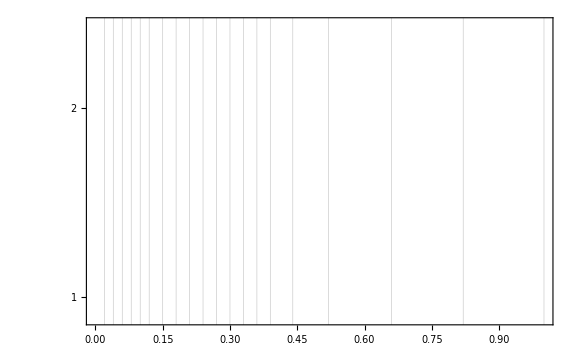

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

```mathematica
plotZFreqVZmin[movingtrap_]:=Module[{zs,omegas},
zs[n_]:=movingtrap⟦n,1,3⟧*10^6;
omegas[n_]:=movingtrap⟦n,2,3⟧;

ListPlot[Table[{zs[n],omegas[n]},{n,Range[Length[movingtrap]]}],Frame->True,FrameLabel->{"Trap z position (μm)","Trap z frequency (Hz)"}]
]
plotZFreqVZmin[pts1s]
```

Part::partd: Part specification {«1»}⟦1,2,3⟧ is longer than depth of object.

Part::partw: Part 3 of -8.9375-0.00991 (-8.9375-1. Bx1) does not exist.

Part::partw: Part 3 of -8.9375-0.01982 (-8.9375-1. Bx1) does not exist.

Part::partw: Part 3 of -8.9375-0.04021 (-8.9375-1. Bx1) does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {«1»}⟦1,2,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

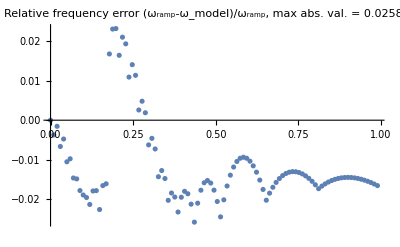

```mathematica
plotFreqError[pts1s]
```

```mathematica
printTrapParameters[{{minx_,miny_,minz_},{omegax_,omegay_,omegaz_},bmin_}]:=Print[
"Position = "<>ToString[{minx,miny,minz}*10^6]<>" μm\n"<>
"Frequency = "<>ToString[{omegax,omegay,omegaz}]<>" Hz\n"<>
"Bmin = "<>ToString[bmin]<>" G"];

printTrapParameters[pts1s⟦1⟧]
printTrapParameters[pts1s⟦-1⟧]
```

Position = {74.2507, -21.9915, 135.717} μm
Frequency = {117.929, 968.724, 929.95} Hz
Bmin = 8.97843 G

Position = {19.6048, 341.948, 627.837} μm
Frequency = {22.6293, 54.4236, 57.4638} Hz
Bmin = 4.98191 G

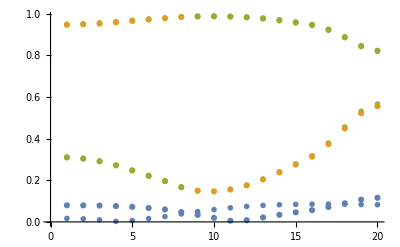

```mathematica
plotTrapPrincAxes[trap1_,trap2_,rampin_]:=Module[
{nramps=Length@rampin⟦1⟧,
eVecIndex,
characVtime,
vec2Plot,vec3Plot},
characVtime=Table[SingleTrapCharacteristics[trap1,trap2,rampin,nramps,n],{n,nramps}];
eVecIndex=2;
vec2Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}],PlotMarkers->"OpenMarkers"];
eVecIndex=3;
vec3Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}]];
Show[vec2Plot,vec3Plot]
]
plotTrapPrincAxes[trapzero,trapone,rampin1s]
```

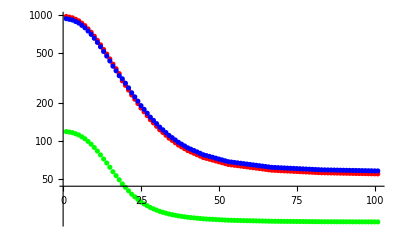

```mathematica
plotTrapYandZCharacteristics[movingramp_]:=Module[
{xFreqs=movingramp⟦All,2,1⟧,
yFreqs=movingramp⟦All,2,2⟧,
zFreqs=movingramp⟦All,2,3⟧,
xPlot,yPlot,zPlot},
xPlot=ListLogPlot[xFreqs,PlotStyle->Green];
yPlot=ListLogPlot[yFreqs,PlotStyle->Red];
zPlot=ListLogPlot[zFreqs,PlotStyle->Blue];
Show[yPlot,zPlot,xPlot,PlotRange->All]
]
plotTrapYandZCharacteristics[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.0203,0.06334,0.12889,0.21062,0.30014,0.38959,0.51269,0.61583,0.6994,0.76623,0.81863,0.85919,0.89041,0.91429,0.93242,0.95401,0.97428,0.99021,0.99699,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20200730T110658

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

G:\My Drive\bubble_bec\output\20200730T110658_trap1short.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.,2.6,2.6,-1.95,6.14298,-3.11336}}

G:\My Drive\bubble_bec\output\20200730T110658_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

```mathematica
defineTableFromTrap[trapone]
```

{0.,-0.742857,0.52,0.006,0.006,0.142384,0.100095}